# Surface Circuit SAT

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191b, Spring 2021.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

Before executing any of the cells below, first run all the initialization cells in FastSurfaceCRNs.nb.

Note that this notebook is not cleaned up... it is stream-of-consciousness exploration of ideas.  The only actually implemented idea is near the end, the Symmetric3SATCRN.  No guarantees made about anything....

The goal here is to explore an alternative to Matt Bauer’s surface CRN that solves 3SAT problems.

This first construction will be called the LogicNorSATCRN.

We’ll start with the 20-reaction surface CRN for running feedforward and feedback circuits with NOR gates and FANOUT (from SurfaceCRNs.nb). 

Instead of having signals that start at the inputs and travel directionally along wires toward the outputs (or looping back), we will keep a signal maintained on on every wire -- it never leaves.  A signal will just communicate between the gates that the wire connects, which may be as many as one wishes since a wire can fanout as much as it likes... the signal will just propagate everywhere to turn the wire solid 0 or solid 1.  (A wire could even be thick!  Like a map region!)  The wire will still have the abcabcabcabc structure, so that a gate can distinguish its two inputs and its output.  A NOR gate will always be in a consistent state, with (input a, input b, output c) in { 001, 010, 100, 110 }.  If a wire is inconsistent, it does a random walk to fix itself; if a gate is inconsistent with a wire, it changes itself or the wire.

(* wire must be consistent [12 reactions] *) 
a0 + b1 --> a0 + b0	b0 + c1 --> b0 + c0	c0 + a1 --> c0 + a0
a0 + b1 --> a1 + b1	b0 + c1 --> b1 + c1	c0 + a1--> c1 + a1
a1 + b0 --> a0 + b0	b1 + c0 --> b0 + c0	c1 + a0 --> c0 + a0
a1 + b0 --> a1 + b1	b1 + c0 --> b1 + c1	c1 + a0 --> c1 + a1

(* clamp a wire, w/o log do this just for wire phase a [2 reactions] *)
0 + a1 --> 0 + a0	1 + a0 --> 1 + a1

(* if gate is inconsistent with wires, fix the wire [12 reactions] *)
N001+a1 --> N001+a0	N001+b1 --> N001+b0	N001+c0 --> N001+c1
N010+a1 --> N010+a0	N010+b0 --> N010+b1	N010+c1 --> N010+c0
N100+a0 --> N100+a1	N100+b1 --> N100+b0	N100+c1 --> N100+c0
N110+a0 --> N110+a1	N110+b0 --> N110+b1	N110+c1 --> N110+c0

(* if gate is inconsistent with wires, fix the gate... there may be more than one way [22 reactions] *)
N001+a1 --> N100+a1	N001+a1 --> N110+a1	
N001+b1 --> N010+b1	N001+b1 --> N110+b1
N001+c0 --> N010+c0	N001+c0 --> N100+c0	N001+c0 --> N110+c0

N010+a1 --> N110+a1	N010+a1 --> N100+a1	
N010+b0 --> N001+b0	N010+b0 --> N100+b1
N010+c1 --> N001+c1

N100+a0 --> N001+a0	N100+a0 --> N010+a0
N100+b1 --> N010+b1	N100+b1 --> N110+b1
N100+c1 --> N001+c1

N110+a0 --> N010+a0	N110+a0 --> N001+a0
N110+b0 --> N001+b0	N110+b0 --> N100+b0
N110+c1 --> N001+c1

Note that I included all possible new gate states that agree with the wire information, regardless of how many other wires must change, or whether there is a simpler way to find agreement.  Also note that the surface CRN halts when the circuit is satisfied.

The same principle could be used to introduce reactions for other types of gate, feedforward or relational, as well as wire-crosses, but we are already universal for circuits.  And we already have 48 reactions, which is plenty.  

The final question is what rates the reactions should have.  Here is where we might bias the system to make fewer changes if possible, or to make the change that causes the least trouble elsewhere.   Perhaps we could concretely pose this as:  Given a single NOR gate connected to 3 unchanging gates (aka 3 clamps) that are in fact consistent, for what rate constants will the NOR gate and wires converge in the least expected time?  (And do the optimal rate constants depend on the wire lengths?)

Just for fun, let’s pause to consider whether abcabcabc wires are the best choice here.  The allow each gate to be a single site, but then there are a lot of  reactions for wire consistency, and perhaps we could consider the duplication of logic for the two NOR gate inputs also as being extraneous.  Perhaps an alternative would be for a homogeneous wire but multi-site gate logic, like Lulu’s design and Sam’s design.  But thinking it over, the input side of the gate needs to be able to distinguish the two inputs, so we need an ababab wire.  Since length needs to be adjustable and strict ababab forces a checkerboard, we need at least one phase to be extendable.

Let’s call this construction the ModularNorSATCRN.

(* wire must be consistent *)
a0 + b1 --> a1 + b1		a0 + b1 --> a0 + b0		a1 + b0 --> a1 + b1		a1 + b0 --> a0 + b0		a1 + a0 --> a1 + a1		a1 + a0 --> a0 + a0

(* clamp a wire *)
0 + a1 --> 0 + a0		1 + a0 --> 1 + a1

(* input-side of gate: fix input gate *)
a0 + IN10 --> a0 + IN00		a0 + IN11 --> a0 + IN01		a1 + 	IN00 --> a1 + IN10		a1 + IN01 --> a1 + IN11
b0 + IN01 --> b0 + IN00		b0 + IN11 --> b0 + IN10		b1 + IN00 --> b1 + IN01		b1 + IN10 --> b1 + IN11

(* input-side of gate: fix wires *)
a0 + IN10 --> a1 + IN10		a0 + IN11 --> a1 + IN11		a1 + 	IN00 --> a0 + IN00		a1 + IN01 --> a0 + IN01
b0 + IN01 --> b1 + IN01		b0 + IN11 --> b1 + IN11		b1 + IN00 --> b0 + IN00		b1 + IN10 --> b0 + IN10

(* input/output junction, fix input side *)
IN00+OUT0 --> IN01+OUT0	IN00+OUT0 --> IN10+OUT0	IN00+OUT0 --> IN11+OUT0
IN01+OUT1 --> IN00+OUT1	IN10+OUT1 --> IN00+OUT1	IN11+OUT1 --> IN00+OUT1

(* input/output junction, fix output side *)
IN00+OUT0 --> IN00+OUT1
IN01+OUT1 --> IN01+OUT0	IN10+OUT1 --> IN10+OUT0	IN11+OUT1 --> IN11+OUT0

(* output-side of gate: fix wire *)
OUT0 + a1 --> OUT0 + a0		OUT1 + a0 --> OUT1 + a1

(* output-side of gate: fix gate *)
OUT0 + a1 --> OUT1 + a1		OUT1 + a0 --> OUT0 + a0

This now ought to be able to represent the same set of circuits in a very similar way, but has only 38 reactions.  Therefore, the number of rate constants (and potential ability to optimize bias for the search) is fewer, so they can’t be said to be equivalent.   This surface CRN also halts when the circuit is satisfied.

Crossover is pretty easy with ababab wires: and IN site with two a’s and two b’s will enforce consistency between the a’s and consistency between the b’s.  Pretty neat!  No new reactions necessary.  NOT is fairly easy to construct also, since we just need to fan-out the input wire to both NOR-gate IN ports.

Maybe this isn’t the place for it, but can’t we beat the SurfaceCRNs.nb record for digital logic circuits, at least in the case of feedforward use-once circuits?  If people can make logic out of BZ reactions, and the GH surface CRN is just 3 reactions, we ought to be able to do better.

PaintCircuitCRN: SINGLE-RAIL, 0 and 1 signals arrive

(* use-once wires and fan-out *)
w + 0 --> 0 + 0
w + 1 --> 1 + 1

(* OR gates, which can spill over into an input line if it’s irrelevant *)
1 + OR  --> 1 + 1

(* NOT gates *)
0 + NOT --> 0 + 1
1 + NOT --> 1 + 0

That’s actually all we need.  5 reactions.  Goldschlager 1977 says planar is enough (using 9 NAND and 3 AND gates and a bunch of fan-out, which ought to fit within 10x10).  But if we want wire cross directly, it’s another 8 reactions!  CrossPaintCircuitCRN adds:

     W
 w w C w w     	0 + C --> X +X0		1 + C --> X + X1		X1 + w --> B + 1		X0 + w --> B + 0		
     W			0 + X --> B + Y 		1 + X --> B + Y		Y + W --> Z + w		Z + W --> w + w
 
 This will wait for the (here) horizontal signal to pass, then convert to a local vertical wire that connects an otherwise disconnected vertical. 
 

DoublePaintCircuitCRN:  DUAL-RAIL, signal S arrives

(* use-once wires and fan-out and OR gates, which can spill over into an input line if it’s irrelevant *)
w + S --> S + S

(* use-once 2-input AND gate *)
S + AND --> _ + w

(* wire cross, which also serves as NOT gate in dual rail logic *)
S + CROSS --> X1 + X2	X2 + w --> X3 + S		X1 + X3 --> X4 + _		S + X4 --> _ + X5	X5 + W --> X6 + w		X6 + W --> w + w
	 W
w w w CROSS w w w
           W
           
In total 8 reactions (compared to 13 for single-rail).  Most of it is the wire cross, which is a bit annoying.  I don’t think Goldschlager 1977 works here though.
(“The monotone and planar circuit value problems are log space complete for P”,  https://dl.acm.org/doi/pdf/10.1145/1008354.1008356)

CAN WE DO BETTER?!?

FuseCircuitCRN:  Here is a 7-reaction use-once dual-rail surface CRN with a slightly more complex OR and a much simpler CROSS.  Now signals are like fuses, rather than like painting the wires.  So fan-out requires 1 more reaction... so not actually better, just different.

S+w --> _+S	S+AND --> _+w		S+OR --> _ + s		s+W --> _ + S
S+C --> _+A	A+w --> B+S		s+B --> _+s		S+F --> s+S

w
OR W w w
w

	w
	OR
w w 	C w w
	W
	
    W
w w F w w

Bottom line: 5 reactions using Goldschlager crossovers and single-rail with the PaintCircuitCRN.

If 5 reactions are enough for arbitrary use-once feedforward circuits, we ought to be able to do better than 38 reactions for circuit-SAT.  Try again?

Let’s try to simply and symmetrize the 38-reaction  ababab construction above.  We will use just c for conveying wires, and split into a and b just one site adjacent to the NOR gate, whose output will immediately go to c.

SymmetricNorSATCRN:

(* wire must be consistent *)
a0 + c1 --> a1 + c1		a0 + c1 --> a0 + c0		a1 + c0 --> a1 + c1		a1 + c0 --> a0 + c0	
b0 + c1 --> b1 + c1		b0 + c1 --> b0 + c0		b1 + c0 --> b1 + c1		b1 + c0 --> b0 + c0		
c1 + c0 --> c1 + c1		c1 + c0 --> c0 + c0

(* clamp a wire *)
0 + c1 --> 0 + c0		1 + c0 --> 1 + c1

(* input-side of gate: fix gate *)
a0 + IN10 --> a0 + IN00		a0 + IN11 --> a0 + IN01		a1 + 	IN00 --> a1 + IN10		a1 + IN01 --> a1 + IN11
b0 + IN01 --> b0 + IN00		b0 + IN11 --> b0 + IN10		b1 + IN00 --> b1 + IN01		b1 + IN10 --> b1 + IN11

(* input-side of gate: fix wires *)
a0 + IN10 --> a1 + IN10		a0 + IN11 --> a1 + IN11		a1 + 	IN00 --> a0 + IN00		a1 + IN01 --> a0 + IN01
b0 + IN01 --> b1 + IN01		b0 + IN11 --> b1 + IN11		b1 + IN00 --> b0 + IN00		b1 + IN10 --> b0 + IN10

(* output-side of gate: fix gate *)
IN00+c0 --> IN01+c0			IN00+c0 --> IN10+c0			IN00+c0 --> IN11+c0
IN01+c1 --> IN00+c1			IN10+c1 --> IN00+c1			IN11+c1 --> IN00+c1

(* output-side of gate: fix wire *)
IN00+c0 --> IN00+c1
IN01+c1 --> IN01+c0			IN10+c1 --> IN10+c0			IN11+c1 --> IN11+c0

Again, it is 38 reactions!  Again, crossover can be done with an IN site flanked by 2 a’s and 3 b’s.  Again, NOT is obtained trivially by fan-out to both inputs of NOR.  I guess this looks a little nicer to me, even if it isn’t smaller.

I am pretty sure that all these constructions will work (or at least are easily debuggable to work) in the sense of being able to reach a solution if one exists, and stopping when it has been reached, but I have no idea how efficiently they will find circuit-SAT solutions.  Even for feedforward clamping, there is an entropy game that could make randomization more likely than progress.

For this, directional signals along abcabcabc wires (like I was originally planning on) may be the better thing.  Rather than always having a signal on each wire, bouncing around forever, we can set it such that only a wire in conflict has a signal, and when all conflicts are gone, no more signals bounce around.  When a signal hits a gate, if it is in agreement with the gate’s stored info, then it disappears; if it is in conflict, then either it flips its own state and bounces back, or else the gate changes its state and emits more signals.  Naively, it seems that there would be a linear speed-up over the unbiased random-walk wires that we have been considering above.  To further bias the search toward solutions, we would like the number of active signals (i.e. number of conflicts) to on average decrease.  WalkSAT does this by allowing each potential new conflict introduced by a flip some chance of rejecting the change, so the more new conflicts that would be created, the smaller the chance that the change will actually go through -- thus attempting to make all changes simultaneously ends up with the best one probably being selected.  In the context of a NOR circuit with active directional signals... it’s not clear to me what the effective analogy is.

If instead of aiming for arbitrary Circuit SAT, we confined ourselves to 3SAT like Matt Bauer’s term project, the 38-reaction  SymmetricNorSATCRN can be simplified to the 31-reaction Symmetric3SATCRN, which allows for more compact layouts.  We use A as the primary wire; it can transfer to B and C; adjacent Cs must be complements so that’s the NOT gate; P stores a pair of A and B values, so it can serve as a crossover; and P next to C enforces that at least one value is True, so it can serve as a SAT clause.  We don’t need to clamp wires for this use case.

(* wire must be consistent *)
a1 + a0 --> a1 + a1		a1 + a0 --> a0 + a0

(* A must match B, and A must match C *)
a0 + b1 --> a1 + b1		a0 + b1 --> a0 + b0		a1 + b0 --> a1 + b1		a1 + b0 --> a0 + b0	
a0 + c1 --> a1 + c1		a0 + c1 --> a0 + c0		a1 + c0 --> a1 + c1		a1 + c0 --> a0 + c0		

(* adjacent C must mismatch *)
c0 + c0 --> c0 + c1		c1 + c1 --> c0 + c1

(* P pairs  A and B  inputs, so it can serve as a crossover or as a consolidator *)
a0 + P10 --> a0 + P00		a0 + P11 --> a0 + P01		a1 + 	P00 --> a1 + P10		a1 + P01 --> a1 + P11
b0 + P01 --> b0 + P00		b0 + P11 --> b0 + P10		b1 + P00 --> b1 + P01		b1 + P10 --> b1 + P11
a0 + P10 --> a1 + P10		a0 + P11 --> a1 + P11		a1 + 	P00 --> a0 + P00		a1 + P01 --> a0 + P01
b0 + P01 --> b1 + P01		b0 + P11 --> b1 + P11		b1 + P00 --> b0 + P00		b1 + P10 --> b0 + P10

(* P enforces “at least one is true” among its internal values an an adjacent C *)
P00+c0 --> P01+c0			P00+c0 --> P10+c0			P00+c0 --> P00+c1

11 species and 31 reactions in all.

```mathematica
Symmetric3SATCRN=With[{slow=1},
{
rxn[a1+a0,a1+a1,1],rxn[a1+a0,a0+a0,1],
rxn[a0+b1,a1+b1,1],rxn[a0+b1,a0+b0,1],rxn[a1+b0,a1+b1,1],rxn[a1+b0,a0+b0,1],
rxn[a0+c1,a1+c1,1],rxn[a0+c1,a0+c0,1],rxn[a1+c0,a1+c1,1],rxn[a1+c0,a0+c0,1],
rxn[c0+c0,c0+c1,1],rxn[c1+c1,c0+c1,1],
rxn[a0+P10,a0+P00,1],rxn[a0+P11,a0+P01,1],rxn[a1+P00,a1+P10,1],rxn[a1+P01,a1+P11,1],
rxn[b0+P01,b0+P00,1],rxn[b0+P11,b0+P10,1],rxn[b1+P00,b1+P01,1],rxn[b1+P10,b1+P11,1],
rxn[a0+P10,a1+P10,1],rxn[a0+P11,a1+P11,1],rxn[a1+P00,a0+P00,1],rxn[a1+P01,a0+P01,1],
rxn[b0+P01,b1+P01,1],rxn[b0+P11,b1+P11,1],rxn[b1+P00,b0+P00,1],rxn[b1+P10,b0+P10,1],
rxn[P00+c0,P01+c0,slow],rxn[P00+c0,P10+c0,slow],rxn[P00+c0,P00+c1,slow]
}];
ColorSymmetric3SATCRN={
o->Gray,
a1->White,b1->White,c1->Lighter[Pink],
a0->Black,b0->Black,c0->Darker[Red],
P00->Darker[Green],P01->Green,P10->Green,P11->Lighter[Green]
};
```

For layout, the formula must be in proper 3SAT form with at least 2 variables and at least 2 clauses, else all bets are off.

```mathematica
LayoutSymmetric3SAT[formula_]:=Module[{unit,surface,vars,clauses,N,M,pos,i,j},
vars=BooleanVariables[formula]; N=Length[vars];
clauses=List@@formula; M=Length[clauses];
unit={ 
{o,A,A,P,B,A,o},
{o,A,o,C,o,A,o},
{o,A,o,A,o,A,o},
{o,A,o,A,o,A,o},
{o,B,o,B,o,B,o},
{A,P,A,P,A,P,A},
{o,B,o,B,o,B,o}
};
unit=Join[unit,Join@@Table[unit[[{-2,-1}]],N-1]];
surface=ArrayFlatten[{Table[unit,M]}];
For[i=1,i≤M,i++,
If[Head[clauses[[i,1]]]===Not,surface[[{2,3},2+7(i-1)]]={C,C}];
If[Head[clauses[[i,2]]]===Not,surface[[{2,3},4+7(i-1)]]={C,C}];
If[Head[clauses[[i,3]]]===Not,surface[[{2,3},6+7(i-1)]]={C,C}];
pos=Flatten[Position[vars,First[BooleanVariables[#]]]&/@(List@@clauses[[i]])];
For[j=1,j≤Length[pos],j++,surface[[2 pos[[j]]+4,7(i-1)+2 j]]=A]
];
surface
]
AssignmentFrom3SATSurface[formula_,surface_]:=Module[{vars,N},
vars=BooleanVariables[formula]; N=Length[vars];
MapThread[Rule,{vars,surface[[6+2 Range[N],3]]/.{a0->False,a1->True}}]
]
```

```mathematica
BauerSAT=(x||y||z)&&(!x||!y||z);
AdlemanSAT = (!x03 || !x16 || x18)&&(x05||x12||!x09)&&(!x13||!x02||x20)&&(x12||!x09||!x05)&&(x19||!x04||x06)&&(x09||x12||!x05)&&(!x01||x04||!x11)&&(x13||!x02||!x19)&&(x05||x17||x09)&&(x15||x09||!x17)&&(!x05||!x09||!x12)&&(x06||x11||x04)&&(!x15||!x17||x07)&&(!x06||x19||x13)&&(!x12||!x09||x05)&&(x12||x01||x14)&&(x20||x03||x02)&&(x10||!x07||!x08)&&(!x05||x09||!x12)&&(x18||!x20||x03)&&(!x10||!x18||!x16)&&(x01||!x11||!x14)&&(x08||!x07||!x15)&&(!x08||x16||!x10);
```

```mathematica
StandardVariables[Nvars_,prefix_:"x"]:=With[{k=Ceiling[Log[10,Nvars+1]]},
ToExpression/@Table[prefix<>(StringJoin@@ToString/@IntegerDigits[i,10,k]),{i,Nvars}]
]
```

```mathematica
RandomKSAT[k_,Nvars_,Mclauses_]:=Module[{vars,Flip},
vars=StandardVariables[Nvars];
Flip[var_]:=If[RandomChoice[{True,False}],var,Not[var]];
And @@ Table[Or@@(Flip/@ RandomSample[vars,k]),{Mclauses}]
]
```

```mathematica
SolvableRandomKSAT[k_,Nvars_,Mclauses_]:= Module[{expr,solvable=False},
While[!solvable,
expr=RandomKSAT[k,Nvars,Mclauses] ;
solvable=SatisfiableQ[expr,BooleanVariables[expr]];
];
expr
]
```

```mathematica
LayoutSymmetric3SAT[BauerSAT]//MatrixForm
```

(o | A | A | P | B | A | o | o | A | A | P | B | A | o
o | A | o | C | o | A | o | o | C | o | C | o | A | o
o | A | o | A | o | A | o | o | C | o | C | o | A | o
o | A | o | A | o | A | o | o | A | o | A | o | A | o
o | B | o | B | o | B | o | o | B | o | B | o | B | o
A | A | A | P | A | P | A | A | A | A | P | A | P | A
o | B | o | B | o | B | o | o | B | o | B | o | B | o
A | P | A | A | A | P | A | A | P | A | A | A | P | A
o | B | o | B | o | B | o | o | B | o | B | o | B | o
A | P | A | P | A | A | A | A | P | A | P | A | A | A
o | B | o | B | o | B | o | o | B | o | B | o | B | o)

```mathematica
InitializeSymmetric3SAT[formula_]:=ArrayPad[LayoutSymmetric3SAT[formula] /.{A->a0,B->b0,C->c0,P->P00},2,o]
```

Try one of these four cases to watch the surface CRN run.  It won’t solve AdlemanSAT in any likelihood, though... just too slow.

```mathematica
problem=BauerSAT;
```

```mathematica
problem=AdlemanSAT;
```

```mathematica
problem=SolvableRandomKSAT[3,5,5];
```

```mathematica
problem=SolvableRandomKSAT[3,10,30];
```

```mathematica
problem=SolvableRandomKSAT[3,10,Round[4.2*10]];
```

```mathematica
Print[problem];
surface=InitializeSymmetric3SAT[problem];
surfaceCRN=Symmetric3SATCRN;
surfacecoloring=ColorSymmetric3SATCRN;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,{surface}];
fsurface=Convert2FasterSpace[{surface},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]
haltedq=0;
With[{dt=100},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]];
surface=First[RevertFaster2Space[fsurface,fsurfaceCRN]];
result=AssignmentFrom3SATSurface[problem,surface];
Print[result," :=> ",problem/.result]
```

The bottom line is that Symmetric3SATCRN works, in the sense that it is guaranteed to eventually find a solution to any solvable 3SAT problem.  But it doesn’t work well, in the sense that it might take an awfully long time to do so.   The random walk aspect of the communication between clauses is excruciatingly slow.  And it’s not clear whether there is any useful bias in terms of which variables get changed.  

Let’s consider the case where the 3 variable-flipping reactions are asymptotically slow. That means that all the wire and crossover and negation logic will establish agreement before the next variable flip.  Since each flip chooses a random literal to make True, that means that a single wire (i.e. the horizontal plus vertical connections) will become uniform.  Will it actually flip, or will the flip attempt be rejected (not by other clauses objecting, but just by the natural dynamics of the random walk and gambler’s ruin)?  If the wire were just an unbranched length-L line, then the chance of actually flipping depends on all opposite values being eliminated, i.e. the random walk reaching the end, which will occur with probability 1/L.    If the wire is one horizontal line (length about 7M) plus R vertical lines (each length about 2N) where the average R is M/N, I think the probability might not be so far off from 1/(7M+2RN).   That’s like 1/240 for Adleman’s CRN.  And it probably takes 240^2 steps for the random walk to either succeed or fail.  If 10000 flips are needed to find a solution, then a simulation up to t=240^3 * 10^4 = 10^11.... no wonder we didn’t ever observe it succeed on that problem.   Finally, the overall logic is exactly Matt Bauer’s BadSAT algorithm: from the unsatisfied clauses, choose a random variable to flip, and repeat.  On 20-variable problems, his forward-biased algorithm required about 100-fold fewer flips.

In conclusion, we want directional signal propagation combined with a way to reject flips that falsify too many clauses... i.e. Matt’s architecture isn’t too bad.   But maybe it could be done with fewer species and reactions? Maybe there is a more natural way to reject troublesome flips, e.g using some kind of “Try” signal?

Addendum: The tiny trick used below on potatoes can also be used here.  Now TinySymmetric3SATCRN has just 26 reactions.

```mathematica
TinySymmetric3SATCRN=With[{slow=0.1},
{
rxn[a,a0,slow],rxn[a,a1,slow],rxn[b,b0,slow],rxn[b,b1,slow],rxn[c,c0,slow],rxn[c,c1,slow],
rxn[U,P00,slow],rxn[U,P01,slow],rxn[U,P10,slow],rxn[U,P11,slow],
rxn[a1+a0,a+a,1],rxn[a0+b1,a+b,1],rxn[a1+b0,a+b,1],rxn[a0+c1,a+c,1],rxn[a1+c0,a+c,1],
rxn[c0+c0,c0+c1,1],rxn[c1+c1,c0+c1,1],
rxn[a0+P10,a+U,1],rxn[a0+P11,a+U,1],rxn[a1+P00,a+U,1],rxn[a1+P01,a+U,1],
rxn[b0+P01,b+U,1],rxn[b0+P11,b+U,1],rxn[b1+P00,b+U,1],rxn[b1+P10,b+U,1],
rxn[P00+c0,U+c,1]
}];
ColorTinySymmetric3SATCRN={
o->Gray,
a -> Red, b->Red, c->Red,U->Red,
a1->Lighter[Blue],b1->Lighter[Green],c1->Lighter[Purple],
a0->Darker[Blue],b0->Darker[Green],c0->Darker[Purple],
P00->Darker[Cyan],P01->Cyan,P10->Cyan,P11->Lighter[Cyan]
};
```

```mathematica
Print[problem];
surface=InitializeSymmetric3SAT[problem];
surfaceCRN=TinySymmetric3SATCRN;
surfacecoloring=ColorTinySymmetric3SATCRN;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,{surface}];
fsurface=Convert2FasterSpace[{surface},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]
haltedq=0;
With[{dt=100},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]];
surface=First[RevertFaster2Space[fsurface,fsurfaceCRN]];
result=AssignmentFrom3SATSurface[problem,surface];
Print[result," :=> ",problem/.result]
```

Very instructive!  It can’t even solve the miniscule BauerSAT in any reasonable time.  I do still believe that the construction is correct, in the sense that it will halt if and only if it finds a valid solution, and that if there is a valid solution, it can find it.  But that says nothing about speed.  In particular, I think we can understand the behavior in terms of wound healing: if you have a configuration where everything is correct (with respect to some known solution, for example) except for a small region of size n, what is the probability that the region will get smaller vs get bigger?  One could start the analysis for a defect of size 1.  The original Symmetric3SATCRN has a 50% chance of fixing the point error and a 50% chance of making it larger in the next step; thereafter, on a wire, we have a random walk that has probability (N-1)/N of disappearing before propagating to the end of a length-N wire.  At crossovers and SAT-gates, it has some higher chance of causing a troublesome cascade.  Those odds could be better, but it’s not bad.  In contrast, the TinySymmetric3SATCRN will with 100% odds convert a single point error in a wire into a size-2 wound of unknown, which then has a 50% chance on each side of guessing wrong and increasing the size of the wound.  This seems like the wound front will perform an unbiased random walk when the wound is larger than 2 sites, which shouldn’t be so bad; but when the wound shrinks to 2, it only has a 25% chance of making 2 lucky guesses and healing fully.  Crossovers, though, have only a 12.5% chance of healing at each opportunity.   So wires would have to be very long before the odds of would healing become good.

Maybe we should try a scheme where conflicts lead to guesses, but guesses may be rejected by known neighbors -- i.e. what worked for WalkSATCRN?

```mathematica
SymmetricWalkSATCRN=With[{slow=0.1},
{
rxn[a,a0,slow],rxn[a,a1,slow],rxn[b,b0,slow],rxn[b,b1,slow],rxn[c,c0,slow],rxn[c,c1,slow],
rxn[Px0,P00,slow],rxn[Px1,P01,slow],rxn[Px0,P10,slow],rxn[Px1,P11,slow],
rxn[P0x,P00,slow],rxn[P0x,P01,slow],rxn[P1x,P10,slow],rxn[P1x,P11,slow],
rxn[a1+a0,a+a,1],rxn[a0+b1,a+b,1],rxn[a1+b0,a+b,1],rxn[a0+c1,a+c,1],rxn[a1+c0,a+c,1],
	rxn[a1+a,a1+a1,1],rxn[a0+a,a0+a0,1],
	rxn[a0+b,a0+b0,1],rxn[a1+b,a1+b1,1],rxn[a+b0,a0+b0,1],rxn[a+b1,a1+b1,1],
	rxn[a0+c,a0+c0,1],rxn[a1+c,a1+c1,1],rxn[a+c0,a0+c0,1],rxn[a+c1,a1+c1,1],
rxn[c0+c0,c0+c1,1],rxn[c1+c1,c0+c1,1],
	rxn[c+c0,c1+c0,1],rxn[c+c1,c0+c1,1],
rxn[a0+P10,a+Px0,1],rxn[a0+P11,a+Px1,1],rxn[a1+P00,a+Px0,1],rxn[a1+P01,a+Px1,1],
	rxn[a+P00,a0+P00,1],rxn[a+P01,a0+P01,1],rxn[a+P10,a1+P10,1],rxn[a+P11,a1+P11,1],
	rxn[a0+Px0,a0+P00,1],rxn[a1+Px0,a1+P10,1],rxn[a0+Px1,a0+P01,1],rxn[a1+Px1,a1+P11,1],
rxn[b0+P01,b+P0x,1],rxn[b0+P11,b+P1x,1],rxn[b1+P00,b+P0x,1],rxn[b1+P10,b+P1x,1],
	rxn[b+P00,b0+P00,1],rxn[b+P01,b1+P01,1],rxn[b+P10,b0+P10,1],rxn[b+P11,b1+P11,1],
	rxn[b0+P0x,b0+P00,1],rxn[b1+P0x,b1+P01,1],rxn[b0+P1x,b0+P10,1],rxn[b1+P1x,b1+P11,1],
rxn[P00+c0,Px0+c0,1],rxn[P00+c0,P0x+c0,1],rxn[P00+c0,P00+c1,1],
	rxn[P00+c,P00+c1,1],rxn[P0x+c0,P01+c0,1],rxn[Px0+c0,P10,c0,1]
}];
ColorSymmetricWalkSATCRN={
o->Gray,
a -> Red, b->Red, c->Red,P0x->Red,Px0->Red,P1x->Red,Px1->Red,
a1->Lighter[Blue],b1->Lighter[Green],c1->Lighter[Purple],
a0->Darker[Blue],b0->Darker[Green],c0->Darker[Purple],
P00->Darker[Cyan],P01->Cyan,P10->Cyan,P11->Lighter[Cyan]
};
```

```mathematica
Print[problem];
surface=InitializeSymmetric3SAT[problem];
surfaceCRN=SymmetricWalkSATCRN;
surfacecoloring=ColorSymmetricWalkSATCRN;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,{surface}];
fsurface=Convert2FasterSpace[{surface},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]
haltedq=0;
With[{dt=100},While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]];
surface=First[RevertFaster2Space[fsurface,fsurfaceCRN]];
result=AssignmentFrom3SATSurface[problem,surface];
Print[result," :=> ",problem/.result]
```

This does work, but not better than Symmetric3SATCRN.  And it suffers the same problems... which it seems must be addressed by non-diffusive, directional signals.

## Surface potatoes

In Matt Cook’s terminology, we can think of these systems as networks of relations, aka “potatoes”.  Wires have (usually) boolean values; each potato imposes a relation that must hold on the impinging wires, i.e. there is a set of allowed and disallowed combinations of wire values.  Long wires can be constructed from equality relations, etc. etc.

Matt says the simplest universal binary potato is a 3-way potato:  either (A+B+C==1) or (C==A NAND B) will suffice, for example.   No 2-way binary potato is universal.

Alternatively, binary potatoes plus a ternary potato can implement (A+B+C==1) using the ternary potato to represent which of A, B, or C is the one.

That leads to the following universal circuit-SAT capable PotatoSATCRN with 18 ternary potato reactions:

a1 + B --> a0 + B	a1 + B --> a1 + A	a1 + C --> a0 + C	a1 + C --> a1 + A	a0 + A --> a0 + B	a0 + A --> a0 + C	a0 + A --> a1 + A
b1 + A --> b0 + A	b1 + A --> b1 + B	b1 + C --> b0 + C	b1 + C --> b1 + B	b0 + B --> b0 + A	b0 + B --> b0 + C	b0 + B --> b1 + B
c1 + A --> c0 + A	c1 + A --> c1 + A	c1 + B --> c0 + B	c1 + B --> c1 + C	c0 + C --> c0 + B	c0 + C --> c0 + B	c0 + C --> c1 + C

and 10 wire reactions (using “a” as the main wire and “b” and “c” just as terminals to connect to potatoes)

a0 + a1 --> a0 + a0		a0 + a1 --> a1 + a1
a0 + b1 --> a1 + b1		a0 + b1 --> a0 + b0		a1 + b0 --> a0 + b0 		a1 + b0 --> a1 + b1
a0 + c1 --> a1 + c1		a0 + c1 --> a0 + c0		a1 + c0 --> a0 + c0 		a1 + c0 --> a1 + c1

So that grand total of 28 reactions is the smallest yet... but it does not have wire crossover directly... and I don’t know myself how to lay out a CNF-SAT problem or any other circuit-SAT problem.  Cancel that: playing around and one can build EQUALS, NOT, XOR, NOR, etc.  All of these are planar, so Goldschlager applies and we can do any circuit. 

Maybe we can reduce this further by not having the reactions themselves decide who changes, but just introducing “unknown” states.  This gives us TinyPotatoSATCRN with just 23 reactions:

(* make a guess: 9 reactions *)
a --> a0		a --> a1		b --> b0		b --> b1		c --> c0		c --> c1		U --> A		U --> B 		U --> C

(* detect a wire conflict: 5 reactions *)
a0 + a1 --> a + a		a0 + b1 --> a + b		a1 + b0 --> a + b		a0 + c1 --> a + c 		a1 + c0 --> a + c

(* detect a conflict in the exactly-one potato: 9 reactions *)
a1 + B --> a + U			a1 + C --> a + U			a0 + A --> a + U
b1 + A --> b + U			b1 + C --> b + U 		b0 + B --> b + U
c1 + A --> c + U			c1 + B --> c + U			c0 + C --> c + U

Based on trying the tiny trick with the Symmetric3SATCRN above, and realizing errors multiply rather than contract, I think the larger PotatoSATCRN is more likely to be interesting.  But I typed up TinyPotatoSATCRN first...

```mathematica
TinyPotatoSATCRN=
{
rxn[a,a0,1],rxn[a,a1,1],rxn[b,b0,1],rxn[b,b1,1],rxn[c,c0,1],rxn[c,c1,1],rxn[U,A,1],rxn[U,B,1],rxn[U,C,1],
rxn[a1+a0,a+a,1],rxn[a0+b1,a+b,1],rxn[a1+b0,a+b,1],rxn[a0+c1,a+c,1],rxn[a1+c0,a+c,1],
rxn[a0+A,a+U,1],rxn[a1+B,a+U,1],rxn[a1+C,a+U,1],
rxn[b1+A,b+U,1],rxn[b0+B,b+U,1],rxn[b1+C,b+U,1],
rxn[c1+A,c+U,1],rxn[c1+B,c+U,1],rxn[c0+C,c+U,1]
};
ColorTinyPotatoSATCRN={
o->Gray,
a -> Red, b->Red, c->Red,U->Red,
a1->Lighter[Blue],b1->Lighter[Green],c1->Lighter[Purple],
a0->Darker[Blue],b0->Darker[Green],c0->Darker[Purple],
A -> Blue,B->Green,C->Purple
};
```

Unfortunately, it seems that the wire cross gadget is huge.  No fun.  I don’t think I can automatically layout 3-SAT problems while maintaining sanity.

Let’s do the surface network-of-relations that Matt and I were talking about: we’ll have a 3-wire EQUALS potato, the 2-wire NOT potato, the 2-wire YES potato, and the 3-wire OR potato (at least one non-zero wire).   EQUALS is used for fan-out; for wire crossings, we can use 3 layers of 3D.   Wires will be abcabcabc type carrying INCOMING (a --> c --> b --> a) and OUTGOING (a --> b --> c --> a) signals.  As each potato must have defined orientations for input and output, we will have EQUALS and OR assume incoming-oriented wires, while NOT and YES will have one incoming and one outgoing.  Thus, any connection between EQUALS or OR potatoes requires either a NOT or a YES in the middle. 

Gate states indicate values for the a, b, and c terminus port wires respectively.  Let’s call this the FullBurningPotatoCRN.

(* wire signals *)
aI + c --> a + cI			cI + b --> c + bI			bI + a --> b + aI
aO + b --> a + bO		bO + c --> b + cO		cO + a --> c + aO

(* cancellation of flip requests *)
aI + cO --> a + c			cI + bO --> c + b		bI + aO --> b + a

(* NOT gate: ... a b c a N01 b a c b ... *)
aO + N01 --> a + N10b	N10b + b --> N10 + bI	aO + N10 --> a + N01b	N01b + b --> N01 + bI	N10b + bO --> N10 + b	N01b + bO --> N01 + b
N01 + bO --> N10a + b	a + N10a --> aI + N10	N10 + bO --> N01a + b	a + N01a --> aI + N01 	aO + N10a --> a + N10	aO + N01a --> a + N01

(* YES gate: ... a b c a Y00 b a c b ... *)
aO + Y00 --> a + Y11b	Y11b + b --> Y11 + bI		aO + Y11 --> a + Y00b	Y00b + b --> Y00 + bI		Y11b + bO --> Y11 + b	Y00b + bO --> Y00 + b
Y00 + bO --> Y11a + b	a + Y11a --> aI + Y11		Y11 + bO --> Y00a + b	a + Y00a --> aI + Y00		aO + Y11a --> a + Y11	aO + Y00a --> a + Y00 

(* EQUALS gate:  ... a c b a E000 b c a b ...   and c a b ... on top *)
aI + E000 --> a + E111bc		bI + E000 --> b + E111ac		cI + E000 --> c + E111ab
E111bc + b --> E111c + bO	E111ca + c --> E111a + cO	E111ab + a --> E111b + aO
E111bc + bI --> E111c + b		E111ca + cI --> E111a + c		E111ab + aI --> E111b + a
E111c + c --> E111 + cO		E111a + a --> E111 + aO		E111b + b --> E111 + bO
E111c + cI --> E111 + c		E111a + aI --> E111 + a		E111b + bI --> E111 + b
...and the analogous 15 reactions for E111 --> E000 flips...

(* SAT OR gate:  ... a c b a O000 b c a b ...   and c a b ... on top *)
aI + S001 --> a + S101		bI + S001 --> b + S011		cI + S001 --> cO + S001		cI + S001 --> c + S100a		cI + S001 --> c + S010b
aI + S010 --> a + S110		bI + S010 --> bO + S010		bI + S010 --> b + S100a		bI + S010 --> b + S001c		cI + S010 --> c + S011
aI + S100 --> aO + S100		aI + S100 --> a + S010b		aI + S100 --> a + S001c		bI + S100 --> b + S110		cI + S100 --> c + S101
aI + S011 --> a + S111		bI + S011 --> b + S001		cI + S011 --> c + S010
aI + S101 --> a + S001		bI + S101 --> b + S111		cI + S101 --> c + S100
aI + S110 --> a + S010		bI + S110 --> b + S100		cI + S110 --> c + S111
aI + S111 --> a + S011		bI + S111 --> b + S101		cI + S111 --> c + S110
a + S100a --> aO + S100		aI + S100a --> a + S100
b + S010b --> bO + S010		bI + S010b --> b + S010
c + S001c --> cO + S001		cI + S001c --> c + S001

Total reactions: 6+3+12+12+30+15+12+6=9+24+45+18=33+63=96

How to set it up:   layout the network, imagine all wires to be in state 0.  So all EQUALS are E000.  All YES are Y00.  All NOT are N01 and their b port is bO.  All OR are S001 and their c port is cO.   Let ‘er rip.

Now here’s a curiosity.   The NOT gates and YES gates don’t actually need to know their state.  And they both do the same thing.   So we can replace both any the anodyne FLIP gate; the state of wires is held in the EQUALS and OR gate status bits, and the distinction about which is YES and which is NOT is dictated by the b port bO on the FLIP gate that acts as a NOT.  Thus, we have just 6 reactions instead of 24, saving 18:

(* FLIP gate:  ... a b c a F b a c b ... *)
aO + F --> a + Fb		Fb + b --> F + bI	Fb + bO --> F + b
F + bO --> Fa + b		a + Fa --> aI + F		aO + Fa --> a + F

And it gets curiouser and curiouser.  The EQUALS gate also doesn’t need to save state about anything except where it needs to send output!

(* EQUALS gate:  ... a c b a E000 b c a b ...   and c a b ... on top *)
aI + E --> a + Ebc		bI + E --> b + Eac		cI + E --> c + Eab
Ebc + b --> Ec + bO		Eca + c --> Ea + cO		Eab + a --> Eb + aO
Ebc + bI --> Ec + b		Eca + cI --> Ea + c		Eab + aI --> Eb + a
Ec + c --> E+ cO			Ea + a --> E + aO		Eb + b --> E+ bO
Ec + cI --> E + c			Ea + aI --> E + a			Eb + bI --> E + b

That saves another 15 reactions.  If we give up symmetry, we could always output “a” first and eliminate Ea and the two Ea output reactions.  But I like symmetry.

So, we’re now down to 63 reactions altogether.  We can call it the the BurningPotatoCRN.  (The signals traveling along wires, indicating conflict between the values presumed at different clause potatoes, remind me of the embers burning across newspapers used to start a fire.)  Now let’s work out the details of a standard SAT layout.  Hmmm.... thinking about the layout, it seems we need a way to terminate dangling wires.  Let’s use this as a read-out of the values.

(* READOUT gate: ...b c a R0 *)
R0 + aO --> R1 + a 		R1 + aO --> R0 + a

Now we’re at 65 reactions.

```mathematica
BurningPotatoCRN = With[{OK=0.99,bounce=1.01,flip=0.5,wire=1},{  (* we'll use different values as hack to allow changing rates later on *)
rxn[aI+c,a+cI,1],rxn[cI+b,c+bI,1],rxn[bI+a,b+aI,1],rxn[aO+b,a+bO,1],rxn[bO+c,b+cO,1],rxn[cO+a,c+aO,1],
rxn[aI+cO,a+c,1],rxn[cI+bO,c+b,1],rxn[bI+aO,b+a,1],
rxn[aO+F,a+Fb,1],rxn[Fb+b,F+bI,1],rxn[Fb+bO,F+b,1],rxn[F+bO,Fa+b,1],rxn[a+Fa,aI+F,1],rxn[aO+Fa,a+F,1],
rxn[aI+E,a+Ebc,1],rxn[bI+E,b+Eca,1],rxn[cI+E,c+Eab,1],
rxn[Ebc+b,Ec+bO,1],rxn[Eca+c,Ea+cO,1],rxn[Eab+a,Eb+aO,1],rxn[Ebc+bI,Ec+b,1],rxn[Eca+cI,Ea+c,1],rxn[Eab+aI,Eb+a,1],
rxn[Ec+c,E+cO,1],rxn[Ea+a,E+aO,1],rxn[Eb+b,E+bO,1],rxn[Ec+cI,E+c,1],rxn[Ea+aI,E+a,1],rxn[Eb+bI,E+b,1],

rxn[aI+S001,a+S101,OK],rxn[bI+S001,b+S011,OK],rxn[cI+S001,cO+S001,bounce],rxn[cI+S001,c+S100a,flip],rxn[cI+S001,c+S010b,flip],
rxn[aI+S010,a+S110,OK],rxn[bI+S010,bO+S010,bounce],rxn[cI+S010,c+S011,OK],rxn[bI+S010,b+S100a,flip],rxn[bI+S010,b+S001c,flip],
rxn[aI+S100,aO+S100,bounce],rxn[bI+S100,b+S110,OK],rxn[cI+S100,c+S101,OK],rxn[aI+S100,a+S010b,flip],rxn[aI+S100,a+S001c,flip],
rxn[aI+S011,a+S111,OK],rxn[bI+S011,b+S001,OK],rxn[cI+S011,c+S010,OK],
rxn[aI+S101,a+S001,OK],rxn[bI+S101,b+S111,OK],rxn[cI+S101,c+S100,OK],
rxn[aI+S110,a+S010,OK],rxn[bI+S110,b+S100,OK],rxn[cI+S110,c+S111,OK],
rxn[aI+S111,a+S011,OK],rxn[bI+S111,b+S101,OK],rxn[cI+S111,c+S110,OK],
rxn[a+S100a,aO+S100,1],rxn[aI+S100a,a+S100,1],rxn[b+S010b,bO+S010,1],rxn[bI+S010b,b+S010,1],rxn[c+S001c,cO+S001,1],rxn[cI+S001c,c+S001,1],

rxn[R0+aO,R1+a,1],rxn[R1+aO,R0+a,1]
}/.{E->E}];
BurningPotatoColors={
o->Empty,a->Brown,b->Brown,c->Brown,aI->Yellow,bI->Yellow,cI->Yellow,aO->Pink,bO->Pink,cO->Pink,
F->Orange,Fa->Darker[Orange],Fb->Darker[Orange],
E->Lighter[Green],Eca->Green,Ebc->Green,Eab->Green,Ea->Darker[Green],Eb->Darker[Green],Ec->Darker[Green],
S001->Cyan,S010->Cyan,S100->Cyan,S110->Darker[Cyan],S101->Darker[Cyan],S011->Darker[Cyan],S111->Blue,
S100a->Yellow,S010b->Yellow,S001c->Yellow,
R0->Black,R1->White
}/.{E->E};
```

```mathematica
LayoutPotato3SAT[formula_]:=Module[{clauseinit,clausegizmo,clauseend,crossinit,crossgizmo,crossend,chunk,surface3D,vars,clauses,N,M,pos,i},
vars=BooleanVariables[formula]; N=Length[vars];
clauses=List@@formula; M=Length[clauses];

clauseinit=Table[o,{3},{5},{1}];
clausegizmo[clause_]:={ 
Table[o,{5},{10}],
Table[o,{5},{10}],
{{o,b,a,c,o,a,b,c,a,o},
{o,c,o,b,S,C,o,o,b,o},
{o,a,o,o,a,o,o,a,c,o},
{o,F,o,o,F,o,o,F,o,o},
{o,x,o,o,y,o,o,z,o,o}}
}/.{S->S001,C->cO,x:>If[Head[clause[[1]]]===Not,bO,b],y:>If[Head[clause[[2]]]===Not,bO,b],z:>If[Head[clause[[3]]]===Not,bO,b]};
clauseend=Table[o,{3},{5},{5}];

crossinit={{{R0},{o},{o}},{{o},{o},{o}},{{o},{o},{o}}};
crossgizmo[ var_][clause_]:=Which[
var===First[BooleanVariables[clause[[1]]]],
{{{a,E,b,F,a,c,b,a,c,b},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,c,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,o,o,o,c,o,o,c,o,o},
{o,o,o,o,b,o,o,b,o,o}}},
var===First[BooleanVariables[clause[[2]]]],
{{{a,c,b,a,E,b,F,a,c,b},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,c,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,o,o,o,c,o,o},
{o,b,o,o,o,o,o,b,o,o}}},
var===First[BooleanVariables[clause[[3]]]],
{{{a,c,b,a,c,b,a,E,b,F},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,o,o,o,c,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,c,o,o,o,o,o},
{o,b,o,o,b,o,o,o,o,o}}},
True,
{{{a,c,b,a,c,b,a,c,o,b},
{o,o,o,o,o,o,o,b,a,c},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,c,o,o,c,o,o},
{o,b,o,o,b,o,o,b,o,o}}}
];
crossend={
{{a,E,c,a,R0},{o,o,o,o,o},{o,o,o,o,o}},
{{o,b,o,o,o},{o,o,o,o,o},{o,o,o,o,o}},
{{o,c,a,R0,o},{o,o,o,o,o},{o,o,o,o,o}}
};
chunk[var_][clause_]:=Which[
var===None&&clause===First,clauseinit,
var===None&&clause===Last,clauseend,
var===None,clausegizmo[clause],
clause===First,crossinit,
clause===Last,crossend,
True,crossgizmo[var][clause]
];

surface3D=ArrayFlatten[Table[chunk[var][clause], {1},{var,Join[{None},vars]},{clause,Join[{First},clauses,{Last}]}],3];
surface3D /.{E->E}
]

AssignmentFromPotato3SAT[formula_,surface3D_]:=Module[{vars,N},
vars=BooleanVariables[formula]; N=Length[vars];
MapThread[Rule,{vars,surface3D[[1,3+3 Range[N],1]]/.{R0->False,R1->True}}]
]
```

```mathematica
problem=SolvableRandomKSAT[3,4,10];
```

```mathematica
problem=SolvableRandomKSAT[3,5,15];
```

```mathematica
problem=SolvableRandomKSAT[3,8,32];
```

```mathematica
problem=SolvableRandomKSAT[3,10,42];
```

```mathematica
problem=SolvableRandomKSAT[3,20,84];
```

```mathematica
problem=AdlemanSAT;
```

```mathematica
Print[problem];
surface3D=LayoutPotato3SAT[problem];
surfaceCRN=BurningPotatoCRN;
surfacecoloring=BurningPotatoColors;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface3D];
fsurface=Convert2FasterSpace[surface3D,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;

show=Times@@Dimensions[surface3D]<50000;slow=Times@@Dimensions[surface3D]<10000;
If[show,Dynamic[ArrayPlot[First[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]]
If[show,Dynamic[ArrayPlot[fsurface[[2]],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]]
If[show,Dynamic[ArrayPlot[Last[fsurface],ColorRules->fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]]
If[show,Dynamic[ShowSurface3D[fsurface,fsurfacecoloring,PlotLabel->fsurfacetime,ImageSize->Large]]]
If[Not[show],Dynamic[fsurfacetime]]

haltedq=0;
With[{dt=If[show,1,100]},
While[haltedq==0,If[slow,Pause[0.2]];{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt]];

surface3D=RevertFaster2Space[fsurface,fsurfaceCRN];
result=AssignmentFromPotato3SAT[problem,surface3D];
Print[result," :=> ",problem/.result]
```

```mathematica
surface3D[[3]]//MatrixForm
```

Well by god, it works.   The visualization is poor though... hard to see what’s happening.  Small problems are solved too quickly to see anything; in large problems, the signals are too hard to see...

```mathematica
TimeSymmetric3SATCRN[problem_]:=Module[{dt=10000,time,data,haltedq,ddt,eventcount},
surface=InitializeSymmetric3SAT[problem];
surfaceCRN=Symmetric3SATCRN;
surfacecoloring=ColorSymmetric3SATCRN;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,{surface}];
fsurface=Convert2FasterSpace[{surface},fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
haltedq=0;
{time,data}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
];
surface=First[RevertFaster2Space[fsurface,fsurfaceCRN]];
result=AssignmentFrom3SATSurface[problem,surface];
Print[result," :=> ",problem/.result, " (",time," sec)"];
time]
```

```mathematica
problem=SolvableRandomKSAT[3,5,10];TimeSymmetric3SATCRN[problem]
```

{x1→False,x2→True,x3→False,x4→False,x5→False} :=> True

0.664754

```mathematica
problem=SolvableRandomKSAT[3,10,20];TimeSymmetric3SATCRN[problem]
```

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True} :=> True

1.82418

```mathematica
TimeBurningPotatoCRN[problem_]:=Module[{dt=10000,time,data,haltedq,ddt,eventcount},
surface3D=LayoutPotato3SAT[problem];
surfaceCRN=BurningPotatoCRN;
surfacecoloring=BurningPotatoColors;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface3D];
fsurface=Convert2FasterSpace[surface3D,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
haltedq=0;
{time,data}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
];
surface3D=RevertFaster2Space[fsurface,fsurfaceCRN];
result=AssignmentFromPotato3SAT[problem,surface3D];
Print[result," :=> ",problem/.result, " (",time," sec)"];
time]
```

```mathematica
problem=SolvableRandomKSAT[3,5,10];TimeBurningPotatoCRN[problem]
```

{x1→True,x2→True,x3→False,x4→False,x5→True} :=> True

0.025321

```mathematica
problem=SolvableRandomKSAT[3,10,20];TimeBurningPotatoCRN[problem]
```

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True} :=> True

0.084442

```mathematica
data=Table[blank,{n,5,15,0.1}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
problem=SolvableRandomKSAT[3,Round[n],Round[4.2 n]];
times1=Table[TimeSymmetric3SATCRN[problem],2];
times2=Table[TimeBurningPotatoCRN[problem],2];
data[[index]]={Around[Mean[times1],StandardDeviation[times1]],Around[Mean[times2],StandardDeviation[times2]]};
Print[index,": ",data[[index]]],
{n,5,15,0.1}];
```

{x1→False,x2→True,x3→False,x4→False,x5→False} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→False} :=> True

{x1→True,x2→True,x3→False,x4→True,x5→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False} :=> True

1: {6.4.,0.130.08}

{x1→False,x2→True,x3→True,x4→False,x5→True} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→True} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→False} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→False} :=> True

2: {2.10.6,0.130.04}

{x1→True,x2→True,x3→False,x4→False,x5→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False} :=> True

{x1→True,x2→False,x3→False,x4→True,x5→False} :=> True

3: {5.93.4,0.2230.028}

{x1→False,x2→False,x3→False,x4→True,x5→False} :=> True

{x1→False,x2→True,x3→False,x4→True,x5→True} :=> True

{x1→True,x2→True,x3→False,x4→True,x5→True} :=> True

{x1→True,x2→True,x3→False,x4→True,x5→True} :=> True

4: {6.32.9,0.060.04}

{x1→False,x2→True,x3→True,x4→True,x5→False} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False} :=> True

«1 more identical outputs»

5: {9.610.26,0.160.13}

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→True} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→True} :=> True

6: {3.970.20,0.140.09}

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→False,x6→True} :=> True

7: {10.10.7,0.230.14}

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→True} :=> True

«1 more identical outputs»

8: {13.9.,0.160.06}

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True} :=> True

9: {8.260.16,0.360.32}

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True} :=> True

«1 more identical outputs»

10: {25.5.,0.70.4}

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False} :=> True

11: {12.62.9,0.420.16}

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True} :=> True

«1 more identical outputs»

12: {20.6.,0.410.15}

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False} :=> True

«1 more identical outputs»

13: {10.8.,0.2270.033}

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→False} :=> True

14: {4.40.7,0.180.08}

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True

«1 more identical outputs»

15: {20.6.,0.50.5}

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True} :=> True

«1 more identical outputs»

16: {47.59.,3.01.1}

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False,x7→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False,x7→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False,x7→True} :=> True

«1 more identical outputs»

17: {88.31.2,0.160.06}

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False,x7→False} :=> True

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

18: {9.4.,0.40.4}

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→False} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→False} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→False} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→True,x7→False} :=> True

19: {10.13.,0.650.22}

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

20: {20.14.,0.500.10}

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True} :=> True

21: {25.31.,1.400.32}

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→False,x7→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→False,x7→False} :=> True

22: {27.12.,0.30.4}

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→True,x7→False} :=> True

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→True,x7→False} :=> True

23: {39.32.,0.210.06}

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True} :=> True

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→True,x7→False} :=> True

24: {80.91.,0.350.07}

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→True,x7→True} :=> True

25: {21.17.,0.91.0}

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True,x8→True} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True,x8→True} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

26: {13.11.,0.460.11}

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→True,x7→False,x8→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→False,x7→False,x8→False} :=> True

27: {20.91.5,0.270.04}

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→True,x7→False,x8→True} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

28: {16.21.,0.340.12}

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False,x7→False,x8→True} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True} :=> True

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False,x7→False,x8→True} :=> True

29: {36.93.1,1.31.6}

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→True,x6→True,x7→False,x8→False} :=> True

30: {7.700.33,0.40.4}

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→True,x7→True,x8→True} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→True,x7→True,x8→True} :=> True

31: {10.7.,2.22.8}

{x1→True,x2→False,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False} :=> True

{x1→True,x2→False,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False} :=> True

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→False,x7→True,x8→False} :=> True

32: {3.80.9,1.61.6}

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

«1 more identical outputs»

33: {283.40.,0.460.23}

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False,x7→True,x8→False} :=> True

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True,x8→False} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False,x7→True,x8→False} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False,x7→True,x8→False} :=> True

34: {65.19.,1.31.0}

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→False,x7→False,x8→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→False,x7→False,x8→False} :=> True

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→False,x7→False,x8→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→False,x7→False,x8→False} :=> True

35: {20.18.,1.570.08}

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True

36: {31.38.,1.01.2}

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→True,x7→False,x8→False,x9→False} :=> True

{x1→True,x2→False,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→True,x7→False,x8→False,x9→False} :=> True

37: {8.50.8,1.10.6}

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→False,x7→True,x8→True,x9→True} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→False,x7→True,x8→True,x9→True} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→False,x7→True,x8→True,x9→True} :=> True

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→False,x7→True,x8→True,x9→True} :=> True

38: {88.53.,2.42.7}

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→False,x2→True,x3→False,x4→True,x5→True,x6→True,x7→False,x8→False,x9→False} :=> True

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→True,x7→True,x8→True,x9→False} :=> True

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→True,x7→False,x8→True,x9→False} :=> True

39: {15.20.,0.1760.030}

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

«1 more identical outputs»

40: {193.155.,1.70.8}

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True,x7→True,x8→False,x9→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→True,x7→True,x8→False,x9→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→True,x7→True,x8→False,x9→True} :=> True

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→False,x7→True,x8→False,x9→True} :=> True

41: {67.39.,0.650.23}

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True,x8→False,x9→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True,x8→False,x9→True} :=> True

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True,x8→False,x9→True} :=> True

«1 more identical outputs»

42: {167.158.,4.5.}

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→True,x9→False} :=> True

«1 more identical outputs»

43: {271.234.,8.8.}

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False,x9→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False,x9→True} :=> True

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False,x9→True} :=> True

«1 more identical outputs»

44: {135.120.,1.60.8}

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→False,x9→True} :=> True

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False,x7→False,x8→True,x9→True} :=> True

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False,x8→True,x9→False} :=> True

45: {73.93.,2.31.3}

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True} :=> True

«1 more identical outputs»

46: {660.607.,14.8.}

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False} :=> True

47: {133.144.,0.660.04}

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True} :=> True

48: {164.111.,3.91.9}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False} :=> True

«1 more identical outputs»

49: {147.102.,2.42.9}

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False} :=> True

50: {233.80.6,4.43.1}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True} :=> True

51: {56.47.,0.900.32}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True} :=> True

$Aborted

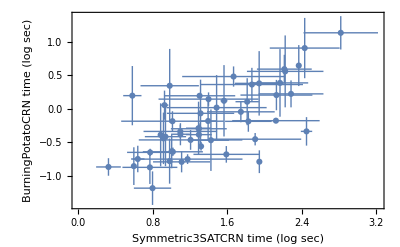

```mathematica
ListPlot[Log[10,DeleteCases[data,blank]],Frame->True,FrameLabel->{"Symmetric3SATCRN time (log sec)","BurningPotatoCRN time (log sec)"}]
```

BurningPotatoCRN is typically about 30x to 100x faster than Symmetric3SATCRN for problems of these sizes (5 to 10 variables, 20 to 40 clauses or so).    Is this consistent with (a) avoiding the wasted random-walk time during wire communication, and/or (b) a more effective stochastic local search algorithm?  It is not clear which is the case.

```mathematica
Module[{n=20,m,trials=100}, (* Matt Bauer did 1000 trials each, but this is already taking all day to run... *)
bauerdata=Table[blank,{m,70,90,2}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,m];TimeBurningPotatoCRN[problem],trials];
bauerdata[[index]]={m/n,Around[Mean[times],StandardDeviation[times]]};
Print[index,": ",bauerdata[[index]]],
{m,70,90,2}]
];
```

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

1: {7/2,16.53.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

2: {18/5,26.89.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

3: {37/10,19.41.}

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

4: {19/5,22.48.}

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

5: {39/10,34.104.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

6: {4,46.86.}

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

7: {41/10,61.119.}

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

8: {21/5,61.129.}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

9: {43/10,0.31.510^3}

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

10: {22/5,181.761.}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True

11: {9/2,191.439.}

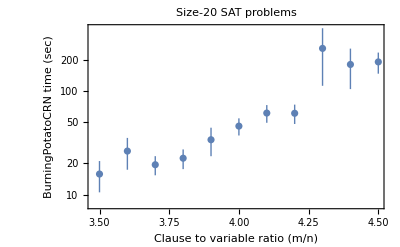

```mathematica
(* show std error of the mean bounds rather than sample std dev. since trials=100, sem=std/10. *)
ListLogPlot[bauerdata/.Around[v_,e_]:>Around[v,e/10],Frame->True,FrameLabel->{"Clause to variable ratio (m/n)","BurningPotatoCRN time (sec)"},PlotLabel->"Size-20 SAT problems"]
```

```mathematica
bauerfit=Fit[bauerdata/.Around[v_,e_]:>Log[10,v],{1,x},{x}]
```

-3.0908+1.20395 x

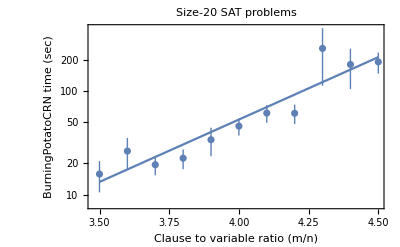

```mathematica
Show[
ListLogPlot[bauerdata/.Around[v_,e_]:>Around[v,e/10],Frame->True,FrameLabel->{"Clause to variable ratio (m/n)","BurningPotatoCRN time (sec)"},PlotLabel->"Size-20 SAT problems"],
LogPlot[10^bauerfit,{x,3.5,4.5}]
]
```

About a 10-fold slow-down over this range of clause-to-variable ratios is what Matt saw as well.  Since his C++ code simulated the abstract algorithm for his design, and did not take into account the time spent on signals traveling along wires in the surface CRN, the increased difficult he observed presumably had to do with exploring the search space itself.  Similarly, since the surface CRN simulated here will have approximately the same wire lengths (a 10% increase in the number of clauses will only make wires 10% longer), the slower times to solve the problems have to do with the efficiency of the search itself. 

While it’s encouraging that this surface CRN can reliably solve 20-variable (although some, like AdlemanSAT, are not so fast...) it is a far cry from the well-mixed WalkSATCRN, which can typically solve 500-variable 3SAT problems (ratio 4.2) in under 100 seconds.  (And size 50 in under 0.1 seconds on average.)

```mathematica
TimeBurningPotatoCRN[AdlemanSAT]
```

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1243.47 sec)

1243.47

```mathematica
easy10problem=SolvableRandomKSAT[3,10,Round[4.2*10]];
```

```mathematica
easy10times=Table[TimeBurningPotatoCRN[easy10problem],1000];
```

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.704935 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.65944 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.654209 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.15263 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.444752 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.814244 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.726655 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.11349 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.62393 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.881561 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.64602 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.742555 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.398934 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.42589 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.67837 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.415318 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.7181 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.38216 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.775331 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.784166 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.25146 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.10958 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.34946 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.31822 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.519914 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.42336 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.98367 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.759698 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (7.1246 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.909547 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.02492 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.359327 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.52613 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.7085 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.499637 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.72635 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.39063 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.38716 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.491887 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.22575 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.768731 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.788066 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.41645 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.99236 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.9872 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.859382 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.78669 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.20711 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.987569 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.10861 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.603821 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.37675 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.33585 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (7.4001 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.03363 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.74075 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.653045 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.97465 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.43441 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.53064 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.53343 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (10.862 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.45187 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.833748 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.82701 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.48936 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.09553 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.847341 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.55178 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.574198 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.61712 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.42046 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.4723 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.05754 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.841896 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.50292 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (6.03685 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.478108 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.04389 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.763696 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.22361 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.735255 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.620719 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.607822 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.838447 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.11271 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.30182 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.64031 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.779218 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.79012 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.914569 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.833772 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.876801 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.08739 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.36923 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.97761 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.08143 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.10495 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.707776 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.837939 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.47026 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.98814 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.817408 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.308031 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.49043 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.0794 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.24698 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.53299 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.77558 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.51888 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.93408 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (4.87682 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.427098 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.633287 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.73306 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.9136 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.26888 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.63427 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.971925 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.36548 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.32079 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.657665 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.02811 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.331486 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.678508 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.672178 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.92531 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.648349 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.655554 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.11333 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.385993 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.700982 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.03812 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.65689 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.26446 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.19166 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.18146 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.45116 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.76419 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (6.8193 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.04382 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.817058 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.83859 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.24339 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.93242 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.43469 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.02729 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.26944 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.60864 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.06963 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.13238 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.755064 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.563159 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.72759 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.18893 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.728206 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (5.3567 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.37798 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.00121 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.838428 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.02682 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.47374 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.35068 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.7078 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.718397 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.02461 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.45316 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.19308 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.26277 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (5.75691 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.78395 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (9.47073 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.3669 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.6554 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.920301 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.31827 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.568613 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06335 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.04773 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.992194 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.34237 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.643464 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.05727 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.21543 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.55733 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.62574 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.88924 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.31672 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.18821 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.69812 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.06387 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.83905 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.26222 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.10059 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.78316 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.09819 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.86625 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.780518 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.52134 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.22667 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.30367 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.571671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.43423 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.72596 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (6.57188 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.831255 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.04362 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.71862 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.97616 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.924524 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.42102 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.74368 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.20219 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.62635 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.830088 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.81671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.02789 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.91715 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.66602 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.937254 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.55372 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.779973 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.841359 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.62508 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.726404 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.743655 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.69019 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.84692 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.59157 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.15802 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.66825 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.25663 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.15611 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.82347 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.61137 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.732812 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.55637 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.3046 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.6199 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.08412 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06199 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.9543 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.877511 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.77402 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.74022 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.0926 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06523 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.553081 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.85816 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.996286 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.682785 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.772717 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.25183 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.934897 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.440958 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.64568 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.923853 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.425237 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.05431 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.727738 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.79417 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.887249 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.00343 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.68309 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.23515 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.06614 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.924878 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.518207 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.74381 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.16373 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (3.18211 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.68595 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.73056 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.81897 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.18485 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.407099 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.96257 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.23882 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.20158 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.30501 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.38286 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.20104 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.10993 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.14788 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.867888 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.68583 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.714334 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.832235 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.69372 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.358072 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (6.23282 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.27873 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.67313 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.55311 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.06022 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.64723 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.08326 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.52859 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.446671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.544206 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.20452 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.872276 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.16736 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.701086 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.1689 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.05658 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.665126 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.69732 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (5.97016 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.456562 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.86781 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.692967 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.03739 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.07877 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.941802 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.08593 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.60574 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.787375 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (6.81506 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.63415 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (2.92671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.702216 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.26375 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.65612 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.06915 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.388689 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.50158 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.05371 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.857891 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.73304 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.467801 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.558537 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.17381 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.67527 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.09317 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.73259 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.588785 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.83905 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.21224 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.915856 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.828561 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.64447 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.1709 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.93891 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.85456 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.75893 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.638203 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.837458 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.20394 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.586277 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.70745 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.38036 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.80797 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.23897 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.94064 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.18322 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.45822 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (2.28479 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.675122 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.13901 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.78094 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.46227 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.644907 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.89204 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.5792 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.736345 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.03457 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.36584 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.758744 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.96348 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.440178 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (4.90836 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.60778 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.51543 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.53641 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.02661 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.782984 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (6.28906 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.32947 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.17147 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.896436 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.957142 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.918009 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.07125 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.27425 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.16634 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.80321 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.81444 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.09976 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.339811 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.14147 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.18627 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.02213 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (5.23926 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.86793 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.728268 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (2.57474 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.681174 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.20018 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.704056 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.08948 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.805179 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.515428 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.15039 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.32048 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (5.84777 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (6.04556 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.46734 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.08975 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.31863 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06982 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.17637 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.50566 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.13671 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.36018 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.98195 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.76155 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.72198 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.802595 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.9219 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.820588 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.725 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.41886 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.503455 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.600882 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.72653 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.75533 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.08363 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.12463 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.44003 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.87686 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.02435 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.20623 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (4.17797 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.16332 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.04825 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.29331 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.20649 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.733345 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.578234 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.4865 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.51514 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.943531 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.357609 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.81216 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.65101 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.07906 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.3745 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.775992 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.20323 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.64706 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.999847 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.7417 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.22639 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.24951 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.702103 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.385389 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.78065 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.618663 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.53564 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.11626 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.49457 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.958643 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.763 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.712227 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.44836 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.21638 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.46721 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.06238 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.30557 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.547898 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.876831 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.564985 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (9.87421 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.80303 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.900954 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.362668 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (6.14227 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.616833 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.53173 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.628601 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.80319 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.17346 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.65079 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.783174 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.289502 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.4204 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.30273 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.06717 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.83339 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.54703 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.66193 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.652962 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.912258 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.33474 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.750375 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.830261 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.73006 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (4.97151 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.05864 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.825272 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.38909 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.873284 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.67996 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.387618 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.82061 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.614855 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (3.02354 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.05151 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.438705 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.6621 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.87454 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.539232 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.844382 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.03966 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.664544 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.536177 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.604884 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06024 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.21445 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.95047 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.93182 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.751704 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.67355 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.92204 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.9851 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.12016 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.30357 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.87116 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (9.68468 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.63267 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.40111 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.09828 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.981313 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.93988 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.588866 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.68358 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.43556 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.66539 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.36693 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.5095 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.30888 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.87483 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.996817 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.809657 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.696424 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.10183 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.33836 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.02564 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.33592 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.93289 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.526951 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.05336 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.30471 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.61577 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.60157 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.29348 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.644803 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.45595 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.55496 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.75458 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.10225 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.12441 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.78377 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.419352 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.31351 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.39137 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.42252 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.29875 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.68269 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.61119 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.8448 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.505779 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.11545 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.3403 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.68942 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.718923 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.1147 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.45256 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.928033 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.23 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.841069 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.63871 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.634308 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.25107 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.830775 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.11761 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.69342 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.92218 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.63882 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.439508 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.18333 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.84343 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.19928 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.07113 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.00547 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.78482 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.962147 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.2964 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.99191 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.39615 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.03389 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.98189 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.33305 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.80628 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.35345 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.942636 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.47976 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.494659 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.548586 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.568296 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.08397 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.32124 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.860695 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.18178 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (6.13142 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.432966 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.977105 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.20334 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.52284 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.325016 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.61851 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (8.1317 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.83363 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.545 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.911282 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.832964 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.78878 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.54978 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.637955 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.7124 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.45368 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.763254 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.63839 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.00609 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.64068 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.74976 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.13031 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.08322 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.28316 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.06767 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.0094 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.37552 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.52352 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.32592 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.90782 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.23469 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.75231 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.98796 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.77558 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.01398 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.05622 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.20394 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.80714 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.430358 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.88968 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (3.09163 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.934243 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.09181 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (5.10356 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.74082 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.494946 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.83809 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (2.78891 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.618135 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.53412 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.28472 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.35752 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.50053 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.08996 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.67309 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.524165 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.40598 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.16956 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.06577 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.59705 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.40041 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.67737 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.6798 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.99817 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.637215 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.11905 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.6659 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.38511 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.26564 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.272774 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.30733 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.7843 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.514429 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.73292 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.14052 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.61347 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.510412 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.13871 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.43786 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.6953 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.86677 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.78951 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.07947 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.481125 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (3.31676 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.62174 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.22147 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.53626 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.870313 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.311006 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.24178 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.70897 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.37068 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.59288 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.385126 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.30286 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.862532 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.20977 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.04216 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.80632 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.21637 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.96403 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.41099 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.904966 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.98402 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.98039 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.64298 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.751076 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.87044 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.11342 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.49089 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.58939 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.36482 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.936719 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.28987 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.07857 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.17352 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.86008 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.40826 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.96666 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.789704 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (6.33449 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.02007 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (6.41499 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.58688 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.15028 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.692776 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.556859 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.596031 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.84034 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.22907 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.38683 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (5.60217 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.15317 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.47677 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.830694 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.19027 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.807922 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.06104 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.31818 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.55425 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.43284 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.60616 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.5308 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.742273 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.674284 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.658237 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.43586 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.44563 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.8194 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.45025 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.625588 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.32406 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.32131 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.62705 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.943906 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.14803 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.2638 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.881791 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.14425 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.97074 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (5.27954 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.622753 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.586639 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (2.86622 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.805181 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.4208 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.01813 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.668429 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (0.703013 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.22448 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.929612 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.0284 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.34346 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.80719 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.483406 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.15309 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.94598 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.49314 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.829734 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.23961 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.78805 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.334685 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.688469 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.89186 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.463249 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.38724 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (7.93017 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.17485 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (4.40842 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.58956 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (6.3024 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.42806 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.97278 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.8664 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.3171 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.75807 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.68501 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.883276 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.14985 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.94567 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (5.58331 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.15578 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.40333 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.72687 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.83338 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.26829 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.84663 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.50332 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.46767 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.36758 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.97719 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.42577 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.60914 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.05983 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.63521 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.92886 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.0859 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.761714 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.730874 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.28707 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.700799 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.31421 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.495205 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.13884 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.25985 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.302166 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.11936 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.49061 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.25142 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.04177 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.652513 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.36175 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.815161 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.17718 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.60209 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (4.01971 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (7.9192 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.1161 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.58749 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.97323 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.37483 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.54517 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.42672 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.897045 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.109 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.46725 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.74849 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (3.10905 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.92068 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.05543 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.89186 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.51129 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.76513 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.60053 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.878578 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.81566 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.82085 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (6.20481 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.4825 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (7.1589 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.19089 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.49017 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.83298 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.71177 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.45342 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.984072 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.50695 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.39496 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.2345 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (10.7107 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.573854 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.471967 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.09242 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.16167 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.56714 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.58988 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.869224 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.739635 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.45399 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.638763 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.974686 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.24601 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.989647 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.818565 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.44239 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.721102 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.72758 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.54435 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.77529 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.20861 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (3.2798 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.49661 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.02653 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.831535 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.539444 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.79762 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.778286 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.38374 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.04498 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.34018 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.04595 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.44208 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.970748 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.697909 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.522915 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (4.19908 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.68822 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.538542 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.48037 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.02469 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.409849 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.585597 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.60907 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.23113 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.80431 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.77712 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.77589 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.5314 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.44001 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.471554 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.576542 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.00465 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.94619 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (5.1128 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (5.70894 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.775087 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.932834 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (4.24321 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.09383 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.54363 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.525828 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.76211 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.852692 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (4.16768 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.06119 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.72062 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.66313 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.0306 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.60737 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.623739 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.06703 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (3.89575 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.605793 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.20109 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.672329 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (2.88034 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.68442 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.758388 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.62737 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.99443 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.475203 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (5.25103 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.486832 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.15724 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.964555 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (4.3652 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.94688 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.78858 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.868811 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.48466 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (2.81732 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (5.83405 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.568232 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.40719 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.76997 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.42851 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.899254 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.79279 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (1.90787 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.76828 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.87671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (2.48514 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (3.05849 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (0.686477 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.996359 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (2.9795 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (1.41103 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.38646 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.881272 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (2.65601 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (4.64458 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (5.50856 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (1.53767 sec)

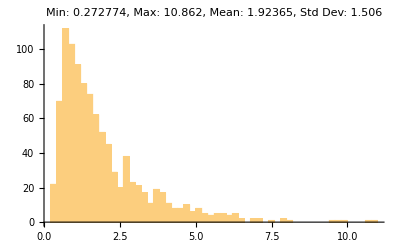

```mathematica
Histogram[easy10times,50,PlotRange->All,PlotLabel->"Min: "<>ToString[Min[easy10times]]<>", Max: "<>ToString[Max[easy10times]]<>", Mean: "<>ToString[Mean[easy10times]]<>", Std Dev: "<>ToString[StandardDeviation[easy10times]]]
```

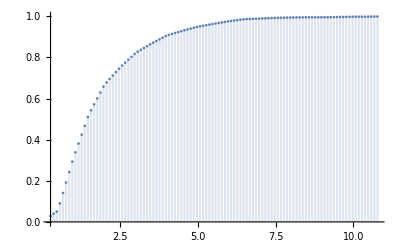

```mathematica
DiscretePlot[CDF[HistogramDistribution[easy10times],t],{t,Min[easy10times],Max[easy10times],0.1}]
```

```mathematica
easy15problem=SolvableRandomKSAT[3,15,Round[4.2*15]];
```

```mathematica
easy15times=Table[TimeBurningPotatoCRN[easy15problem],1000];
```

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.47317 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.17333 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.25242 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.63092 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.95927 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.42815 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.66475 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.48104 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7181 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.98227 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.90612 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.56924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (8.81035 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.38775 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (11.0422 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.69614 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.4762 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.80437 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.41375 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.68309 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.14421 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.18191 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.99151 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.56939 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.13683 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.73196 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.9653 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.13808 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.95826 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.21858 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.19574 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.64275 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.29002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.3126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.4167 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.47024 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (16.8777 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.16786 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.07022 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.45331 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.64793 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.3214 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.25658 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.75114 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.2697 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.903464 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.89975 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.41097 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.63455 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.49625 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.19582 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.67425 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.15646 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.56674 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.18378 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.53113 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.24078 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.88666 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.68486 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.50346 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.34823 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.80318 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.97119 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.1935 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.08612 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.02808 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.75136 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.11856 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7889 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (17.836 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.8104 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.7856 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.65847 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.32909 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.54074 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.32701 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.92689 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.72774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.35822 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.86585 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.14995 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.08472 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.78876 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.71047 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.87301 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (24.8933 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.24884 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.6255 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.50216 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.17583 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.44307 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.10179 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.6809 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.0264 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.93399 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.64737 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.59384 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.00841 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.88204 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.93288 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.77381 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.4666 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (17.8477 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.03025 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.5577 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.00508 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.24533 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.97991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.0806 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.23593 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.55685 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.53225 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.9901 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.84889 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.47774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.85866 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.80422 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.67983 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.17581 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (12.1215 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.54759 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.52549 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.6787 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.87215 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.27436 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.31546 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.46182 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.37195 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.1011 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.49742 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.4414 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.98157 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.3514 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.23363 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.13298 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.06746 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.35425 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.84604 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.27569 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.55119 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.10449 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.36823 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.96752 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.9595 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.81859 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.18397 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.28169 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.77691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.48953 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.94174 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.69977 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.48882 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.61149 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.37831 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.27421 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.2997 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.0093 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.38148 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.53844 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.2913 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.58029 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.90069 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.2607 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.23466 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.07227 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1159 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.26367 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.51232 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.62948 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.365 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.15596 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.00387 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (25.1122 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.62674 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.29064 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.43216 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.87744 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.55916 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.77564 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.40818 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (16.2697 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.34679 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.4364 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.44434 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.11832 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.47652 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.11833 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.08639 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.5066 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.80087 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.3326 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.90506 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.84797 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.91825 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.5674 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.8265 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.96363 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.03932 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.8817 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.01552 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.7378 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.15749 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.04033 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.66462 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.8787 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.96612 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.2968 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.64086 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.75255 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7148 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.46327 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.6065 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.31853 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.45968 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.45099 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.72514 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.30499 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.15479 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.02681 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.9742 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.56044 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.135 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.60527 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.70015 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.87137 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.74772 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.93164 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.996909 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.66525 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.96649 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.11248 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.22519 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.98713 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.461 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.28125 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.05417 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.62472 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (19.8617 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.55886 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.12627 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.43865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.19629 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.39267 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.6437 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.87116 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.75617 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.05642 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.38875 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.35648 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.63412 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.09763 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.18017 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.915284 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.64832 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.13626 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.376 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.43524 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.02688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.90968 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.981684 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.30923 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.08658 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.604 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.0999 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.77005 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (12.2413 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.83853 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.68812 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (8.67863 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.69689 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.95991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.80043 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.85933 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (23.3233 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.47257 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.43553 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.61155 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.33067 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.23985 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.19543 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.13803 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.14649 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.13407 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.00712 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.29802 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.05662 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70396 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.96668 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.81847 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.87662 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.81862 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.90284 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.68245 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.5071 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.78302 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.88646 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.10174 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (16.3218 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.1812 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.66528 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.979 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.43007 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.59217 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.47883 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.6195 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.06906 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.88891 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.89604 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.1046 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.46867 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.25958 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.04335 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.84691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.90003 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.5736 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.01206 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (12.7554 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.17361 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.34635 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.783804 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.0958 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.6404 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.52621 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.11667 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.27597 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.86059 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.9939 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.7942 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.65769 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.0525 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.09105 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.750624 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.2464 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.66417 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.16534 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.23904 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.38526 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.58439 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.58913 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.09065 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.43548 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.25356 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.46773 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8531 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.90405 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.40321 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.01816 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.54761 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.85865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.28732 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.84257 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.72215 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.92013 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.2406 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.87378 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.43316 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.3213 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.0244 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.75963 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.2969 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.90147 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70743 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.31331 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.16835 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.7539 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.92312 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.39074 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.70844 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.0547 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.54828 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.32284 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (15.4766 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.621 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.46684 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.81381 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.20497 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.79335 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.82186 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7706 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.89581 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.27613 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.64127 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.59109 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.90985 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.93734 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.35527 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.6311 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (27.6622 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.21571 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.07649 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.45941 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.79026 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.06011 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.47406 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.55038 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.85771 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.01289 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.46626 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.60647 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.36581 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.1207 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.9159 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (27.883 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.68031 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.52946 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.88195 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.93964 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.6821 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.71903 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.906364 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.43689 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.60866 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.87487 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.5773 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.76666 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.0772 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.31853 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.61408 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.06263 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.4044 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.42176 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.40916 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.28244 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.5028 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.14009 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.71555 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.09674 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1302 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.72216 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.21594 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.77226 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.28599 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.9298 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.24734 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70506 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.0157 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1062 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.14357 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (16.501 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.9358 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.60331 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.37491 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.69711 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.69948 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.9574 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.6595 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.69313 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (13.4693 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.51348 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.0431 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.31161 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.86117 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.37123 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.89004 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.37451 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.35776 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.2453 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.24344 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.11989 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.81916 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.8912 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.845644 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.20929 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.914524 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.2622 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.82012 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (21.4254 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.379 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.34791 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.6835 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.93584 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.1607 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.98127 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.36954 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.02002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.16573 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1679 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.23489 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.37795 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (0.635141 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.90828 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.37934 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.9579 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.58797 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.5306 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.671 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.32131 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.40067 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.43582 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.81382 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.55413 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.18341 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.32541 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.34699 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.38661 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.73403 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.0364 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.76345 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.851788 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.82802 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (16.8536 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.30506 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.89739 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.86204 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.55475 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (18.4067 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.0909 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.10489 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.09428 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.194 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.88529 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.13105 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (11.1817 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.4221 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.02497 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.19353 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.51312 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.55454 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.44467 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.15592 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.12055 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.09086 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.1665 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.38404 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.71876 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.8111 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.93415 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (15.6024 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.6139 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.54783 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.3637 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.31621 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.62627 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.649 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.89689 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.98642 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (16.3198 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.43162 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.40559 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.21838 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.08888 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.9737 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.45221 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.8356 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.7504 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.94963 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.58429 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.72126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (8.56587 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.53882 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (21.1392 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.58189 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.18983 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.4634 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.6616 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.38448 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.81351 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.6316 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.26392 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.978175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.10746 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.29961 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.51609 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.11845 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.8233 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.1829 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.3336 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.66705 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.49124 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.64099 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (16.1424 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.62563 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.19714 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.52839 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.40839 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.58269 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.07327 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.5777 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.1337 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.65964 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (26.0487 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.48121 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (25.5221 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.8939 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.71499 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.54354 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.3633 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.82715 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.63645 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.9612 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.91941 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.39577 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.5626 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70944 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.74031 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.88686 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.48616 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.41897 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.21475 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.93175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.0072 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8928 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.1923 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.12208 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.05467 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.40328 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.22542 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.79729 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.28832 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.0875 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.99389 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.10416 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.2164 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.81077 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.24402 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.46234 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.24897 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.99098 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (23.4988 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.3299 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.68236 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.536 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.69776 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.92163 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.46966 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (24.3368 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.965 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (19.218 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.26443 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (22.5631 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.97984 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (12.7396 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1124 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.26105 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.26881 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (23.4163 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.99597 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.16998 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (28.0197 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.02725 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.35501 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.73415 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (11.5471 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.24649 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.61085 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.84837 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.84603 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.58175 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.2548 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.98288 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.6279 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.5061 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.72415 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.5101 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.48038 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.32035 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.9169 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.6588 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.26066 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.84452 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8366 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.43633 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.14531 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.39182 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.6741 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7729 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.34162 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (15.0711 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.7705 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.1007 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.61229 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (23.415 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.70434 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.60354 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.6729 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.26829 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.38064 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.7511 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.4955 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.73324 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.46368 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.97483 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.18261 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.87351 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.31392 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.27536 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.7821 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.65157 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.82762 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.72557 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.35222 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.06837 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.04588 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.15636 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.80479 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (24.7977 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.48501 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.26619 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.03002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.8234 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.4915 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.38161 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.42884 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.52419 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.97541 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.8448 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (28.7313 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.82179 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.38388 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.54845 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.71987 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.82782 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.4538 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.8274 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.28121 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.3925 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.14742 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.6795 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.1122 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.45047 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.87202 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.32194 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.82775 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.7754 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.89468 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.1018 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.71997 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.29428 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.10169 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7046 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.5126 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.27898 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.59916 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.95697 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.82518 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.6318 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.79669 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (31.8617 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.1207 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.8715 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.6116 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.37208 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.40835 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.514 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.11774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (21.1207 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.34964 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.72177 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.48623 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.64356 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.3496 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.72401 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.62634 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (29.811 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.86981 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.92235 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.35585 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.008 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.17349 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.8146 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.87517 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (14.4979 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.13298 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.97 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.29447 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.1563 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8968 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.99887 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.5707 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.08232 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.9645 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.72165 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.91168 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.74633 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.36656 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.25721 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.73346 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.41523 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.4405 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.10246 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.51577 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.5092 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (27.0705 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.70849 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.87158 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7584 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.00205 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (29.3186 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.02226 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.47127 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.75063 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.2544 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.74159 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.50543 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.91202 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.4295 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.63081 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.50038 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.38611 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.54773 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.20723 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.70742 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.61954 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.10885 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.44029 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.0973 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (0.748163 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.71355 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.0422 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.2321 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.88132 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.5959 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.19816 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.51086 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.89472 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.2222 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.5856 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.5534 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.11303 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.44987 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.39938 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.02741 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.33711 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.32039 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.61821 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.74147 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.94026 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.1227 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.87824 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70567 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.41008 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.33298 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.8831 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.1601 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8134 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.68516 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.73815 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7283 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (8.08682 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.71833 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.0385 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.40149 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.70414 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.41818 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.9906 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.43852 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.00841 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.7821 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.61171 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.9698 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.83171 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.74519 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.58693 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.49263 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (19.9227 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.324 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (20.4856 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.03153 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.3647 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.36805 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.0871 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.51859 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.5046 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7378 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.25531 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.8471 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.52707 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.7316 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.95669 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.27122 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (5.68591 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.86131 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.4917 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.7898 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.66813 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.0218 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (13.5954 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.9744 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.56081 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.04386 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.4091 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.35845 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.49538 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (9.55083 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.06119 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.47264 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.0447 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.13788 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.34625 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.02569 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.79829 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.5502 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.25577 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.34188 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.73362 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.23536 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.02082 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.15132 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.99772 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.73399 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (13.0273 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (8.1875 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.79279 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.22986 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.3596 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.99976 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.50943 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (22.614 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (8.0796 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.24788 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (13.5785 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.39452 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.44385 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.1217 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (20.9112 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (25.8252 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (20.103 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.0781 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (6.15701 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.83343 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.608 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.7917 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.73552 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.5163 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.1814 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (4.72969 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.22325 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.86722 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.9602 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.5896 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.1928 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.0247 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (9.04764 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.04213 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.78934 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (28.0989 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.8354 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (19.1216 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.0756 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.2044 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.70346 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (17.3899 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.72384 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.2316 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (18.1381 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.8642 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.7588 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.46373 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (15.617 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.64595 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.964 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.52124 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (11.6735 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.02643 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.53741 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.37521 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.66696 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.79423 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.98543 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (16.6851 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.80864 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.25452 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.19977 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.2008 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (7.45349 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.28558 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.54582 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (1.73944 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.41702 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.32878 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.11714 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.18698 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.19485 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.71255 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (7.89844 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.53702 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (15.4535 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (10.3073 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (12.0399 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (21.4501 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (5.56016 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.5111 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.01734 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (14.4749 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.29441 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.11842 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (6.06836 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.86161 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.93711 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.82201 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (2.36571 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.51275 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (1.38804 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.74435 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.03692 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.84865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (10.0208 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (17.4612 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (4.67108 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (2.80531 sec)

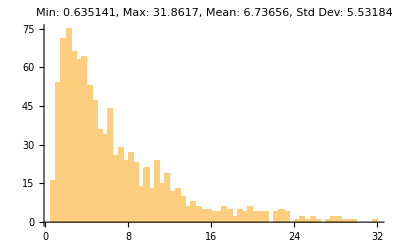

```mathematica
Histogram[easy15times,50,PlotRange->All,PlotLabel->"Min: "<>ToString[Min[easy15times]]<>", Max: "<>ToString[Max[easy15times]]<>", Mean: "<>ToString[Mean[easy15times]]<>", Std Dev: "<>ToString[StandardDeviation[easy15times]]]
```

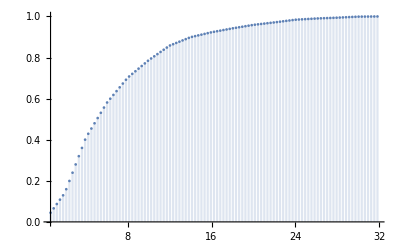

```mathematica
DiscretePlot[CDF[HistogramDistribution[easy15times],t],{t,Min[easy15times],Max[easy15times],0.3}]
```

```mathematica
easy20problem=SolvableRandomKSAT[3,20,Round[4.2*20]];
```

```mathematica
easy20times=Table[TimeBurningPotatoCRN[easy20problem],1000];
```

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.0455 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.5389 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.1062 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (37.8262 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.6351 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.05682 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.4924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (133.792 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (118.426 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.42941 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (58.4758 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.45572 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.387 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (48.3638 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (74.3991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (5.81684 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.509 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (20.9462 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (52.2617 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.8785 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.44219 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.86731 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.6298 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (115.357 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.3423 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (45.2236 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (49.6505 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (125.762 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (67.1201 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.4269 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.9542 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (65.847 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.0757 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.8238 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.9884 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.54443 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (23.5576 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (70.617 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (74.7867 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.4174 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.85305 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (63.0026 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.5524 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (57.2219 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (57.3506 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (51.1871 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.488 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.5126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.9691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.4885 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (93.5207 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.134 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (44.086 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.0094 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.1399 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.4559 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.8431 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.0396 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.5535 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.2455 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (52.9883 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (133.648 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.4683 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.88301 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.8039 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (56.2591 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.281 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (245.978 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.5783 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.101 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (49.0093 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (130.802 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.1747 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.2178 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (43.2723 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.0271 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.36842 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (72.335 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.2348 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (65.1645 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (85.8305 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.9539 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.6334 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (71.0894 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (60.7421 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (100.793 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.3403 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.59481 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (60.2163 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.494 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.8866 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.6135 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.02976 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.8424 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.85547 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.5897 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (46.4589 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.0036 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.1896 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.36749 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.5281 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (61.5519 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (58.817 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.8225 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.042 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.36922 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (54.6365 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.25363 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.1127 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (204.92 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.7731 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.4583 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (62.9493 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (55.6862 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.36639 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.9814 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (174.745 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (64.6701 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (44.0079 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (51.9298 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.28381 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.1927 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.1286 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.3157 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.47411 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (5.98539 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.72641 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.0225 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (77.383 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (73.9904 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (99.1753 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (91.9947 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.38437 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.7432 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.0809 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (43.4862 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.1855 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.42001 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.2675 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.8508 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.06808 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.38705 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.9591 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (30.5994 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (52.0134 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (36.5749 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (71.145 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (96.1197 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.45571 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (35.8563 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.1149 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (34.7223 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (70.568 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (50.6023 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.4482 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.2078 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.4117 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.431 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.8783 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.1487 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.65026 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (77.4246 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.63097 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.3685 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.8478 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.43075 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.5909 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.8497 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.7699 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.2257 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (70.1359 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.0127 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (42.5458 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.7602 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.9663 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (106.814 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.2509 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.2003 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.3356 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.9971 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (50.1688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.2996 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (59.7606 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.34568 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (122.136 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.8433 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.503 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (82.7088 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.8451 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.8 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.84691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.7508 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.4846 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.4399 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.0793 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.41179 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.015 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.4078 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.2111 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.118 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.0973 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (93.2137 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (117.278 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (95.3952 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.0256 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.3181 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.0545 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.52 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.788 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.33927 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.4443 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.2089 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.8656 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.26034 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.6265 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.0469 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.0103 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.11705 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.2838 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (91.7244 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.15187 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.91944 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.4691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (64.0568 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.5929 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (70.5018 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.996 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.9931 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.6321 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.7673 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.9401 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (44.5342 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.0779 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.3365 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.7907 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.0028 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (64.6958 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.06007 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.6409 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.297 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.8629 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.8817 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.5104 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (59.2813 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.2295 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (55.6988 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.42589 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (86.0189 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.92924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (5.99903 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.7618 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (64.6167 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (106.082 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.5441 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.7651 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.83003 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.8387 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (68.4623 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.0597 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.061 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.7802 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.76531 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.8308 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.61672 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (71.4523 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.6107 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (66.906 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (56.7175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.43866 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (67.828 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.41716 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.81518 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (45.3407 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.4886 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.4413 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.49026 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (43.8489 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (47.715 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (68.4761 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.2091 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (30.6392 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.5947 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.3835 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.536 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (52.6413 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (47.1911 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.34849 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (52.4939 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (71.2309 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.8725 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (89.7738 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.0815 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.4145 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (37.3908 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.1789 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.1915 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.6769 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.2836 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.43558 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (63.2106 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (66.6126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.93161 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.8296 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (49.7262 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2648 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.1176 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (61.8922 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (49.4559 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.66072 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (66.0361 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.7181 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (35.9717 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (26.8502 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.4182 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.87486 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.20698 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.0189 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.8854 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.1421 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.13345 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.8992 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.446 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (63.3821 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.00473 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.09257 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (42.3636 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (40.5256 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (78.8318 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.2575 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.9258 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.3628 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.41628 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (41.5285 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.2774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.75332 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (75.9739 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.4846 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.96802 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (43.5286 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.2282 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.3873 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (65.4759 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.29153 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.43655 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (140.931 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (103.419 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.3311 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.833 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.177 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.2365 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.16675 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.7256 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (120.578 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (56.2321 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (77.1739 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2211 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (41.3907 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (55.4085 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.1277 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.5223 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.30454 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.349 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (37.4701 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.95436 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.58933 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.5909 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (121.006 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.4917 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (26.5903 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.508 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.2623 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (65.6187 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.26314 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.5261 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (44.0227 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.605 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.60137 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.6829 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.41688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (83.2777 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.39777 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.8991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.3592 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (48.6789 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.3258 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.28291 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.2029 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.2669 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (117.346 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (41.1445 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (72.8757 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.8294 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (159.537 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (43.9426 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.49795 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.185 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.1009 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.8241 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (82.4193 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.746 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.8357 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.1275 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.8828 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (41.6407 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (92.734 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.1844 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (33.953 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.7455 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.39263 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.03793 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.2967 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.59099 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.687 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (67.8175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.6827 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (160.211 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.82256 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.8415 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (94.0427 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (53.6278 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.90323 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.2384 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.4984 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.7947 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.5766 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (62.032 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.9578 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (44.7301 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (40.75 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (155.927 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.0175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (45.8237 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.6649 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.2428 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.1957 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (64.0986 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (103.265 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (64.4537 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.4672 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (119.621 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.39756 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.5561 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (69.9836 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.1781 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.4587 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (41.4162 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.71837 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (66.6049 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (60.895 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.9988 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.83561 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.4849 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (39.4074 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.06774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.466 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.6861 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.6986 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.36698 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (35.5146 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.2262 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.1076 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (23.6601 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (90.0803 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.9217 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.6169 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.7099 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.629 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.7534 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.9835 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.9102 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.0751 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (59.5667 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.3451 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.36403 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (65.6728 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.9563 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.0207 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (36.1119 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (57.4451 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.8388 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.87308 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (68.9352 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.27078 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (227.367 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.511 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (54.0758 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (113.284 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (73.8622 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.4347 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.1991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (39.3116 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (187.32 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (60.5271 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.72234 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (27.2841 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.0363 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.76627 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.64605 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (79.7947 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (75.7697 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.96125 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.5079 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.72304 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (53.9982 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (134.941 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.4575 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.61352 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (73.098 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (102.035 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (81.2512 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.6538 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.4774 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.4794 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.7364 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.4372 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.2817 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.3675 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.645 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.5421 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.7588 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (48.6262 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.33148 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.4266 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (70.1684 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.6465 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.60905 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.8452 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.9892 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.6293 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (57.1116 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (63.5606 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.74361 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.541 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (77.9514 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.88491 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (63.3662 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.3116 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (170.162 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.7969 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.6641 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.09355 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (76.9557 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.3584 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.998 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.0927 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.3081 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.4657 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.1651 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (64.9073 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.6555 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.0395 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (72.8849 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (140.6 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.16643 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.322 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (60.5869 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.2348 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (37.1881 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (74.5412 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.9671 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.5865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (50.6479 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.0769 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (23.5434 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.7273 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (114.585 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.48726 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.01216 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.55979 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.3503 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.8719 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.27343 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (75.8739 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.0903 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.67319 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (36.3214 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (50.6538 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (40.7477 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (61.6619 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.7523 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.3701 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (148.377 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.8528 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.4022 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.3171 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (99.5456 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.45055 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.0374 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (91.9102 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.5626 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.2794 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.40292 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.8744 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.1945 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.986 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.2875 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (104.653 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (12.7398 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (121.042 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2129 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (63.6505 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.804 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (85.1101 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (67.7002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (60.9943 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (101.063 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.2638 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.9418 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (77.0494 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.70709 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.8264 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.3172 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (90.7991 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (41.6002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.568 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (64.7403 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.0168 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.8907 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (49.105 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.4631 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.992 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.4769 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.60252 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (27.4827 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (94.0526 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.8997 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.1575 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.0017 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.92632 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.1387 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (36.6203 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.9138 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (37.358 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (62.5438 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.0139 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (159.814 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.454 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.9582 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.0253 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.7791 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (188.081 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.70812 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.3608 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.2153 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.3643 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.02038 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (121.132 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.47968 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.1708 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.8384 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (91.5283 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (58.5682 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (44.754 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (102.211 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.992 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (71.557 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (76.2284 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (107.443 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.3691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.5529 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.74941 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (72.1073 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.6691 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.1421 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.3486 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.0905 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (31.569 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (42.4286 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (76.0919 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (98.3015 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (40.4565 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (93.1271 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (74.2843 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.855 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (75.8397 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.63302 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.64011 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.9437 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2199 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.6488 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (124.39 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.518 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (66.3688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (23.7776 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.35621 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (83.4327 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (40.4038 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (37.1729 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (69.1226 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (198.614 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.0533 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.867 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (65.2428 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (94.3017 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (30.5876 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.8737 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.6577 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.2869 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.963 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (140.472 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (42.999 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (95.5326 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (77.6248 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.64268 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.6705 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (37.3067 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (227.133 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (78.0777 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (129.742 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.63556 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.22483 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.5704 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.8978 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.394 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.5174 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (83.4095 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.2585 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.6396 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.0171 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.1636 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.39034 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.71397 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.4045 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.61288 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.58789 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (61.5465 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.8433 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.3222 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (89.5257 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (140.166 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.72252 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.2221 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (101.924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (95.7399 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (50.3449 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.62227 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.5313 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.0248 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (45.5753 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.0273 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.9039 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (54.2322 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (74.974 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (79.4076 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (68.4922 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (5.78702 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (100.1 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.5432 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.6039 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (50.8132 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.6424 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (73.0788 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (45.3041 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (50.3773 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (58.9465 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.8798 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (125.261 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.5266 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (81.5285 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (228.915 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (36.126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (64.5141 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (71.9557 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.4085 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.5864 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.64737 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (59.7463 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.0916 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.904 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.9461 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.7103 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (43.8901 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (167.67 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.2795 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (76.4248 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.835 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.75479 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.21061 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2955 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (20.744 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.20568 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.46769 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.46087 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.08553 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.1772 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.754 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.4479 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.74245 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (64.0865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.16753 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.05 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (40.5197 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (58.4371 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.33624 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (145.681 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (101.018 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.2313 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.0727 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (24.5627 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.5799 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.2852 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (47.9018 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.232 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (115.191 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.5912 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (77.6446 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (19.2733 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (34.0795 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (48.9918 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (44.5396 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (81.5331 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.26644 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (82.9969 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.4224 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.40583 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (83.872 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (29.7372 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.1847 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (37.7539 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (60.0095 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (22.8175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.6423 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.0259 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.01495 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.1095 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (44.863 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.5582 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (47.9146 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.846 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (36.5416 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (65.8201 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.6165 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.4108 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (97.1931 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (34.8699 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (127.493 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (15.5935 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.91786 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.3842 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.4304 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.39367 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.9666 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (72.3792 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (65.5779 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.1874 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (96.3924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (2.61754 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.2448 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (42.9989 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.25967 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (69.6179 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (24.7777 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (82.0362 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.4147 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (78.2531 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.1931 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.60983 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (69.1592 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (30.6763 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (154.894 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (109.894 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.6922 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.93528 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (28.5721 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.59925 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.5942 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.0827 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.86148 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (71.5038 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (82.7394 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (46.2974 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.1214 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (90.8725 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.78853 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (25.9608 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (44.1432 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (96.3192 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.58688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.4727 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.478 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.681 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (80.8932 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.4349 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.78276 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (33.0737 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.492 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.4939 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.29386 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (13.4723 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (57.3778 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.9266 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.56011 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.6933 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (45.4077 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (42.017 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.1184 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (32.1623 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.13085 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (47.5537 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (84.8493 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (36.3842 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.5951 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.2881 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (118.918 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.0761 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.5156 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.23371 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.9744 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (87.4172 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.5654 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (38.5755 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (27.9164 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (63.555 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.8694 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.87322 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.76955 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (34.3669 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (98.8352 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.6928 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (9.32661 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.88712 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.72965 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (35.9281 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (19.1896 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.7009 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (287.692 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (21.4487 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (61.3765 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.3175 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.54726 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (10.7936 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.5085 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.9 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (35.0489 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (27.3562 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (28.6868 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (120.489 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.1482 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (72.5868 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (50.4371 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (85.8816 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (185.613 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (6.73145 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (29.8183 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.2142 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (4.73764 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (16.6592 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.78359 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.1931 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.25216 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (86.1628 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.5326 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.8097 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (9.76312 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (13.6464 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (58.6304 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.2492 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (49.966 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.53751 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.6032 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (43.7002 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.4399 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.9873 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.02466 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (14.6802 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (60.0004 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.48712 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (38.6801 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (15.1154 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (18.0646 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (25.7118 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (11.2823 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.2095 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (152.671 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (61.965 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (26.8372 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.7961 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (151.191 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (44.6699 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.20308 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (20.5748 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (22.613 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.718 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.9495 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (1.51867 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (79.7272 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (50.401 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (20.7614 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.0167 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.11629 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (8.68796 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (27.0317 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (23.9247 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (30.3615 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (17.97 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (55.979 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (10.9876 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (57.8717 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (78.6205 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (16.6612 sec)

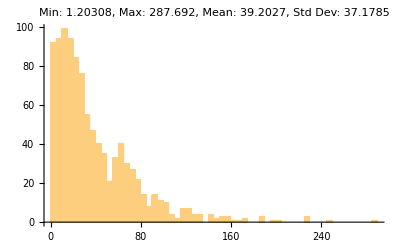

```mathematica
Histogram[easy20times,50,PlotRange->All,PlotLabel->"Min: "<>ToString[Min[easy20times]]<>", Max: "<>ToString[Max[easy20times]]<>", Mean: "<>ToString[Mean[easy20times]]<>", Std Dev: "<>ToString[StandardDeviation[easy20times]]]
```

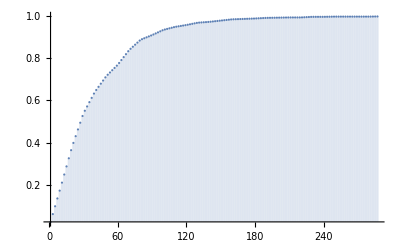

```mathematica
DiscretePlot[CDF[HistogramDistribution[easy20times],t],{t,Min[easy20times],Max[easy20times],2.0},PlotRange->All]
```

It’s nice to get a sense of what these runtime distributions might look like.  Of course, on specific different problems, they might be utterly and radically different.  But at least on these randomly generated instances, they share some qualitative features. 

What can we say regarding performance?  Modern SAT solvers use random restart; would that be valuable here?  Well, these are all runs starting from the same initial condition on the same problem, so it’s IID if one were to restart the search anew.  Hence, we can make claims about when it might be beneficial to reset all variables and start anew.  Let p(t) be the probability that the search will conclude at before time t (i.e. the cumulative distribution).   If we were to always restart immediately at t=s if no solution has been found yet, then it will require on average 1/p(s) starts (the first start plus all the restarts) before a solution is found, and hence the total time of the modified restart algorithm is < t_new > = s(1 / p(s) - 1) + t where 0 < t < s is the time to solution after the final restart.   The expected runtime after the last restart will actually be less than the expected runtime for the unmodified algorithm, < t >.  So we have < t_new > < s(1 / p(s) - 1) + min(s,< t>) < s/p(s).  For example, is we choose s such that p(s)=1/2then < t_new >  < 2 s.  This may reduce the variance (and even the mean) for long-tailed distributions of runtimes.  Using the empirical CDF, we can numerically calculate the value of s that gives the lowest upper bound on modified runtimes using restart, and see whether this is in fact less than the mean.  Nope, not here, surprisingly.  Maybe the problems need to get larger before the long tails are long enough...

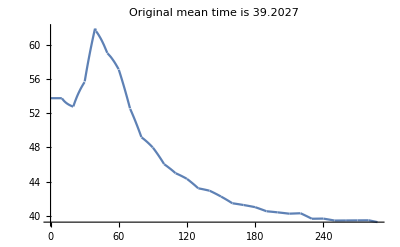

```mathematica
With[{mt=Mean[easy20times],xt=Max[easy20times],cdf=CDF[HistogramDistribution[easy20times],t]},
Plot[t/cdf+Min[t,mt]-t,{t,0,xt},PlotRange->All,PlotLabel->"Original mean time is "<>ToString[mt]]
]
```

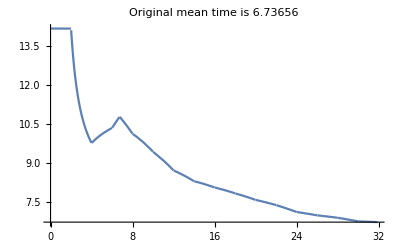

```mathematica
With[{mt=Mean[easy15times],xt=Max[easy15times],cdf=CDF[HistogramDistribution[easy15times],t]},
Plot[t/cdf+Min[t,mt]-t,{t,0,xt},PlotRange->All,PlotLabel->"Original mean time is "<>ToString[mt]]
]
```

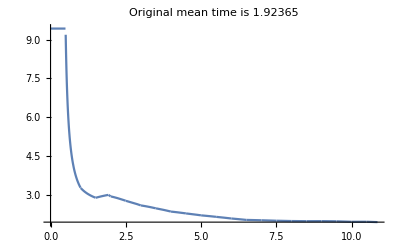

```mathematica
With[{mt=Mean[easy10times],xt=Max[easy10times],cdf=CDF[HistogramDistribution[easy10times],t]},
Plot[t/cdf+Min[t,mt]-t,{t,0,xt},PlotRange->All,PlotLabel->"Original mean time is "<>ToString[mt]]
]
```

Does restart improve the variance, making the search-for-solution runtime more reliable? If we let s be the restart time as above, and if we simplify by assuming that the final cycle will take no less than time s, then the mean time is μ = s/p(s) and the variance is σ^2=s^2 (1-p)/p^2=μ^2 (1-p) so the standard deviation is σ=μ √(1-p(s)).  Since the final cycle probably takes less time, this might be an upper bound on the true variability?  Time and variance plotted below make the “simplifying” assumption, which clearly isn’t good for s > μ.

```mathematica
Simplify[Sum[p (1-p)^(n-1) (n-1/p)^2,{n,1,Infinity}]]
```

(1-p)/p^2

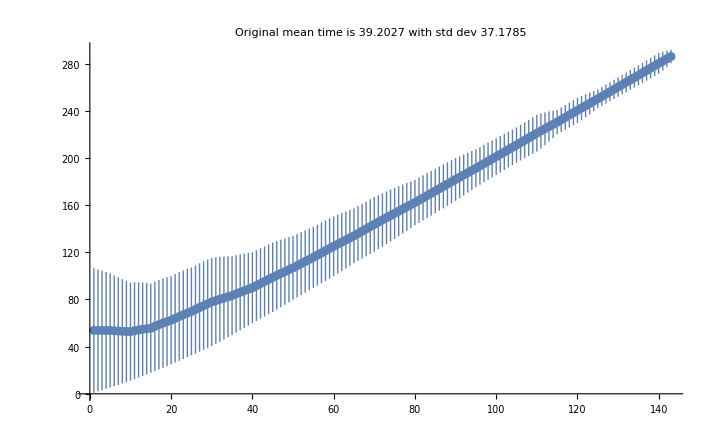

```mathematica
With[{mt=Mean[easy20times],xt=Max[easy20times],cdf=CDF[HistogramDistribution[easy20times],t],stdt=StandardDeviation[easy20times]},
ListPlot[Table[Around[t/cdf,t/cdf Sqrt[1-cdf]],{t,2,xt,2}],PlotRange->All,PlotLabel->"Original mean time is "<>ToString[mt] <>" with std dev "<>ToString[stdt]]
]
```

Does restart improve the variance, making the search-for-solution runtime more reliable? If we let s be the restart time as above, and if we simplify by assuming that the final cycle will take no less than time s, then the mean time is μ = s/p(s) and the variance is σ^2=s^2 (1-p)/p^2=μ^2 (1-p) so the standard deviation is σ=μ √(1-p(s)).  Since the final cycle probably takes less time, this might be an upper bound on the true variability?  Time and variance plotted below make the “simplifying” assumption, which clearly isn’t good for s > μ.

New question: how large a problem can BurningPotatoSATCRN solve within patience-limited time, typically?   At what value of n does it become infeasible?  This could take days and days... abort when bored.

```mathematica
With[{trials=10},
potatodata=Table[blank,{n,5,50}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TimeBurningPotatoCRN[problem],trials];
potatodata[[index]]={n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatodata[[index]]],
{n,5,50}]];
```

{x1→False,x2→False,x3→True,x4→False,x5→True} :=> True (0.184756 sec)

{x1→False,x2→True,x3→False,x4→True,x5→False} :=> True (0.116391 sec)

{x1→False,x2→False,x3→True,x4→False,x5→False} :=> True (0.231091 sec)

{x1→True,x2→False,x3→True,x4→True,x5→True} :=> True (0.118192 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True} :=> True (0.240798 sec)

{x1→True,x2→False,x3→True,x4→False,x5→False} :=> True (0.226358 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False} :=> True (0.285208 sec)

{x1→True,x2→False,x3→False,x4→False,x5→False} :=> True (0.291862 sec)

{x1→True,x2→True,x3→False,x4→False,x5→False} :=> True (0.070988 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True} :=> True (0.191641 sec)

1: {5,0.1960.023}

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→True} :=> True (0.445663 sec)

{x1→True,x2→False,x3→False,x4→False,x5→False,x6→True} :=> True (0.047804 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False} :=> True (0.096939 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False} :=> True (0.381136 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→False} :=> True (0.082923 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→False} :=> True (0.428239 sec)

{x1→False,x2→True,x3→False,x4→True,x5→True,x6→False} :=> True (0.260364 sec)

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→False} :=> True (0.234277 sec)

{x1→False,x2→False,x3→True,x4→False,x5→False,x6→False} :=> True (0.480306 sec)

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→False} :=> True (0.385449 sec)

2: {6,0.280.05}

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False,x7→True} :=> True (0.1234 sec)

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→True,x7→True} :=> True (3.64054 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True,x7→False} :=> True (1.36236 sec)

{x1→True,x2→False,x3→False,x4→True,x5→False,x6→False,x7→True} :=> True (1.10268 sec)

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False,x7→False} :=> True (1.32564 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→True,x7→True} :=> True (0.322657 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→False,x7→True} :=> True (0.351153 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False} :=> True (0.316034 sec)

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True (0.378997 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True,x7→True} :=> True (0.05898 sec)

3: {7,0.900.34}

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→True,x8→False} :=> True (0.482857 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→True,x7→True,x8→True} :=> True (0.550901 sec)

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True,x7→False,x8→False} :=> True (2.12947 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False,x7→False,x8→True} :=> True (0.40722 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→True,x7→True,x8→False} :=> True (5.10054 sec)

{x1→True,x2→False,x3→True,x4→False,x5→False,x6→True,x7→False,x8→False} :=> True (0.291233 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→False,x8→True} :=> True (0.227494 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False} :=> True (0.793236 sec)

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→True,x7→True,x8→False} :=> True (0.474294 sec)

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False,x8→False} :=> True (1.22697 sec)

4: {8,1.20.5}

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True,x8→True,x9→True} :=> True (0.469912 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False,x7→True,x8→True,x9→True} :=> True (0.751381 sec)

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True,x8→True,x9→True} :=> True (0.5841 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False,x7→False,x8→True,x9→True} :=> True (0.225565 sec)

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→True,x7→True,x8→False,x9→False} :=> True (1.45491 sec)

{x1→True,x2→False,x3→False,x4→True,x5→True,x6→False,x7→True,x8→False,x9→False} :=> True (0.533282 sec)

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→False,x7→True,x8→True,x9→True} :=> True (1.10289 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→True,x9→False} :=> True (0.595058 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→True,x7→False,x8→True,x9→True} :=> True (0.778085 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→True,x7→False,x8→True,x9→True} :=> True (0.315197 sec)

5: {9,0.680.12}

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (0.595323 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False} :=> True (2.08765 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True} :=> True (0.550272 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False} :=> True (0.860641 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True} :=> True (0.363518 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True} :=> True (0.407686 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False} :=> True (1.29073 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (3.48858 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True} :=> True (3.67484 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False} :=> True (0.605013 sec)

6: {10,1.40.4}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False} :=> True (1.50788 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False} :=> True (0.317545 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False} :=> True (8.17431 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False} :=> True (1.03788 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False} :=> True (0.411232 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False} :=> True (1.39453 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True} :=> True (1.36694 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True} :=> True (8.58909 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True} :=> True (0.3757 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True} :=> True (21.2946 sec)

7: {11,4.42.1}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True} :=> True (1.49422 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False} :=> True (5.88778 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True} :=> True (3.15841 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False} :=> True (2.29058 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False} :=> True (1.06147 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False} :=> True (107.897 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True} :=> True (7.51587 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True} :=> True (2.34621 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False} :=> True (4.89182 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True} :=> True (0.791101 sec)

8: {12,14.10.}

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False} :=> True (0.784374 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False} :=> True (5.43864 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True} :=> True (7.15024 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True} :=> True (4.0052 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False} :=> True (2.95217 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True} :=> True (3.08951 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True} :=> True (20.2292 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True} :=> True (3.14176 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True} :=> True (5.63651 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False} :=> True (0.656983 sec)

9: {13,5.31.8}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False} :=> True (1.31044 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True} :=> True (53.2459 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False} :=> True (2.41228 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True} :=> True (11.7877 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False} :=> True (27.5065 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True} :=> True (3.10242 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True} :=> True (2.34407 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False} :=> True (1.5762 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True} :=> True (2.11725 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True} :=> True (65.5581 sec)

10: {14,17.8.}

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False} :=> True (3.17214 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True} :=> True (1.89027 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False} :=> True (2.41636 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True} :=> True (34.3208 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False} :=> True (6.32704 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False} :=> True (4.70453 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True} :=> True (0.584876 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True} :=> True (4.3004 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False} :=> True (2.38199 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False} :=> True (8.78834 sec)

11: {15,6.93.1}

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True} :=> True (6.61801 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False} :=> True (2.90223 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False} :=> True (2.06649 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True} :=> True (36.2317 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False} :=> True (3.03827 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False} :=> True (0.928981 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True} :=> True (0.794731 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False} :=> True (87.7613 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True} :=> True (56.0322 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False} :=> True (6.07242 sec)

12: {16,20.10.}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False} :=> True (1.4976 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True} :=> True (32.6672 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False} :=> True (15.8795 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False} :=> True (1.03792 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False} :=> True (10.1784 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False} :=> True (5.26114 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True} :=> True (2.03589 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True} :=> True (3.69172 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False} :=> True (7.16633 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False} :=> True (38.9605 sec)

13: {17,12.4.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True} :=> True (55.5999 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False} :=> True (3.85826 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False} :=> True (51.4912 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False} :=> True (4.88004 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False} :=> True (61.097 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False} :=> True (60.4683 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False} :=> True (7.63791 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False} :=> True (107.965 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True} :=> True (45.9931 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True} :=> True (3.81495 sec)

14: {18,40.11.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True} :=> True (534.032 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True} :=> True (27.7544 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False} :=> True (1.65057 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True} :=> True (16.038 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True} :=> True (20.5964 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False} :=> True (19.4466 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False} :=> True (7.63491 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False} :=> True (17.8516 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False} :=> True (11.648 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True} :=> True (2.53286 sec)

15: {19,66.52.}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (3.99206 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (119.606 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (3.32066 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (137.437 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (19.5269 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (4.75742 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (292.148 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (38.0826 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (141.957 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (182.136 sec)

16: {20,94.31.}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False} :=> True (2.36355 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False} :=> True (24.493 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True} :=> True (61.587 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True} :=> True (1.4921 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True} :=> True (38.2854 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False} :=> True (3.73859 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False} :=> True (31.8817 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True} :=> True (4.051 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True} :=> True (8.05475 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True} :=> True (13.1797 sec)

17: {21,19.6.}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False} :=> True (1530.34 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False} :=> True (8.38248 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True} :=> True (22.2627 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True} :=> True (57.3459 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True} :=> True (98.581 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True} :=> True (16.8642 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False} :=> True (6.3386 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False} :=> True (1.61393 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True} :=> True (5808.9 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True} :=> True (48.8624 sec)

18: {22,760.580.}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True} :=> True (73.5901 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True} :=> True (35.3066 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False} :=> True (38.1068 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False} :=> True (16.0531 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False} :=> True (133.783 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True} :=> True (29.1004 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False} :=> True (21.206 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False} :=> True (3073.01 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True} :=> True (1.54567 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False} :=> True (1223.44 sec)

19: {23,465.313.}

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False} :=> True (3.14865 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False} :=> True (36.991 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False} :=> True (1247.3 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False} :=> True (125.738 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False} :=> True (110.204 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True} :=> True (8.93871 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False} :=> True (798.281 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False} :=> True (10.4021 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True} :=> True (7.26798 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False} :=> True (13.7338 sec)

20: {24,236.136.}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True} :=> True (17.2519 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True} :=> True (4.10571 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False} :=> True (6.8279 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True} :=> True (7.06525 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False} :=> True (53.9692 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True} :=> True (1187.7 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False} :=> True (104.316 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→True} :=> True (10.1188 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False} :=> True (108.308 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True} :=> True (999.759 sec)

21: {25,250.142.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True} :=> True (126.858 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False} :=> True (461.327 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False} :=> True (3.04583 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True} :=> True (67.7744 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False} :=> True (23.7211 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False} :=> True (1245.9 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False} :=> True (6.14785 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→False} :=> True (201.356 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False} :=> True (354.232 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True} :=> True (362.638 sec)

22: {26,285.119.}

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True} :=> True (254.891 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False} :=> True (160.706 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False} :=> True (194.313 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False} :=> True (4.3297 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True} :=> True (10.917 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False} :=> True (203.221 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True} :=> True (215.804 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True} :=> True (12.0822 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False} :=> True (450.36 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False} :=> True (1112.99 sec)

23: {27,262.104.}

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True} :=> True (9961.4 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True} :=> True (13.469 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→False} :=> True (2.26009 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False} :=> True (106.52 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True} :=> True (201.66 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False} :=> True (138.331 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False} :=> True (275.911 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True} :=> True (271.583 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True} :=> True (64.794 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True} :=> True (294.454 sec)

24: {28,1133.982.}

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True} :=> True (224.904 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False} :=> True (14.0832 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False} :=> True (9780.41 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False} :=> True (808.352 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True} :=> True (60.1623 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False} :=> True (36.5141 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True} :=> True (27.6 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False} :=> True (76.0102 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False} :=> True (15.787 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True} :=> True (344.235 sec)

25: {29,1139.963.}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→False,x30→True} :=> True (81.5886 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True} :=> True (136.209 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False} :=> True (11.3363 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True} :=> True (13.2442 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False} :=> True (53.8095 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True} :=> True (12.9037 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False} :=> True (4245.65 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True} :=> True (44.5173 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True} :=> True (8.6394 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False} :=> True (22.1705 sec)

26: {30,463.420.}

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True} :=> True (23.0517 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True} :=> True (896.866 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False} :=> True (228.158 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True} :=> True (3.7472 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→False} :=> True (2145.34 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False} :=> True (1056.44 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True} :=> True (409.249 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True} :=> True (1152.18 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False} :=> True (23.4896 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True} :=> True (57.4464 sec)

27: {31,600.223.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True} :=> True (301.224 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False} :=> True (15.5439 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True} :=> True (80.0609 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True} :=> True (21.2577 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→False} :=> True (11.3411 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→False} :=> True (74.5602 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True} :=> True (11464.5 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False} :=> True (4569.02 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True} :=> True (271.718 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True} :=> True (1440.5 sec)

28: {32,1.81.210^3}

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False} :=> True (92.0259 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True} :=> True (29.1896 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True} :=> True (185.833 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True} :=> True (9109.08 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True} :=> True (38282. sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True} :=> True (160.935 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False} :=> True (147.766 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False} :=> True (26.8028 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True} :=> True (22.0736 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True} :=> True (818.394 sec)

29: {33,5.4.10^3}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False} :=> True (36.3664 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True} :=> True (8447.88 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True} :=> True (15.2798 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False} :=> True (158.138 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False,x34→False} :=> True (24.214 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True} :=> True (1411.42 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False} :=> True (53.9296 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False} :=> True (9.60491 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False} :=> True (92.6305 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→True} :=> True (3656.9 sec)

30: {34,1391.866.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False} :=> True (202.997 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True,x35→True} :=> True (286.595 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True} :=> True (18911.1 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→True,x35→True} :=> True (5538.15 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True} :=> True (1897.09 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True} :=> True (23.2441 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True} :=> True (2.36898 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True,x35→False} :=> True (108561. sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False} :=> True (776.281 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True} :=> True (2936.8 sec)

31: {35,1.41.110^4}

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True} :=> True (8.48142 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True} :=> True (40.9837 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False} :=> True (6928.3 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False} :=> True (5747.77 sec)

$Aborted

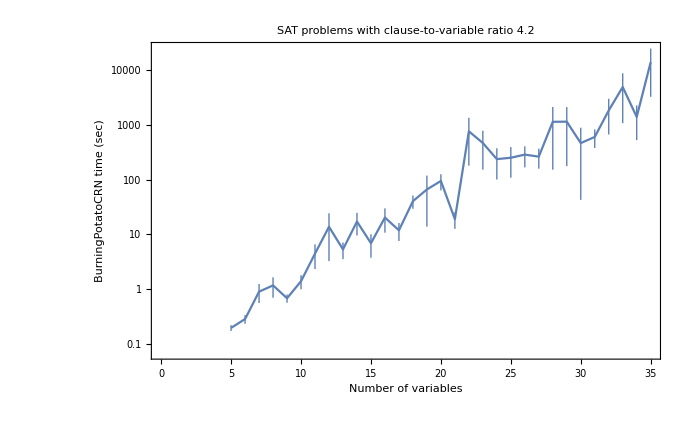

```mathematica
ListLogPlot[DeleteCases[potatodata,blank],Joined->True,Frame->True,FrameLabel->{"Number of variables","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2"]
```

We have the patience to solve up to size 35 random 3SAT problems.

The data is pretty noisy.  Choosing 10 random problems for each value of n does not sufficiently sample the problem space for that size if we want SEM error bars less than a 50% of the mean.  Is this because of the run-to-run variability for the same problem, or is it due to the variability of “intrinsic hardness” within the space of problems?  If it’s the latter, then both the well-mixed WalkSATCRN and MiniSAT itself would exhibit similar variability.    Let’s quickly take a look.  (First, recall the easy10problem, easy15problem, easy20problem tests of run-to-run variability in BurningPotatoCRN shown just a bit above here: the per-run standard deviation was about equal to the mean time.  So 10 trials would be expected to give SEM about 30% of the mean.  With extra variability from the random problem choice, we would of course expect larger SEM.)

```mathematica
MiniSATdata[range_,trials_]:=Module[{data},
data=Table[blank,{n,range}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]]; First[AbsoluteTiming[SatisfiableQ[problem]]],trials];
data[[index]]={n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
PrintTemporary[index,": ",data[[index]]],
{n,range}];
data];
```

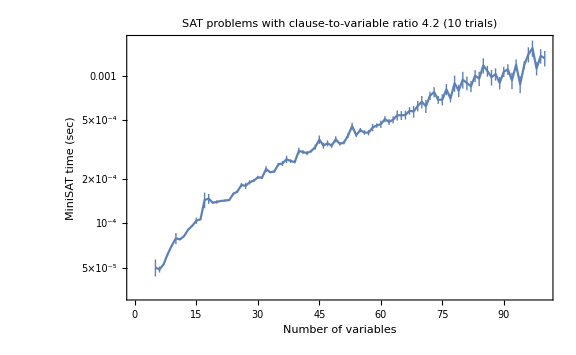
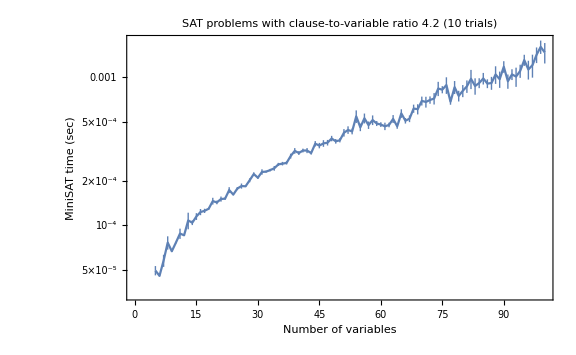
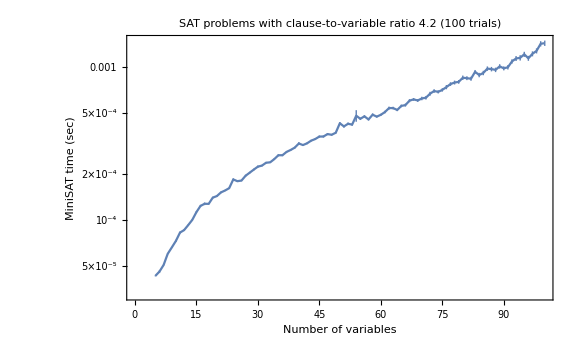
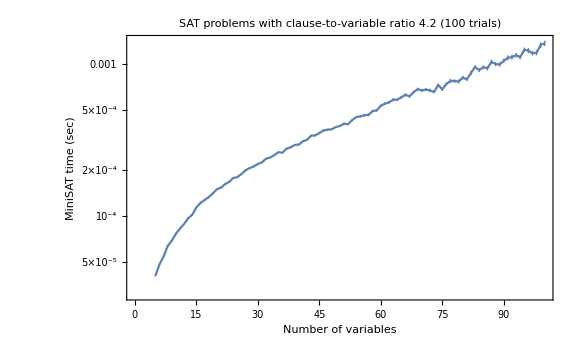
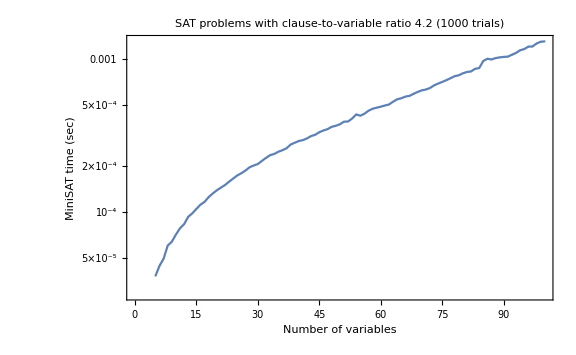
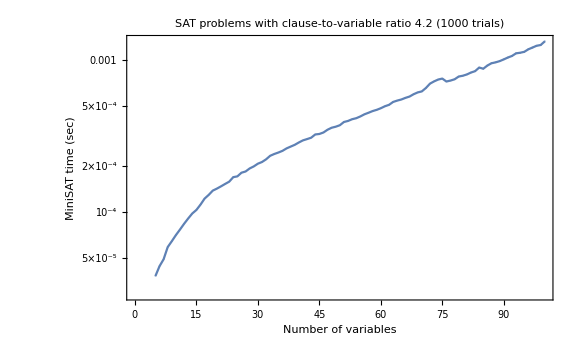
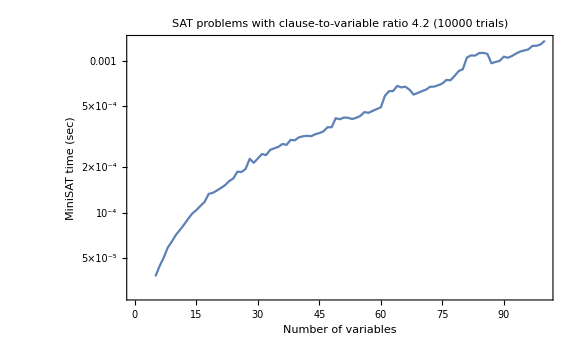
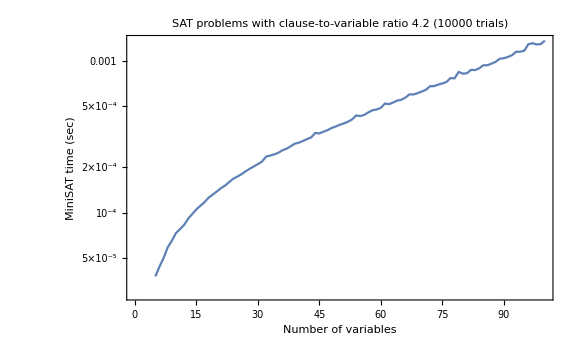

```mathematica
Table[With[{data=DeleteCases[MiniSATdata[Range[5,100],trials],blank]},
ListLogPlot[data,Joined->True,Frame->True,FrameLabel->{"Number of variables","MiniSAT time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 ("<>ToString[trials]<>" trials)",ImageSize->Large]],
{trials,{10,10,100,100,1000,1000,10000,10000}}]
```

We get a consistent, smooth increase in average problem difficulty as n gets larger.  With just 10 trials, the noise is reasonable large for large n but not so much for n<40, so it’s clear that the “MiniSAT-hardness” of problem instances of that size is not highly variable. (We already know from other experience that MiniSAT’s run-to-run variability is often quite small.)  There is also noise here that is not going away as quickly as expected with more samples -- the error bars here (which are based on a set of assumptions and thus show “expectations”) are plotted but really small, yet in some places the repeated plots show irreproducible noise.  This could either be long tails in the true time-to-solve of the algorithm (either some problems are ridiculously hard, or even some usually-easy problems occasionally really hang up the algorithm).   Or it could be evidence that AbsoluteTiming is being affected by background processes, such as me reading the internet, or perhaps whether or not my laptop is plugged in.

Another message is that for MiniSAT we’re seeing an on-average 30-fold slowdown per additional 100 variables, in terms of the asymptotic slope observed so far.  But the slowdown is greater while n<30.

Let’s tune rate constants to BurningPotatoCRN and see if it gets markedly better.  Maybe try on a problem that takes about 30 seconds, so there’s enough challenge for parameters to make a difference?  There is some worry that parameters tuned for one problem will be not so good for another problem, or that parameters tuned for one problem size will not be so good for another problem size.   Let’s avoid the first worry by running many random problems once rather than one problem many times -- this means our noise will be the sum of run-to-run and problem-to-problem variance, but we’ll live with it.  We won’t avoid the second worry, but we’ll test it out after we’ve tuned the parameters.

Which parameters would we vary?  With 65 reactions, we could in principle vary each one independently, and a priori that might matter.  Instead, though, we will guess that there is some kind of symmetry in play, and we can classify the reactions into a few types, each with their own rate:  “wire” reactions that propagate the signals along wires and through fan-out gates (without loss of generality, we fix these rates at 1); “OK” reactions that accept a signal on a wire that requests a flip, in the case that the given clause remains satisfied; “bounce” reactions that reject a flip request because it would have made the clause unsatisfied; and “flip” reactions that accept a flip request even though it breaks the clause, so another variable must flipped and a new signal sent out.

```mathematica
BurningPotatoCRN//MatrixForm[ArrayReshape[#,{8,9},None]]&
```

(aI+c →^1 a+cI  | cI+b →^1 c+bI  | bI+a →^1 b+aI  | aO+b →^1 a+bO  | bO+c →^1 b+cO  | cO+a →^1 c+aO  | aI+cO →^1 a+c  | cI+bO →^1 c+b  | bI+aO →^1 b+a 
aO+F →^1 a+Fb  | Fb+b →^1 F+bI  | Fb+bO →^1 F+b  | F+bO →^1 Fa+b  | a+Fa →^1 aI+F  | aO+Fa →^1 a+F  | aI+E →^1 a+Ebc  | bI+E →^1 b+Eca  | cI+E →^1 c+Eab 
Ebc+b →^1 Ec+bO  | Eca+c →^1 Ea+cO  | Eab+a →^1 Eb+aO  | Ebc+bI →^1 Ec+b  | Eca+cI →^1 Ea+c  | Eab+aI →^1 Eb+a  | Ec+c →^1 E+cO  | Ea+a →^1 E+aO  | Eb+b →^1 E+bO 
Ec+cI →^1 E+c  | Ea+aI →^1 E+a  | Eb+bI →^1 E+b  | aI+S001 →^0.99 a+S101  | bI+S001 →^0.99 b+S011  | cI+S001 →^1.01 cO+S001  | cI+S001 →^0.5 c+S100a  | cI+S001 →^0.5 c+S010b  | aI+S010 →^0.99 a+S110 
bI+S010 →^1.01 bO+S010  | cI+S010 →^0.99 c+S011  | bI+S010 →^0.5 b+S100a  | bI+S010 →^0.5 b+S001c  | aI+S100 →^1.01 aO+S100  | bI+S100 →^0.99 b+S110  | cI+S100 →^0.99 c+S101  | aI+S100 →^0.5 a+S010b  | aI+S100 →^0.5 a+S001c 
aI+S011 →^0.99 a+S111  | bI+S011 →^0.99 b+S001  | cI+S011 →^0.99 c+S010  | aI+S101 →^0.99 a+S001  | bI+S101 →^0.99 b+S111  | cI+S101 →^0.99 c+S100  | aI+S110 →^0.99 a+S010  | bI+S110 →^0.99 b+S100  | cI+S110 →^0.99 c+S111 
aI+S111 →^0.99 a+S011  | bI+S111 →^0.99 b+S101  | cI+S111 →^0.99 c+S110  | a+S100a →^1 aO+S100  | aI+S100a →^1 a+S100  | b+S010b →^1 bO+S010  | bI+S010b →^1 b+S010  | c+S001c →^1 cO+S001  | cI+S001c →^1 c+S001 
R0+aO →^1 R1+a  | R1+aO →^1 R0+a  | None | None | None | None | None | None | None)

```mathematica
BurningPotatoCRN/.{rxn[a_,b_,0.5]:>rxn[a,b,0.3]} //MatrixForm[ArrayReshape[#,{8,9},None]]&
```

(aI+c →^1 a+cI  | cI+b →^1 c+bI  | bI+a →^1 b+aI  | aO+b →^1 a+bO  | bO+c →^1 b+cO  | cO+a →^1 c+aO  | aI+cO →^1 a+c  | cI+bO →^1 c+b  | bI+aO →^1 b+a 
aO+F →^1 a+Fb  | Fb+b →^1 F+bI  | Fb+bO →^1 F+b  | F+bO →^1 Fa+b  | a+Fa →^1 aI+F  | aO+Fa →^1 a+F  | aI+E →^1 a+Ebc  | bI+E →^1 b+Eca  | cI+E →^1 c+Eab 
Ebc+b →^1 Ec+bO  | Eca+c →^1 Ea+cO  | Eab+a →^1 Eb+aO  | Ebc+bI →^1 Ec+b  | Eca+cI →^1 Ea+c  | Eab+aI →^1 Eb+a  | Ec+c →^1 E+cO  | Ea+a →^1 E+aO  | Eb+b →^1 E+bO 
Ec+cI →^1 E+c  | Ea+aI →^1 E+a  | Eb+bI →^1 E+b  | aI+S001 →^0.99 a+S101  | bI+S001 →^0.99 b+S011  | cI+S001 →^1.01 cO+S001  | cI+S001 →^0.3 c+S100a  | cI+S001 →^0.3 c+S010b  | aI+S010 →^0.99 a+S110 
bI+S010 →^1.01 bO+S010  | cI+S010 →^0.99 c+S011  | bI+S010 →^0.3 b+S100a  | bI+S010 →^0.3 b+S001c  | aI+S100 →^1.01 aO+S100  | bI+S100 →^0.99 b+S110  | cI+S100 →^0.99 c+S101  | aI+S100 →^0.3 a+S010b  | aI+S100 →^0.3 a+S001c 
aI+S011 →^0.99 a+S111  | bI+S011 →^0.99 b+S001  | cI+S011 →^0.99 c+S010  | aI+S101 →^0.99 a+S001  | bI+S101 →^0.99 b+S111  | cI+S101 →^0.99 c+S100  | aI+S110 →^0.99 a+S010  | bI+S110 →^0.99 b+S100  | cI+S110 →^0.99 c+S111 
aI+S111 →^0.99 a+S011  | bI+S111 →^0.99 b+S101  | cI+S111 →^0.99 c+S110  | a+S100a →^1 aO+S100  | aI+S100a →^1 a+S100  | b+S010b →^1 bO+S010  | bI+S010b →^1 b+S010  | c+S001c →^1 cO+S001  | cI+S001c →^1 c+S001 
R0+aO →^1 R1+a  | R1+aO →^1 R0+a  | None | None | None | None | None | None | None)

```mathematica
TuneBurningPotatoCRN[problem_,OK_,bounce_,flip_]:=Module[{dt=10000,time,data,haltedq,ddt,eventcount},
surface3D=LayoutPotato3SAT[problem];
surfaceCRN=BurningPotatoCRN/.{rxn[a_,b_,0.5]:>rxn[a,b,flip],rxn[a_,b_,0.99]:>rxn[a,b,OK],rxn[a_,b_,1.01]:>rxn[a,b,bounce]};
surfacecoloring=BurningPotatoColors;
fsurfaceCRN=PreprocessFasterSurfaceCRN[surfaceCRN,surface3D];
fsurface=Convert2FasterSpace[surface3D,fsurfaceCRN];
fsurfacecoloring=Convert2FasterColoring[ surfacecoloring,fsurfaceCRN]; 
fsurfacetime=0;
haltedq=0;
{time,data}=AbsoluteTiming[
While[haltedq==0,{{ddt,eventcount,haltedq},fsurface}=InfoRunFasterSurfaceCRN[fsurfaceCRN,fsurface,dt];fsurfacetime+=ddt];
];
surface3D=RevertFaster2Space[fsurface,fsurfaceCRN];
result=AssignmentFromPotato3SAT[problem,surface3D];
Print[result," :=> ",problem/.result, " (",time," sec)"];
time]
```

```mathematica
With[{trials=10,n=20,rates=Range[0.1,2.0,0.2]},
potatoflipdata=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,1.0,rate],trials];
potatoflipdata[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatoflipdata[[index]]],
{rate,rates}]];
```

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (9.72896 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (46.0898 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (2.28327 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (2.5726 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (2.87754 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (3.44785 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (12.4474 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (122.626 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (2.2448 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (31.2783 sec)

1: {{20,0.1},24.12.}

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (242.719 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (49.3105 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (4.90834 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (22.2807 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (4.33355 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (40.9469 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (1.01358 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (13.2322 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (9.38164 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (3.14011 sec)

2: {{20,0.3},39.23.}

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (31.0828 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (89.0803 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (1.75153 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (5.42277 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (19.3777 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (106.358 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (14.5906 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.25351 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (49.0628 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (119.862 sec)

3: {{20,0.5},44.14.}

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (9.20752 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (23.0501 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (5.96537 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.06473 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (93.1695 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (83.9343 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (57.7884 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.48773 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (1.83898 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (62.2707 sec)

4: {{20,0.7},35.11.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (20.1981 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (55.0065 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (31.2805 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (5.16893 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (21.2908 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (2.98652 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (13.0107 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (318.866 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (180.658 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (44.0017 sec)

5: {{20,0.9},69.32.}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (39.5688 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (32.5246 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (28.7978 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (69.8043 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (82.4593 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (24.795 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (65.6188 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (27.6407 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (156.057 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (83.1101 sec)

6: {{20,1.1},61.13.}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (1.03297 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (162.19 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (86.2904 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (63.6022 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (678.752 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (13.216 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (30.2752 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (2.74429 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (112.845 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (10.1242 sec)

7: {{20,1.3},116.65.}

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (136.555 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (444.731 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (15.1078 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (30.6004 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (7.35109 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (20.5603 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (63.6091 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (28.9599 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (48.0337 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (10.2078 sec)

8: {{20,1.5},81.42.}

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (243.077 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (22.0155 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (30.3676 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (2.42915 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (234.015 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (1694.91 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (8893.19 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (62.3417 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (1631.02 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (225.204 sec)

9: {{20,1.7},1304.868.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (38.041 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (1156.24 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (46.9247 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (11.8439 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (62.598 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (8.8736 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (445.327 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (136.791 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (907.454 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (234.257 sec)

10: {{20,1.9},305.130.}

```mathematica
With[{trials=10,n=20,rates=Range[2.0,0.1,-0.2]},
potatoOKdata=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,rate,1.0,0.5],trials];
potatoOKdata[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatoOKdata[[index]]],
{rate,rates}]];
```

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (17.2784 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (1012. sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (10.0103 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (27.4061 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (117.888 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.8685 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (486.526 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.28638 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (3.05676 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (31.0752 sec)

1: {{20,2.},171.105.}

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (37.5556 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (8.10014 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (34.5174 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (15.8073 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (30.17 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (115.247 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (37.4845 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (76.19 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (73.0637 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (11.3453 sec)

2: {{20,1.8},44.11.}

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (4.80384 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (101.891 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (12.9545 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (135.468 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (2.9795 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (3.70837 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (13.2912 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (2.05262 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (2.44472 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (18.0119 sec)

3: {{20,1.6},30.15.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (9.19388 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (3.49315 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (54.4044 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (8.29003 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (56.569 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (108.131 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (22.591 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (2.27646 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (232.662 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (101.295 sec)

4: {{20,1.4},60.23.}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (748.364 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (12.1617 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (1.42708 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (65.9235 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (5.51834 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (28.6541 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (8.47488 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (915.172 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (19.1552 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (62.5906 sec)

5: {{20,1.2},187.108.}

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (16.2137 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (58.0009 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (56.1075 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (16.9632 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (8.14316 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (118.933 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (377.722 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (266.207 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (6.11042 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (2.28837 sec)

6: {{20,1.},93.41.}

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (6.01455 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (9.01974 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (15.1494 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (724.07 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (58.0413 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (265.134 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (34.2709 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (2.06357 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (20.4577 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (95.2643 sec)

7: {{20,0.8},123.71.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (6.52693 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (1.84575 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (6.64339 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (17.4294 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (5.17892 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (43.8583 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (15.1996 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (55.7125 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (4.01244 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (6.00585 sec)

8: {{20,0.6},16.6.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (21.9663 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (23.2752 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (7.10952 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (5.77375 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (188.934 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (25.2188 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (6.31142 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (4.03878 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (97.1933 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (9.16336 sec)

9: {{20,0.4},39.19.}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (5.61302 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (14.3766 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (71.1289 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (60.6634 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (85.1412 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (63.6748 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (9.02872 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (6.01227 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (3.90915 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (12.4951 sec)

10: {{20,0.2},33.10.}

```mathematica
With[{trials=10,n=20,rates=Range[2.0,0.1,-0.2]},
potatobouncedata=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,rate,0.5],trials];
potatobouncedata[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatobouncedata[[index]]],
{rate,rates}]];
```

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (5.18712 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (19.1173 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.60924 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (3.47461 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (3.1796 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (3.26306 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (10.1768 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (38.4934 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (17.3004 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (11.5937 sec)

1: {{20,2.},11.4.}

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (13.4539 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (1.2762 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (3.14464 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (26.7991 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (16.9257 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (221.923 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (17.6345 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (8.26194 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.2429 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (0.792263 sec)

2: {{20,1.8},31.21.}

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (93.3826 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (14.7925 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (2.21109 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (27.6396 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (22.2698 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (36.1315 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (35.9795 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (38.7006 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (5.83859 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (22.5439 sec)

3: {{20,1.6},30.8.}

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.88384 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (89.6985 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (43.0007 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (10.0061 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (214.833 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (11.6648 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (0.947914 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (7.66219 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (20.2709 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (367.857 sec)

4: {{20,1.4},77.38.}

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (10.2559 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (5.24886 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (105.616 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (0.783424 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (40.4094 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (7.06563 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (24.3862 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (8.83088 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (162.857 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (1.59972 sec)

5: {{20,1.2},37.17.}

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (96.2069 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (11.3618 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (9.49868 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (7.92238 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (12.8163 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (5.72086 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (228.401 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (31.0076 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (10.7929 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (42.6306 sec)

6: {{20,1.},46.22.}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (6.38923 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (102.205 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (14.9546 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (19.6178 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (86.4157 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (3.205 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (20.3106 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (193.543 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (42.2143 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (9.08206 sec)

7: {{20,0.8},50.19.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (19.9725 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (1.73459 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (146.185 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (61.4843 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (49.118 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (92.8903 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (30.2042 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (3.08051 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.4481 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (1970.14 sec)

8: {{20,0.6},239.193.}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (171.004 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (2.9469 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (366.585 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (247.28 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (51.4621 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (190.902 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (39.3294 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (0.7865 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (66.4038 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (1754.06 sec)

9: {{20,0.4},289.167.}

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (26.8843 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (165.477 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (0.922533 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (2509.18 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (16.905 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (153.105 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (223.175 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (899.287 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (979.754 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (800.45 sec)

10: {{20,0.2},578.247.}

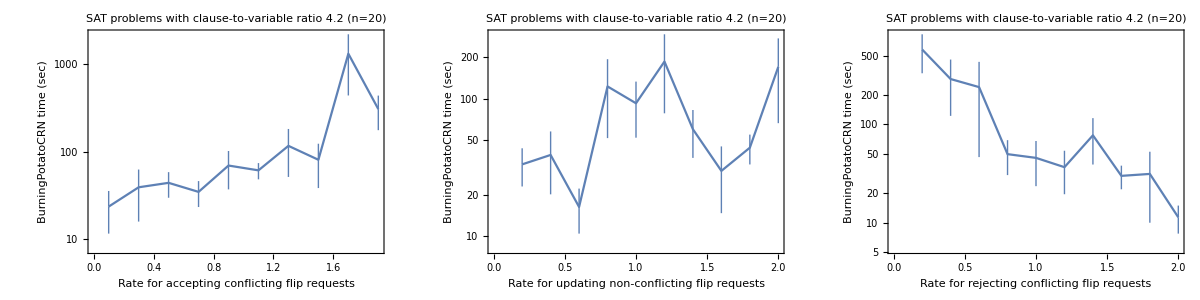

```mathematica
With[{n=20,reformat={{{n_,r_?NumberQ},t_}:>{r,t},blank->Sequence[]}},{
ListLogPlot[potatoflipdata/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for accepting conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>")"],
ListLogPlot[potatoOKdata/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for updating non-conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>")"],
ListLogPlot[potatobouncedata/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for rejecting conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>")"]
}]//TableForm[{#}]&
```

This preliminary data is already surprising.  There are clear trends for both the “flip” rate (for accepting flip requests that require also flipping another variable in order to keep the clause satisfied; slower is better) and for the “bounce” rate (for rejecting attempts to flip a variable that would break a clause; faster is better) and neither of these trends bottoms out for the range of parameters examined. I did not expect the “OK” rate (for updating non-conflicting flip requests, i.e. those that don’t break a clause) to matter much at all, but the data suggests a trend in favor of slower rates.  (For the “OK” rate, however, the error bars are large enough and the trend is weak enough that the data is also reasonably consistent with, in fact, there being no significant effect.)  Overall, it looks like at least a 5-fold speed-up could be achievable, at least on problems of this size.   (Or, we could tune to obtain a 10-fold slow-down, if we were perverse...)

We have two things to test now: Can we further improve the performance with even smaller “flip” rates and even larger “bounce” rates?  Does the “OK” rate truly not matter, at least with the given range?  And is the improved tuning stable for larger problem sizes?

```mathematica
With[{trials=20,n=20,rates=Range[0.01,0.1,0.01]},
potatoflipdata2=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,1.0,rate],trials];
potatoflipdata2[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatoflipdata2[[index]]],
{rate,rates}]];
```

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (96.3326 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (85.7714 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (193.791 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (4.42412 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (165.03 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (17.6152 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (7.2316 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (21.5621 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (61.089 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (1163.82 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (218.182 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (15.4064 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (220.425 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (86.523 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (59.2331 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (428.545 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (6.92729 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (3.36538 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (8.09391 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (322.497 sec)

1: {{20,0.01},159.59.}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (58.9623 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (18.959 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (45.5988 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (8.14556 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (33.1041 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (27.2316 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (91.2219 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (37.0283 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (15.3081 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (190.324 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (22.2894 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (81.0907 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (23.1981 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (6.26664 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (80.8 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (41.1885 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (51.5184 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (20.1896 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (3.58688 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (52.3652 sec)

2: {{20,0.02},45.10.}

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (33.2702 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (31.4205 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (1.14026 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (246.946 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (102.733 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (7.42846 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (1.12566 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (16.342 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (140.665 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.32839 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (3.64549 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (61.9256 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (24.2577 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (31.3081 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (5.19227 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (33.7463 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (151.827 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (45.3448 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (8.01614 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (186.706 sec)

3: {{20,0.03},57.16.}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (25.0169 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (84.7284 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (67.8994 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (8.4954 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (11.2251 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (75.8399 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.43242 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (17.5937 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (7.46639 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (16.5691 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (91.8367 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (3.81137 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (30.675 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (0.968332 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (6.13139 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (24.4817 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (13.4433 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (1.77372 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (27.8821 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (3.96613 sec)

4: {{20,0.04},26.7.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (3.0058 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (82.0848 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (15.8094 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (6.00605 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (105.612 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (5.72552 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (4.73673 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (60.5386 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (11.8445 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (26.4722 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (25.6029 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (230.322 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (8.24634 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (3.80529 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (4.77331 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (115.301 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (0.700087 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.4238 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (127.087 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (16.532 sec)

5: {{20,0.05},43.13.}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (4.45937 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (46.013 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (3.93516 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (7.50391 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (5.85951 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.69383 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (45.5865 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (15.4029 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (9.79762 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (20.3901 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (6.8735 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (102.884 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (17.6225 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (13.2209 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.04379 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (86.9281 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (307.567 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (1.47148 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (46.4208 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (3.26622 sec)

6: {{20,0.06},38.16.}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (64.0733 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (117.906 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (16.016 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (2.9168 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (17.2393 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (1.21919 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (19.0259 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (2.83527 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (3.39262 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (9.13341 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (4.07967 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (9.7014 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (24.5228 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (28.8672 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (181.492 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (10.2108 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (14.0435 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (8.64197 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (2.49348 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (10.4423 sec)

7: {{20,0.07},27.10.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (6.29535 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (101.067 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (7.09684 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (20.1879 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (13.1603 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (18.724 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (5.32833 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (37.3344 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (1.78047 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (10.7581 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (20.7895 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (2.17566 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (93.8949 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (7.63272 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (21.4814 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (13.2985 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (2.22741 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (9.42767 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (10.3182 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (24.6763 sec)

8: {{20,0.08},21.6.}

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (60.3732 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (1.9761 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (14.029 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (2.3741 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (35.794 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (2.6822 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (20.8055 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (11.7151 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (15.8108 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (24.0878 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (27.1892 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (79.2754 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (26.8356 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (35.1487 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (90.8401 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (3.81864 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (19.8977 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (11.5022 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (6.08341 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (17.3762 sec)

9: {{20,0.09},25.6.}

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (48.7992 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (1.51311 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (4.27539 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (93.0764 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (16.7913 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (17.4283 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (11.4826 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (36.7495 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (1.48963 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (3.24385 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (7.28083 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (1.72021 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (45.1108 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (5.53671 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (11.8438 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (57.9064 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (7.33588 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.08067 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (2.60103 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (2.61098 sec)

10: {{20,0.1},19.5.}

```mathematica
With[{trials=20,n=20,rates=Range[0.2,2.0,0.2]},
potatoOKdata2=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,rate,1.0,0.1],trials];
potatoOKdata2[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatoOKdata2[[index]]],
{rate,rates}]];
```

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (8.06932 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (2.95785 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (24.6468 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (4.71581 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (2.01995 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (92.2734 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (27.6912 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (7.83169 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (8.9984 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (61.7211 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (62.16 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (2.75761 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (14.6388 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (5.51287 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (1.33167 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (6.40762 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (2.8073 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (4.19981 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (72.3817 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (34.7833 sec)

1: {{20,0.2},22.6.}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (10.7726 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (46.3858 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (15.9903 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (32.3349 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (10.334 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (5.64721 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (1.02629 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (14.004 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (16.6125 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (12.4238 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (2.15145 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (2.52714 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (9.54857 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (43.3679 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (5.41095 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (22.2457 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (2.36115 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (56.1121 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (4.66938 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (4.34447 sec)

2: {{20,0.4},16.4.}

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (75.9086 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (6.43377 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (28.9165 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (28.027 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (6.18767 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (22.5381 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (7.45382 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (5.33127 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (14.1366 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (12.1662 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (19.5291 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (0.858876 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (8.57636 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (31.252 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (1.98181 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (87.885 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (12.037 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (9.81542 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (4.97056 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (3.94755 sec)

3: {{20,0.6},19.5.}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (7.66358 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (29.6555 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (4.44768 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.12107 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (10.4391 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (22.6232 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (9.76367 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (24.1461 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (7.05262 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (30.1958 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (27.5925 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (4.49101 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (57.5543 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (7.81205 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (3.0791 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (22.9795 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (38.0142 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (16.424 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (5.89564 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (64.4188 sec)

4: {{20,0.8},20.4.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (27.507 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (19.1048 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (3.81591 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (16.6224 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (3.34913 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (1.12899 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (6.44321 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (8.19577 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (1.28852 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (9.34634 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (3.83116 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (4.56802 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (2.58999 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (9.14362 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (60.9951 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (43.0726 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (2.63024 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (2.89284 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (1.2683 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (1.4223 sec)

5: {{20,1.},11.53.5}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (6.01756 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (4.24187 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (9.47078 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (23.7451 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (6.22869 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (25.5789 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (3.10544 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (96.5783 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (51.1637 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (5.07633 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (3.89696 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (19.9174 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (3.024 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (4.24229 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (53.0099 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (24.3336 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (2.25459 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (1.89426 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (9.61108 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (30.6021 sec)

6: {{20,1.2},19.5.}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (29.2261 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (6.2147 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (1.31464 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (14.8272 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (24.3509 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (10.8442 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (8.95678 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (45.2042 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (100.84 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (4.29239 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (3.44403 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (46.8459 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (32.786 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (5.98623 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (7.93798 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (2.10647 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (125.893 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (11.4039 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (4.31557 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (7.95041 sec)

7: {{20,1.4},25.7.}

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (74.3381 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (32.3514 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (20.5138 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (26.9808 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (8.12518 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (12.2934 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (4.96884 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (51.7033 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (1.29937 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (6.57596 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (12.0238 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (5.34102 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (1.34102 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (4.93994 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (10.3328 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (6.18626 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (7.51499 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (7.56678 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (1.6832 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (117.42 sec)

8: {{20,1.6},21.7.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.02463 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (15.9861 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (4.7615 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (21.6798 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (6.96647 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (1.63209 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (37.251 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (8.11005 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (9.73216 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (2.97593 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (51.0672 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (23.8813 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (6.55154 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (10.22 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (10.1284 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (6.15402 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (44.8519 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (19.2618 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (6.94072 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (31.9803 sec)

9: {{20,1.8},16.13.3}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (1.08283 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (36.7643 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (1.77875 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (19.6052 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (17.1767 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (15.8751 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.28846 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (14.3823 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (2.46143 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (2.7701 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (74.8842 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (25.9105 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (0.872024 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (2.5215 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (10.7444 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (11.1511 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (21.3538 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (1.30088 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (25.0065 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.93541 sec)

10: {{20,2.},15.4.}

```mathematica
With[{trials=20,n=20,rates=Range[1.0,10.0,1.0]},
potatobouncedata2=Table[blank,{rate,rates}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,rate,0.1],trials];
potatobouncedata2[[index]]={{n,rate},Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatobouncedata2[[index]]],
{rate,rates}]];
```

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (19.7834 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (6.49353 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (9.40068 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (39.6329 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (4.27012 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (31.3245 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (226.896 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (26.5744 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (10.4783 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (15.4442 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (3.43572 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (10.0934 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (3.34337 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (12.6297 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (15.1413 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (11.0528 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (2.83202 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (3.88546 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (58.287 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (1.74592 sec)

1: {{20,1.},26.11.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (15.7147 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (8.31729 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (51.1323 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (88.505 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (190.306 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (9.11098 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (6.67063 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (7.71144 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (3.22121 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (17.8822 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (27.6473 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (10.036 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (31.6155 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (8.95728 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (7.65912 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (16.2995 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (12.9602 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (25.627 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (74.9383 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (9.11581 sec)

2: {{20,2.},31.10.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (1.99664 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (56.3004 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (50.1115 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (66.4575 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (2.34625 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (37.498 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (1.73601 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (3.91613 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (45.038 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (12.9208 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (8.17831 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (9.51579 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (16.1471 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (34.1087 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (18.7179 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (3.24545 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (1.91776 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (289.302 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (14.4802 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (4.86811 sec)

3: {{20,3.},34.14.}

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (14.0979 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (1.49521 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (140.02 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (42.0881 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (6.53148 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (12.6223 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (21.5693 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (17.4154 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (7.13003 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (4.96044 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (77.4489 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (39.2783 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (105.153 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (544.628 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (661.04 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (20.872 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (139.894 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (96.8935 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (17.4773 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (76.0339 sec)

4: {{20,4.},102.40.}

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (7.91714 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (114.092 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (5.0476 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (35.729 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (119.216 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (1.38709 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (71.4996 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (18.21 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (14.9473 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (26.7591 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (2.28405 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (80.1038 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (182.972 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (13.0779 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (89.614 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (27.4816 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (2.09333 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (35.6586 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (5.29874 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False} :=> True (33.3337 sec)

5: {{20,5.},44.11.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (43.0576 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (1.77178 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (6.8624 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (14.3048 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (92.3642 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True} :=> True (6.70635 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (2.7533 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (9.136 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (3.57109 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (46.7795 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (132.039 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (206.587 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (28.5416 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (229.43 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (174.018 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (12.9802 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (259.94 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (263.441 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (2967.06 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (1.744 sec)

6: {{20,6.},225.146.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (1068.41 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (7.6598 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (72.8867 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (33.1352 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True} :=> True (9.73014 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (2.83535 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (613.378 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (71.0822 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (47.5319 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (3.49869 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True} :=> True (48.4625 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (26.2415 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (49.1372 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False} :=> True (16.4278 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.05326 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (10.3476 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (1.12142 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (158.619 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (8.49795 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (83.6633 sec)

7: {{20,7.},117.58.}

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (78.531 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (99.2017 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (66.1135 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (561.29 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (4.57355 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (86.3622 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (85.6304 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (457.983 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (23.5255 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (93.151 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (36.5077 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (240.772 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (5.68712 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (89.8097 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (39.5444 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (91.1545 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (40.0055 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (457.334 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (5.3379 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (69.6285 sec)

8: {{20,8.},132.37.}

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (55.1646 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (519.583 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (17.1974 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True} :=> True (191.506 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (733.909 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (5.2576 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (157.035 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (20.5443 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (254.4 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (5.08591 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (253.958 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (1375.4 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (4.25856 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (51.717 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (26.8326 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (367.017 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (64.6055 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (210.193 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (56.7688 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (341.193 sec)

9: {{20,9.},236.74.}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (107.393 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (10.1091 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True} :=> True (86.5626 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (383.291 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (409.573 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False} :=> True (2314.02 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True} :=> True (290.558 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (8.81729 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (3.96383 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False} :=> True (687.257 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (65.2795 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True} :=> True (471.796 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False} :=> True (16.8459 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (15.2902 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True} :=> True (7.18572 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False} :=> True (77.1672 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True} :=> True (26.8935 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True} :=> True (5.33596 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (47.5108 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (2.39734 sec)

10: {{20,10.},252.117.}

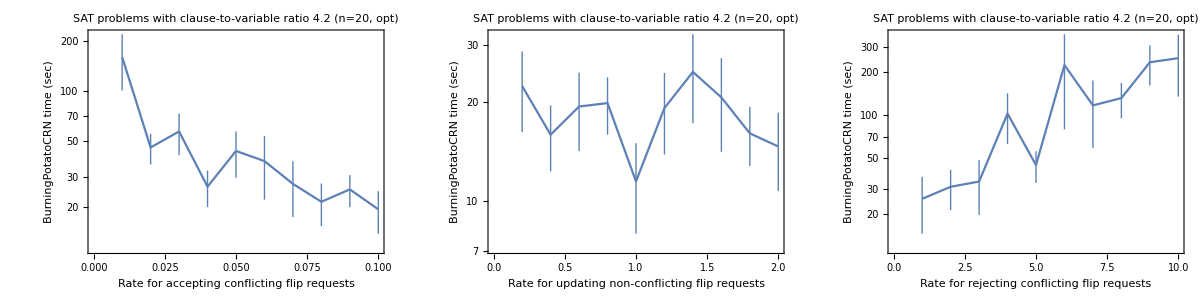

```mathematica
With[{n=20,reformat={{{n_,r_?NumberQ},t_}:>{r,t},blank->Sequence[]}},{
ListLogPlot[potatoflipdata2/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for accepting conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>", opt)"],
ListLogPlot[potatoOKdata2/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for updating non-conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>", opt)"],
ListLogPlot[potatobouncedata2/.reformat,ImageSize->Medium,Joined->True,Frame->True,FrameLabel->{"Rate for rejecting conflicting flip requests","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2 (n="<>ToString[n]<>", opt)"]
}]//TableForm[{#}]&
```

Now let’s try to look at how large a problem can be solved, and see whether the new tuning helps beyond size 20.  We take a bit of a risk, assuming that the one-parameter-at-a-time tunings are synergistic, which they needn’t be.  Although this graph is fairly convincing that our estimate of optimal parameters from the previous run can’t be improved much!  Also, combined with the previous plot, the improvement may be less than we hoped for: from (1,1,0.5) to (1,1,0.1) might be taking us from about 51 sec to 17 sec for size-20 problems, just a factor of 3.

```mathematica
With[{trials=20},
potatodata2=Table[blank,{n,5,50}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,1.0,0.1 ],trials];
potatodata2[[index]]={n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatodata2[[index]]],
{n,5,50}]];
```

{x1→True,x2→True,x3→True,x4→True,x5→True} :=> True (0.075402 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True} :=> True (0.140771 sec)

{x1→False,x2→False,x3→True,x4→True,x5→True} :=> True (0.06487 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True} :=> True (0.348659 sec)

{x1→True,x2→True,x3→False,x4→True,x5→False} :=> True (1.20563 sec)

{x1→False,x2→True,x3→False,x4→False,x5→True} :=> True (0.302418 sec)

{x1→True,x2→False,x3→False,x4→False,x5→False} :=> True (0.193668 sec)

{x1→True,x2→False,x3→False,x4→True,x5→True} :=> True (0.255158 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False} :=> True (0.103306 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False} :=> True (0.321392 sec)

{x1→True,x2→False,x3→True,x4→True,x5→True} :=> True (0.120077 sec)

{x1→False,x2→True,x3→False,x4→True,x5→True} :=> True (0.326867 sec)

{x1→False,x2→True,x3→False,x4→True,x5→True} :=> True (1.88877 sec)

{x1→False,x2→True,x3→True,x4→False,x5→False} :=> True (0.260772 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False} :=> True (0.357925 sec)

{x1→False,x2→True,x3→False,x4→False,x5→True} :=> True (0.175824 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True} :=> True (3.15169 sec)

{x1→True,x2→False,x3→True,x4→False,x5→False} :=> True (0.14145 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False} :=> True (0.037458 sec)

{x1→True,x2→False,x3→True,x4→False,x5→False} :=> True (0.184162 sec)

1: {5,0.480.17}

{x1→False,x2→False,x3→True,x4→False,x5→True,x6→False} :=> True (0.235525 sec)

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True} :=> True (0.469591 sec)

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→False} :=> True (1.7682 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→False} :=> True (0.417455 sec)

{x1→True,x2→False,x3→False,x4→True,x5→False,x6→False} :=> True (0.160205 sec)

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→True} :=> True (0.258303 sec)

{x1→False,x2→True,x3→True,x4→True,x5→False,x6→False} :=> True (0.238832 sec)

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→False} :=> True (0.128905 sec)

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→False} :=> True (0.473218 sec)

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True} :=> True (0.286578 sec)

{x1→True,x2→False,x3→True,x4→False,x5→True,x6→False} :=> True (0.074171 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True} :=> True (1.65572 sec)

{x1→False,x2→False,x3→False,x4→True,x5→False,x6→True} :=> True (0.315424 sec)

{x1→True,x2→False,x3→False,x4→True,x5→False,x6→True} :=> True (1.32582 sec)

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False} :=> True (0.314388 sec)

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→True} :=> True (0.99514 sec)

{x1→True,x2→True,x3→True,x4→False,x5→True,x6→True} :=> True (0.113976 sec)

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True} :=> True (0.123644 sec)

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False} :=> True (0.265823 sec)

{x1→True,x2→False,x3→True,x4→True,x5→True,x6→False} :=> True (1.25861 sec)

2: {6,0.540.12}

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→False,x7→True} :=> True (1.29597 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→False,x7→True} :=> True (1.4222 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False} :=> True (0.353586 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→False} :=> True (0.460065 sec)

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True} :=> True (0.361215 sec)

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→True,x7→False} :=> True (4.93561 sec)

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→True,x7→True} :=> True (0.669211 sec)

{x1→False,x2→True,x3→False,x4→True,x5→False,x6→True,x7→False} :=> True (0.239215 sec)

{x1→False,x2→False,x3→True,x4→False,x5→False,x6→True,x7→False} :=> True (0.337555 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→False,x7→True} :=> True (3.15151 sec)

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→True} :=> True (0.317793 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→False,x7→True} :=> True (0.640453 sec)

{x1→False,x2→True,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True (0.176468 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→True,x7→True} :=> True (0.369581 sec)

{x1→True,x2→True,x3→True,x4→False,x5→True,x6→True,x7→True} :=> True (0.134793 sec)

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→False,x7→False} :=> True (0.663679 sec)

{x1→True,x2→True,x3→False,x4→False,x5→False,x6→True,x7→True} :=> True (0.722462 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True,x7→True} :=> True (0.207914 sec)

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→True,x7→True} :=> True (0.552554 sec)

{x1→True,x2→True,x3→False,x4→True,x5→False,x6→False,x7→False} :=> True (1.80847 sec)

3: {7,0.940.26}

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True,x8→True} :=> True (0.819888 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→False,x7→True,x8→False} :=> True (0.1599 sec)

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→True,x8→False} :=> True (0.417364 sec)

{x1→True,x2→True,x3→True,x4→True,x5→False,x6→True,x7→True,x8→False} :=> True (1.01793 sec)

{x1→False,x2→False,x3→True,x4→False,x5→False,x6→True,x7→True,x8→False} :=> True (2.57602 sec)

{x1→False,x2→True,x3→True,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True (3.03256 sec)

{x1→False,x2→True,x3→True,x4→False,x5→True,x6→False,x7→True,x8→True} :=> True (3.57221 sec)

{x1→True,x2→False,x3→False,x4→True,x5→True,x6→True,x7→True,x8→True} :=> True (0.23198 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→True,x7→True,x8→False} :=> True (0.669748 sec)

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→True,x7→False,x8→True} :=> True (0.726886 sec)

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→True,x7→False,x8→False} :=> True (0.221893 sec)

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True,x7→True,x8→False} :=> True (0.391309 sec)

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→False,x7→False,x8→False} :=> True (3.27973 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→True,x7→True,x8→True} :=> True (2.27359 sec)

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True,x7→False,x8→False} :=> True (3.23821 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→False,x7→True,x8→False} :=> True (1.63878 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→False,x7→True,x8→True} :=> True (0.820968 sec)

{x1→True,x2→False,x3→False,x4→False,x5→True,x6→False,x7→False,x8→True} :=> True (1.15716 sec)

{x1→False,x2→False,x3→True,x4→True,x5→True,x6→True,x7→False,x8→True} :=> True (0.298016 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→True,x8→False} :=> True (0.886887 sec)

4: {8,1.370.26}

{x1→False,x2→True,x3→True,x4→True,x5→True,x6→True,x7→True,x8→False,x9→False} :=> True (0.422084 sec)

{x1→True,x2→True,x3→False,x4→False,x5→True,x6→True,x7→False,x8→True,x9→False} :=> True (2.06735 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→False,x7→False,x8→True,x9→True} :=> True (0.838241 sec)

{x1→True,x2→True,x3→True,x4→False,x5→False,x6→False,x7→True,x8→False,x9→False} :=> True (0.249348 sec)

{x1→False,x2→True,x3→True,x4→False,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True (0.371783 sec)

{x1→False,x2→True,x3→False,x4→True,x5→True,x6→True,x7→True,x8→False,x9→False} :=> True (0.973828 sec)

{x1→False,x2→False,x3→False,x4→False,x5→True,x6→True,x7→False,x8→False,x9→True} :=> True (1.4522 sec)

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→False,x7→False,x8→False,x9→False} :=> True (0.831662 sec)

{x1→True,x2→False,x3→False,x4→True,x5→False,x6→False,x7→False,x8→True,x9→False} :=> True (1.95121 sec)

{x1→False,x2→True,x3→False,x4→False,x5→True,x6→True,x7→False,x8→True,x9→True} :=> True (2.56261 sec)

{x1→True,x2→True,x3→True,x4→True,x5→True,x6→False,x7→False,x8→False,x9→False} :=> True (0.288887 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True,x8→True,x9→True} :=> True (0.205415 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True,x7→True,x8→True,x9→False} :=> True (0.554885 sec)

{x1→True,x2→True,x3→False,x4→True,x5→True,x6→False,x7→True,x8→True,x9→False} :=> True (6.84373 sec)

{x1→False,x2→False,x3→False,x4→True,x5→True,x6→True,x7→True,x8→False,x9→True} :=> True (0.208166 sec)

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→True,x7→False,x8→False,x9→True} :=> True (1.76016 sec)

{x1→False,x2→False,x3→False,x4→False,x5→False,x6→True,x7→True,x8→False,x9→False} :=> True (1.35597 sec)

{x1→True,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True,x8→False,x9→True} :=> True (2.59622 sec)

{x1→False,x2→False,x3→True,x4→True,x5→False,x6→False,x7→True,x8→False,x9→True} :=> True (1.93899 sec)

{x1→False,x2→True,x3→True,x4→False,x5→True,x6→False,x7→True,x8→False,x9→False} :=> True (0.209594 sec)

5: {9,1.380.34}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True} :=> True (0.870914 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False} :=> True (3.02094 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False} :=> True (0.436032 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True} :=> True (0.838361 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False} :=> True (0.507551 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True} :=> True (3.85893 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False} :=> True (0.618455 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True} :=> True (0.673263 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False} :=> True (0.383906 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True} :=> True (0.232885 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False} :=> True (1.2403 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False} :=> True (1.03012 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True} :=> True (3.35708 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False} :=> True (0.832707 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False} :=> True (0.457536 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True} :=> True (2.14465 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True} :=> True (3.45058 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True} :=> True (0.565623 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False} :=> True (1.77761 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False} :=> True (0.439774 sec)

6: {10,1.340.26}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False} :=> True (2.99915 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True} :=> True (1.99187 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False} :=> True (0.402108 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False} :=> True (31.6039 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True} :=> True (1.60641 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False} :=> True (18.9621 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True} :=> True (5.46687 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False} :=> True (8.86721 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True} :=> True (2.71368 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False} :=> True (1.05349 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True} :=> True (3.9585 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True} :=> True (10.2292 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True} :=> True (0.754257 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True} :=> True (4.53955 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False} :=> True (0.615878 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False} :=> True (0.420638 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True} :=> True (0.443138 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True} :=> True (20.8064 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True} :=> True (1.3891 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True} :=> True (8.36805 sec)

7: {11,6.41.9}

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True} :=> True (4.01056 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False} :=> True (1.02815 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False} :=> True (1.637 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False} :=> True (0.75147 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False} :=> True (5.24241 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True} :=> True (2.59361 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True} :=> True (0.63729 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True} :=> True (0.348767 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True} :=> True (11.401 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True} :=> True (0.384754 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True} :=> True (3.48983 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False} :=> True (0.397172 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True} :=> True (1.13506 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False} :=> True (2.67503 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True} :=> True (1.85982 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False} :=> True (1.10553 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False} :=> True (8.1457 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False} :=> True (1.96121 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False} :=> True (1.03048 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True} :=> True (0.488707 sec)

8: {12,2.50.6}

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False} :=> True (1.11851 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False} :=> True (0.938824 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False} :=> True (1.79023 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True} :=> True (3.0775 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False} :=> True (4.60217 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False} :=> True (4.96384 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True} :=> True (0.339557 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True} :=> True (18.2176 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True} :=> True (1.25639 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True} :=> True (1.11825 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True} :=> True (0.791618 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True} :=> True (23.0368 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True} :=> True (8.2354 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False} :=> True (1.44129 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False} :=> True (1.28544 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True} :=> True (8.617 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False} :=> True (7.78989 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True} :=> True (0.997565 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False} :=> True (3.17427 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True} :=> True (13.8897 sec)

9: {13,5.31.4}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True} :=> True (5.0442 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False} :=> True (5.02309 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True} :=> True (0.823451 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True} :=> True (3.15652 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False} :=> True (5.70047 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False} :=> True (0.484159 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False} :=> True (1.36285 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True} :=> True (8.86459 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True} :=> True (0.683562 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True} :=> True (37.3324 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False} :=> True (1.07522 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True} :=> True (19.416 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True} :=> True (1.47401 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False} :=> True (46.9803 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False} :=> True (10.8714 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False} :=> True (3.45732 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True} :=> True (0.780064 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True} :=> True (28.2811 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True} :=> True (2.95465 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True} :=> True (1.43998 sec)

10: {14,9.33.0}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True} :=> True (1.31126 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True} :=> True (3.79237 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True} :=> True (1.63961 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True} :=> True (19.3939 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True} :=> True (2.41563 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True} :=> True (0.831721 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False} :=> True (3.82132 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True} :=> True (5.4989 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True} :=> True (2.03786 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False} :=> True (7.21228 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True} :=> True (2.24419 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True} :=> True (4.42711 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True} :=> True (6.2823 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False} :=> True (5.68415 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True} :=> True (21.0251 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True} :=> True (5.30062 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True} :=> True (32.4949 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False} :=> True (17.0216 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True} :=> True (2.64068 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True} :=> True (0.85447 sec)

11: {15,7.31.9}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True} :=> True (21.5603 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True} :=> True (15.2164 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False} :=> True (65.8869 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True} :=> True (5.25504 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True} :=> True (2.09836 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True} :=> True (28.9114 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False} :=> True (0.751835 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True} :=> True (0.93471 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True} :=> True (8.05289 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True} :=> True (9.66084 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False} :=> True (11.734 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False} :=> True (14.3697 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False} :=> True (0.89721 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True} :=> True (7.74707 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False} :=> True (12.7677 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False} :=> True (6.9991 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True} :=> True (33.6054 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False} :=> True (0.794032 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True} :=> True (116.126 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False} :=> True (8.97646 sec)

12: {16,19.6.}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False} :=> True (2.07838 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True} :=> True (13.966 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True} :=> True (1.9254 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True} :=> True (2.67888 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False} :=> True (6.1441 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False} :=> True (9.28309 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True} :=> True (4.99108 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True} :=> True (1.15323 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True} :=> True (17.2554 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True} :=> True (6.10399 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True} :=> True (13.0244 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False} :=> True (23.5371 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False} :=> True (7.32581 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False} :=> True (14.1593 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True} :=> True (18.3113 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False} :=> True (9.15656 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False} :=> True (9.23682 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False} :=> True (1.28723 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False} :=> True (8.07073 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True} :=> True (4.10631 sec)

13: {17,8.71.4}

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False} :=> True (23.4526 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True} :=> True (12.5223 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False} :=> True (5.65406 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True} :=> True (33.8018 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False} :=> True (4.12627 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True} :=> True (1.19279 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True} :=> True (4.51464 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False} :=> True (2.31483 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False} :=> True (4.14072 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False} :=> True (1.88378 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False} :=> True (19.526 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True} :=> True (7.93941 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False} :=> True (4.7317 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True} :=> True (20.3218 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True} :=> True (2.40671 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False} :=> True (16.9713 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False} :=> True (0.976936 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False} :=> True (2.20487 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False} :=> True (2.61315 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False} :=> True (13.9119 sec)

14: {18,9.32.1}

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False} :=> True (21.6992 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True} :=> True (7.25202 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False} :=> True (1.23277 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False} :=> True (4.69869 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True} :=> True (20.6839 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False} :=> True (53.5615 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False} :=> True (17.0455 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True} :=> True (9.2615 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False} :=> True (14.2273 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False} :=> True (11.5677 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False} :=> True (4.51773 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True} :=> True (19.4386 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False} :=> True (48.7567 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False} :=> True (59.5247 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True} :=> True (1.23843 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True} :=> True (3.65484 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True} :=> True (2.56412 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False} :=> True (3.43048 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True} :=> True (3.46156 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False} :=> True (12.5736 sec)

15: {19,16.4.}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (41.2455 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (6.75247 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True} :=> True (45.6228 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (2.34513 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (1.05406 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False} :=> True (16.8152 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (106.386 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True} :=> True (3.252 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (1.2696 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True} :=> True (5.00868 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False} :=> True (42.1779 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False} :=> True (34.5415 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False} :=> True (2.08614 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False} :=> True (3.98375 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (8.53496 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False} :=> True (1.95804 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False} :=> True (6.93373 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True} :=> True (6.96219 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False} :=> True (132.718 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False} :=> True (141.36 sec)

16: {20,31.10.}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False} :=> True (6.35557 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True} :=> True (18.3678 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True} :=> True (2.2182 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False} :=> True (48.7125 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True} :=> True (6.02013 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False} :=> True (28.6705 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True} :=> True (4.7399 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True} :=> True (11.6684 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False} :=> True (24.3965 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False} :=> True (25.3852 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True} :=> True (1.83604 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False} :=> True (36.9744 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True} :=> True (51.7842 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True} :=> True (289.924 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False} :=> True (7.36129 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True} :=> True (14.3714 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True} :=> True (31.9407 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False} :=> True (17.3733 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False} :=> True (8.37993 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False} :=> True (14.1813 sec)

17: {21,33.14.}

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True} :=> True (3.86128 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True} :=> True (7.52382 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False} :=> True (1.85576 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True} :=> True (14.4829 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True} :=> True (35.4263 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False} :=> True (1.46782 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False} :=> True (32.3395 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True} :=> True (10.5814 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True} :=> True (7.98701 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True} :=> True (13.7342 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False} :=> True (43.5059 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False} :=> True (71.497 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False} :=> True (11.9985 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True} :=> True (17.4638 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False} :=> True (3.78047 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False} :=> True (4.96691 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False} :=> True (60.7487 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True} :=> True (15.7505 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False} :=> True (56.2207 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True} :=> True (16.3242 sec)

18: {22,22.5.}

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False} :=> True (7.18497 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True} :=> True (3.96867 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True} :=> True (2.14639 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True} :=> True (264.309 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True} :=> True (9.24694 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True} :=> True (13.8055 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False} :=> True (76.6523 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False} :=> True (2.85268 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False} :=> True (5.35145 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False} :=> True (21.7904 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False} :=> True (9.89507 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True} :=> True (9.59266 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True} :=> True (4.44459 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False} :=> True (28.4416 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True} :=> True (21.9011 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True} :=> True (9.25155 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False} :=> True (1.26384 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True} :=> True (11.1785 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True} :=> True (36.8681 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True} :=> True (112.019 sec)

19: {23,33.14.}

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True} :=> True (6.6478 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False} :=> True (18.8306 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False} :=> True (27.6015 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True} :=> True (36.4672 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False} :=> True (52.7591 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False} :=> True (12.9902 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False} :=> True (6.22949 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False} :=> True (12.4534 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False} :=> True (28.5139 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True} :=> True (49.5673 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False} :=> True (25.9474 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False} :=> True (21.3185 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True} :=> True (636.039 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True} :=> True (6.92292 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False} :=> True (2.26177 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True} :=> True (90.9314 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False} :=> True (14.9873 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False} :=> True (73.9522 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False} :=> True (26.7171 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False} :=> True (46.8296 sec)

20: {24,60.31.}

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True} :=> True (5.97072 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False} :=> True (57.2994 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True} :=> True (176.503 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False} :=> True (4.02657 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False} :=> True (11.9907 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False} :=> True (399.659 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True} :=> True (132.144 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True} :=> True (39.8105 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True} :=> True (4.6172 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True} :=> True (53.0137 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True} :=> True (87.6941 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False} :=> True (24.7164 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False} :=> True (22.0015 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True} :=> True (24.0745 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False} :=> True (20.1806 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True} :=> True (28.4742 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True} :=> True (30.1887 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False} :=> True (19.477 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→True} :=> True (33.0259 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True} :=> True (22.63 sec)

21: {25,60.20.}

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True} :=> True (7.20467 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True} :=> True (21.4904 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True} :=> True (13.5184 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True} :=> True (17.7498 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True} :=> True (66.0342 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False} :=> True (28.3922 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True} :=> True (7.28424 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False} :=> True (45.1714 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True} :=> True (9.75491 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False} :=> True (87.7198 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False} :=> True (111.702 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True} :=> True (39.9364 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False} :=> True (20.1694 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False} :=> True (3.04194 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True} :=> True (5.45189 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True} :=> True (10.0197 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True} :=> True (38.4648 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False} :=> True (19.5228 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True} :=> True (31.5085 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False} :=> True (92.0472 sec)

22: {26,34.7.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False} :=> True (408.954 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False} :=> True (12.4368 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False} :=> True (4.83294 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True} :=> True (22.6321 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False} :=> True (162.812 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True} :=> True (67.9536 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False} :=> True (174.925 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False} :=> True (17.695 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True} :=> True (11.6531 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False} :=> True (11.5775 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True} :=> True (18.7176 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False} :=> True (175.859 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False} :=> True (3.58484 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False} :=> True (15.7893 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False} :=> True (33.819 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True} :=> True (55.0126 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True} :=> True (19.8984 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False} :=> True (3.15637 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False} :=> True (10.8769 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→True,x27→True} :=> True (13.1411 sec)

23: {27,62.22.}

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True} :=> True (23.6671 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True} :=> True (91.2063 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True} :=> True (286.99 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True} :=> True (25.7725 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→True} :=> True (10.288 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True} :=> True (19.7503 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True} :=> True (17.1073 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True} :=> True (4.4603 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True} :=> True (132.778 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→False} :=> True (4.3491 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False} :=> True (11.4427 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False} :=> True (113.188 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False} :=> True (190.465 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True} :=> True (39.5564 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True} :=> True (710.828 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False} :=> True (38.0606 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True} :=> True (20.8306 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False} :=> True (33.4709 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True} :=> True (33.7446 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False} :=> True (58.1336 sec)

24: {28,93.36.}

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False} :=> True (13.072 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True} :=> True (118.241 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False} :=> True (8.36522 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False} :=> True (45.0836 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True} :=> True (8.95791 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True} :=> True (113.21 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False} :=> True (26.9288 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False} :=> True (2.41896 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False} :=> True (73.7939 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True} :=> True (40.2757 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False} :=> True (198.276 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False} :=> True (8.04068 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True} :=> True (60.8668 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True} :=> True (4.16097 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False} :=> True (8.52318 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True} :=> True (62.1107 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True} :=> True (16.6545 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False} :=> True (272.885 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True} :=> True (97.3958 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True} :=> True (5.37072 sec)

25: {29,59.16.}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→False} :=> True (38.0066 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True} :=> True (65.5285 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True} :=> True (22.2352 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False} :=> True (8.76985 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False} :=> True (55.0347 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False} :=> True (10.3825 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False} :=> True (171.275 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False} :=> True (33.3863 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False} :=> True (14.6229 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True} :=> True (619.072 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False} :=> True (92.4176 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False} :=> True (4.13583 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True} :=> True (9.04102 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True} :=> True (72.8252 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False} :=> True (96.7216 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False} :=> True (115.852 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→True} :=> True (123.262 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True} :=> True (63.5473 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→True} :=> True (25.8989 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True} :=> True (79.5213 sec)

26: {30,86.30.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True} :=> True (96.6103 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False} :=> True (77.4495 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True} :=> True (108.808 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True} :=> True (28.5864 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→False,x31→True} :=> True (19.55 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False} :=> True (29.3239 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True} :=> True (132.482 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→False} :=> True (61.1154 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False} :=> True (70.0179 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True} :=> True (87.9851 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→True} :=> True (4.5934 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True} :=> True (17.0064 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False} :=> True (31.3501 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True} :=> True (99.269 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True} :=> True (36.6339 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False} :=> True (8.39862 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True} :=> True (45.3361 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True} :=> True (292.058 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→True} :=> True (135.117 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False} :=> True (19.0263 sec)

27: {31,70.15.}

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→True} :=> True (21.8018 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True} :=> True (94.9674 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→False,x31→False,x32→True} :=> True (18.0006 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→False} :=> True (26.6522 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True} :=> True (12.5651 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False} :=> True (170.564 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True} :=> True (153.298 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True} :=> True (312.101 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True} :=> True (351.538 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→False,x32→False} :=> True (378.504 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True} :=> True (16.7976 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False} :=> True (8.14341 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→False} :=> True (96.1031 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→False,x32→False} :=> True (7.01286 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True} :=> True (29.3634 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False} :=> True (12.3404 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False} :=> True (4.96286 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False} :=> True (152.943 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→True} :=> True (56.3995 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False} :=> True (49.3602 sec)

28: {32,99.27.}

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False} :=> True (53.2784 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False} :=> True (74.9818 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→False} :=> True (120.911 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True} :=> True (293.82 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False} :=> True (52.4671 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False} :=> True (84.875 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True} :=> True (293.608 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False} :=> True (553.35 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False} :=> True (89.4679 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→True} :=> True (421.339 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→True} :=> True (47.5921 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True} :=> True (693.059 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→True,x33→True} :=> True (13.1623 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False} :=> True (19.6509 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→False} :=> True (8.84993 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True,x33→False} :=> True (68.6139 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False} :=> True (44.9923 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True} :=> True (64.0891 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False} :=> True (27.2125 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False} :=> True (293.476 sec)

29: {33,166.44.}

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True} :=> True (695.32 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True} :=> True (38.4825 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True} :=> True (1029.42 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False} :=> True (13.9332 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True} :=> True (65.4685 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True} :=> True (16.9862 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True} :=> True (65.3163 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True} :=> True (637.163 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→False,x33→False,x34→False} :=> True (260.645 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True} :=> True (100.536 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True} :=> True (108.909 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True} :=> True (43.8613 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True} :=> True (166.152 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False} :=> True (185.693 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False} :=> True (111.537 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True} :=> True (105.907 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False} :=> True (39.422 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False,x34→True} :=> True (15.747 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True} :=> True (257.793 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False} :=> True (60.302 sec)

30: {34,201.61.}

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False} :=> True (203.393 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False} :=> True (19.1327 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True,x35→False} :=> True (17.6683 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→True} :=> True (25.5125 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→True,x33→False,x34→True,x35→False} :=> True (75.2708 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False} :=> True (241.58 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False} :=> True (116.498 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False,x35→True} :=> True (29.106 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→True} :=> True (42.5432 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False} :=> True (224.816 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False} :=> True (226.011 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False} :=> True (112.052 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False} :=> True (14.0393 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False} :=> True (16.7761 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True} :=> True (389.175 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True} :=> True (932.533 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True,x34→True,x35→False} :=> True (128.864 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→False} :=> True (458.708 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True} :=> True (20.8023 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→True} :=> True (19.001 sec)

31: {35,166.50.}

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False,x35→False,x36→False} :=> True (37.9417 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True} :=> True (28.2354 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True} :=> True (106.554 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→False,x36→False} :=> True (54.2705 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False} :=> True (79.6867 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True} :=> True (568.258 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False} :=> True (13.1252 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False} :=> True (194.928 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→False} :=> True (331.426 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False} :=> True (9.77716 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True,x35→False,x36→False} :=> True (27.0527 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True} :=> True (957.652 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→True} :=> True (41.3636 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→False} :=> True (123.044 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→False,x35→True,x36→True} :=> True (121.314 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→False,x34→True,x35→True,x36→True} :=> True (225.88 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False} :=> True (39.3599 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→False} :=> True (967.624 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False} :=> True (153.631 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True} :=> True (650.519 sec)

32: {36,237.68.}

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→True,x36→True,x37→False} :=> True (915.248 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False} :=> True (56.7764 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True} :=> True (56.335 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→False,x37→False} :=> True (82.2626 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True} :=> True (350.974 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False} :=> True (85.9123 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False} :=> True (225.526 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False} :=> True (95.9408 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True} :=> True (2130.75 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→True} :=> True (863.332 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→False} :=> True (514.861 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False} :=> True (18.3974 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→False} :=> True (104.36 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→True} :=> True (118.944 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False,x35→False,x36→True,x37→True} :=> True (165.123 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False} :=> True (834.644 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→True} :=> True (180.004 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→True,x37→False} :=> True (23.5508 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→False,x34→True,x35→False,x36→True,x37→False} :=> True (580.661 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True} :=> True (538.173 sec)

33: {37,397.113.}

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→True} :=> True (1507.65 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→False} :=> True (91.7782 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→False,x38→False} :=> True (62.8003 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True} :=> True (103.752 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→True} :=> True (130.806 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False} :=> True (218.965 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False} :=> True (255.516 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→True,x36→False,x37→False,x38→False} :=> True (78.4138 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→False,x38→False} :=> True (139.552 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→False,x38→False} :=> True (1160.12 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→True,x35→False,x36→True,x37→True,x38→True} :=> True (2066.61 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False,x38→True} :=> True (28.8986 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True} :=> True (77.4313 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False} :=> True (42.5729 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→True,x38→False} :=> True (6.47374 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False} :=> True (130.068 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→False} :=> True (77.1677 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→False} :=> True (356.056 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True} :=> True (388.736 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→False,x38→True} :=> True (58.5541 sec)

34: {38,349.125.}

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True} :=> True (18.3717 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False} :=> True (17.2393 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→True,x39→False} :=> True (118.661 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→False,x39→True} :=> True (429.281 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→True,x37→False,x38→True,x39→True} :=> True (398.891 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→False,x39→True} :=> True (15.4147 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True} :=> True (628.703 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→True} :=> True (17.9462 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→False,x39→False} :=> True (358.796 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→False,x38→False,x39→True} :=> True (69.6648 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True} :=> True (124.83 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True} :=> True (14.5839 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True} :=> True (56.9992 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True} :=> True (28.9729 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→False,x37→False,x38→False,x39→True} :=> True (372.534 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→True,x39→True} :=> True (76.5202 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False,x35→True,x36→True,x37→False,x38→True,x39→True} :=> True (65.7192 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→True,x39→True} :=> True (25.1035 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→True,x39→False} :=> True (147.478 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→True,x37→True,x38→True,x39→True} :=> True (162.552 sec)

35: {39,157.40.}

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→False} :=> True (366.67 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False} :=> True (87.9275 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→True} :=> True (1295.76 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False,x39→False,x40→True} :=> True (324.925 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False} :=> True (323.697 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False,x39→False,x40→False} :=> True (431.058 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True} :=> True (22.8748 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False} :=> True (124.621 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→False,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→True} :=> True (3725.44 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→False,x37→False,x38→False,x39→False,x40→False} :=> True (110.605 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→True,x37→True,x38→False,x39→True,x40→True} :=> True (241.212 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→False,x31→False,x32→True,x33→False,x34→False,x35→True,x36→False,x37→False,x38→False,x39→True,x40→True} :=> True (87.8772 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→False,x40→True} :=> True (18.0516 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True} :=> True (381.408 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→True,x39→False,x40→False} :=> True (61.6465 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False} :=> True (322.366 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False} :=> True (238.543 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True} :=> True (221.832 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→False,x39→True,x40→False} :=> True (1392.27 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→False,x40→True} :=> True (443.397 sec)

36: {40,511.188.}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False} :=> True (134.424 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→False,x37→True,x38→True,x39→False,x40→True,x41→False} :=> True (601.015 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→True,x37→True,x38→False,x39→True,x40→True,x41→True} :=> True (46.9266 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→False} :=> True (553.309 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→False,x39→True,x40→False,x41→False} :=> True (99.8663 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False} :=> True (962.129 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→True} :=> True (24.0694 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True} :=> True (1134.61 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False,x38→False,x39→False,x40→True,x41→False} :=> True (58.7681 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False,x41→False} :=> True (1145.09 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→True} :=> True (8.97618 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→False} :=> True (16.3935 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False} :=> True (62.5739 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True} :=> True (473.285 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→True,x35→False,x36→False,x37→True,x38→True,x39→True,x40→True,x41→True} :=> True (169.059 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→False} :=> True (779.184 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False,x41→True} :=> True (90.8847 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True} :=> True (9.27555 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→True,x39→False,x40→True,x41→False} :=> True (160.023 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→False,x41→False} :=> True (175.219 sec)

37: {41,335.87.}

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→True,x41→False,x42→False} :=> True (544.007 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True} :=> True (444.607 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→True,x38→True,x39→False,x40→False,x41→False,x42→False} :=> True (342.363 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→False,x42→True} :=> True (36.5132 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→False} :=> True (1406.15 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False,x38→True,x39→False,x40→False,x41→True,x42→True} :=> True (19031.2 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→True} :=> True (18.7195 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→False,x40→True,x41→False,x42→False} :=> True (150.323 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→True,x37→True,x38→True,x39→False,x40→True,x41→True,x42→False} :=> True (67.141 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True} :=> True (2343.82 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→False,x41→False,x42→True} :=> True (1541.84 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False,x39→False,x40→True,x41→True,x42→True} :=> True (341.829 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True,x41→False,x42→True} :=> True (426.729 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False,x38→False,x39→True,x40→True,x41→False,x42→True} :=> True (46.2533 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False,x39→False,x40→False,x41→False,x42→False} :=> True (916.053 sec)

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→True,x42→False} :=> True (54.7274 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→True,x42→True} :=> True (62.9451 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→True,x40→True,x41→True,x42→True} :=> True (969.901 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→False,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→True,x40→True,x41→False,x42→True} :=> True (183.306 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True,x42→True} :=> True (111.22 sec)

38: {42,1452.936.}

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→False,x33→True,x34→True,x35→True,x36→True,x37→False,x38→True,x39→True,x40→True,x41→True,x42→False,x43→False} :=> True (19.4357 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→False,x40→False,x41→True,x42→False,x43→False} :=> True (568.243 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False} :=> True (1311.38 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→False,x32→False,x33→False,x34→True,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→False,x43→False} :=> True (285.915 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→True,x40→True,x41→True,x42→True,x43→False} :=> True (2234.73 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True} :=> True (85.8697 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True} :=> True (1440.62 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→False,x43→True} :=> True (255.807 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→False} :=> True (1483.46 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→False,x42→True,x43→False} :=> True (177.142 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→False,x39→True,x40→False,x41→True,x42→False,x43→True} :=> True (62.9198 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→True,x37→True,x38→False,x39→False,x40→True,x41→False,x42→True,x43→True} :=> True (118.981 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→False,x42→False,x43→False} :=> True (53.1068 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False,x38→True,x39→False,x40→True,x41→False,x42→False,x43→False} :=> True (63.1229 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→False,x43→False} :=> True (562.357 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→False,x42→True,x43→True} :=> True (181.937 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→False,x43→False} :=> True (500.319 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True,x35→True,x36→True,x37→True,x38→False,x39→True,x40→False,x41→False,x42→False,x43→False} :=> True (89.8931 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→True,x40→True,x41→True,x42→True,x43→False} :=> True (107.166 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True} :=> True (1568.47 sec)

39: {43,559.148.}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→False,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True,x44→False} :=> True (79.5419 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→False,x39→False,x40→True,x41→True,x42→True,x43→False,x44→False} :=> True (363.323 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False,x38→False,x39→True,x40→True,x41→True,x42→False,x43→False,x44→False} :=> True (102.571 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False,x41→False,x42→False,x43→False,x44→False} :=> True (178.992 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→True,x41→True,x42→True,x43→False,x44→False} :=> True (46.1801 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→True,x39→False,x40→True,x41→False,x42→False,x43→True,x44→True} :=> True (48.4799 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→True,x44→True} :=> True (84.5866 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→True,x40→True,x41→True,x42→True,x43→False,x44→False} :=> True (1069.89 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→True,x31→False,x32→False,x33→True,x34→True,x35→True,x36→True,x37→True,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False} :=> True (58.5063 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→False,x41→False,x42→True,x43→False,x44→False} :=> True (129.775 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→True,x42→False,x43→True,x44→False} :=> True (188.96 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True,x42→True,x43→True,x44→True} :=> True (17.804 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→False,x42→True,x43→False,x44→False} :=> True (2091.36 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→True,x39→True,x40→True,x41→False,x42→False,x43→False,x44→False} :=> True (3473.53 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False,x39→False,x40→False,x41→True,x42→True,x43→False,x44→True} :=> True (223.82 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False,x34→False,x35→True,x36→True,x37→False,x38→True,x39→False,x40→True,x41→False,x42→False,x43→True,x44→False} :=> True (24.9374 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→True,x39→True,x40→False,x41→False,x42→False,x43→True,x44→True} :=> True (5241.7 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False,x39→False,x40→True,x41→True,x42→True,x43→False,x44→False} :=> True (18.9228 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False,x44→True} :=> True (444.667 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→False,x40→False,x41→True,x42→False,x43→True,x44→True} :=> True (272.359 sec)

40: {44,708.306.}

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→True} :=> True (334.673 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→True,x42→False,x43→True,x44→False,x45→True} :=> True (74.248 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True} :=> True (67.8254 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→False,x40→True,x41→True,x42→False,x43→False,x44→True,x45→True} :=> True (266.638 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→True,x43→False,x44→False,x45→True} :=> True (193.542 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→False,x43→False,x44→True,x45→True} :=> True (39.0792 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→False,x37→True,x38→True,x39→False,x40→False,x41→True,x42→True,x43→True,x44→False,x45→True} :=> True (66.6566 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True,x42→False,x43→False,x44→True,x45→True} :=> True (5890.15 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→False,x41→False,x42→False,x43→True,x44→True,x45→True} :=> True (444.633 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→False,x43→False,x44→False,x45→True} :=> True (861.175 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→False,x42→False,x43→True,x44→True,x45→True} :=> True (572.321 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→True,x39→False,x40→False,x41→True,x42→True,x43→False,x44→False,x45→False} :=> True (6.25908 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→True,x43→True,x44→True,x45→False} :=> True (194.032 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→True,x39→False,x40→True,x41→False,x42→False,x43→True,x44→True,x45→True} :=> True (93.2406 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→True,x41→True,x42→True,x43→False,x44→True,x45→False} :=> True (254.53 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→True,x42→True,x43→False,x44→True,x45→False} :=> True (117.548 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→False,x40→False,x41→False,x42→False,x43→True,x44→False,x45→False} :=> True (119.201 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→True,x42→False,x43→True,x44→False,x45→False} :=> True (17.2956 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→True,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→True,x45→False} :=> True (432.115 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→True,x45→False} :=> True (144.812 sec)

41: {45,509.287.}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→False,x20→False,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False,x44→False,x45→True,x46→False} :=> True (209.533 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→False,x42→True,x43→True,x44→True,x45→True,x46→True} :=> True (131.079 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→False,x41→True,x42→True,x43→False,x44→False,x45→False,x46→False} :=> True (437.502 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→False,x38→True,x39→False,x40→False,x41→True,x42→True,x43→False,x44→False,x45→True,x46→True} :=> True (121.398 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False,x44→False,x45→True,x46→False} :=> True (1620.44 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→False,x43→False,x44→True,x45→False,x46→False} :=> True (538.074 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→False,x37→True,x38→True,x39→False,x40→True,x41→False,x42→True,x43→True,x44→True,x45→True,x46→True} :=> True (85.403 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→True,x40→True,x41→False,x42→True,x43→True,x44→True,x45→True,x46→False} :=> True (3900.09 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False,x39→True,x40→False,x41→False,x42→False,x43→True,x44→True,x45→False,x46→False} :=> True (86.733 sec)

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→True,x46→False} :=> True (55.9066 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True,x39→True,x40→False,x41→False,x42→True,x43→True,x44→False,x45→False,x46→True} :=> True (766.898 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→True,x39→True,x40→False,x41→True,x42→True,x43→False,x44→False,x45→True,x46→False} :=> True (854.45 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True,x35→True,x36→False,x37→False,x38→False,x39→False,x40→False,x41→True,x42→True,x43→True,x44→True,x45→True,x46→True} :=> True (97.9332 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False,x41→False,x42→True,x43→True,x44→False,x45→True,x46→True} :=> True (31.2483 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→True,x40→True,x41→True,x42→True,x43→True,x44→True,x45→False,x46→True} :=> True (158.527 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→True,x41→False,x42→True,x43→False,x44→True,x45→False,x46→False} :=> True (168.503 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→True,x39→False,x40→False,x41→False,x42→True,x43→False,x44→False,x45→False,x46→True} :=> True (122.091 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→False,x39→False,x40→True,x41→True,x42→True,x43→False,x44→False,x45→True,x46→True} :=> True (24.6974 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→False} :=> True (31.2721 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True,x39→True,x40→True,x41→False,x42→False,x43→False,x44→True,x45→False,x46→False} :=> True (92.0932 sec)

42: {46,477.200.}

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→False,x41→False,x42→True,x43→True,x44→False,x45→False,x46→True,x47→False} :=> True (113.082 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→True,x30→False,x31→True,x32→False,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→False,x46→False,x47→True} :=> True (2962.95 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→True,x40→True,x41→False,x42→False,x43→False,x44→True,x45→True,x46→False,x47→True} :=> True (33.0265 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→True,x41→True,x42→True,x43→True,x44→True,x45→True,x46→True,x47→False} :=> True (517.376 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→False,x42→True,x43→False,x44→False,x45→False,x46→False,x47→True} :=> True (1124.43 sec)

{x01→False,x02→False,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→False,x44→False,x45→False,x46→True,x47→False} :=> True (73.8755 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→True,x39→False,x40→True,x41→True,x42→False,x43→True,x44→True,x45→False,x46→True,x47→False} :=> True (102.717 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→False,x38→False,x39→True,x40→True,x41→False,x42→False,x43→True,x44→False,x45→True,x46→False,x47→False} :=> True (166.636 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→False,x34→True,x35→False,x36→True,x37→False,x38→True,x39→False,x40→False,x41→True,x42→False,x43→False,x44→True,x45→True,x46→True,x47→False} :=> True (112.913 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→False} :=> True (190.29 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False,x40→False,x41→True,x42→True,x43→False,x44→True,x45→True,x46→True,x47→False} :=> True (911.202 sec)

{x01→False,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→True} :=> True (275.046 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→False,x28→False,x29→True,x30→True,x31→False,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True,x44→True,x45→False,x46→True,x47→True} :=> True (79.1803 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→False,x19→True,x20→False,x21→True,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→False,x32→False,x33→False,x34→True,x35→False,x36→True,x37→False,x38→False,x39→False,x40→False,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→True} :=> True (133.526 sec)

{x01→True,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→False,x32→False,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→True,x40→False,x41→False,x42→False,x43→True,x44→False,x45→False,x46→False,x47→True} :=> True (54.2929 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→False,x41→True,x42→False,x43→False,x44→True,x45→True,x46→True,x47→False} :=> True (248.447 sec)

{x01→True,x02→False,x03→True,x04→False,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→True,x40→True,x41→False,x42→True,x43→True,x44→False,x45→False,x46→True,x47→True} :=> True (142.593 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→True,x22→True,x23→False,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True,x41→False,x42→True,x43→True,x44→False,x45→False,x46→True,x47→False} :=> True (157.988 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True,x44→True,x45→True,x46→True,x47→False} :=> True (349.256 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→False,x20→True,x21→True,x22→True,x23→True,x24→False,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→True,x38→True,x39→False,x40→True,x41→True,x42→False,x43→False,x44→False,x45→False,x46→False,x47→True} :=> True (87.2161 sec)

43: {47,392.150.}

{x01→True,x02→True,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→True,x30→False,x31→False,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→False,x39→False,x40→True,x41→False,x42→False,x43→False,x44→True,x45→False,x46→True,x47→False,x48→True} :=> True (365.38 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→True,x26→False,x27→False,x28→True,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→True,x39→False,x40→False,x41→True,x42→False,x43→True,x44→False,x45→False,x46→False,x47→True,x48→False} :=> True (2507.21 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→True,x40→True,x41→True,x42→True,x43→True,x44→True,x45→True,x46→False,x47→True,x48→True} :=> True (348.382 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→False,x46→False,x47→False,x48→False} :=> True (107.129 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→False,x34→False,x35→False,x36→False,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→False,x44→True,x45→True,x46→False,x47→False,x48→False} :=> True (131.166 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→True,x46→True,x47→False,x48→False} :=> True (2173.08 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→False,x43→True,x44→False,x45→True,x46→True,x47→True,x48→True} :=> True (20.7257 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→True,x22→True,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→True,x42→True,x43→False,x44→True,x45→False,x46→False,x47→False,x48→True} :=> True (15.5165 sec)

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→False,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→False,x39→True,x40→True,x41→False,x42→False,x43→False,x44→False,x45→False,x46→False,x47→True,x48→True} :=> True (208.127 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→False,x32→False,x33→False,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True,x40→True,x41→False,x42→False,x43→True,x44→False,x45→True,x46→True,x47→False,x48→False} :=> True (1197.97 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→True,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→False,x38→False,x39→True,x40→False,x41→True,x42→False,x43→False,x44→True,x45→True,x46→False,x47→False,x48→True} :=> True (1082.97 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→True,x41→False,x42→False,x43→False,x44→False,x45→True,x46→True,x47→True,x48→True} :=> True (707.042 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→False,x45→False,x46→False,x47→True,x48→False} :=> True (428.372 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→True,x33→False,x34→True,x35→True,x36→False,x37→False,x38→False,x39→True,x40→True,x41→False,x42→True,x43→True,x44→True,x45→False,x46→True,x47→True,x48→False} :=> True (1007.58 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→False,x42→True,x43→True,x44→False,x45→False,x46→False,x47→True,x48→False} :=> True (136.498 sec)

{x01→True,x02→True,x03→True,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False,x41→False,x42→False,x43→False,x44→True,x45→False,x46→False,x47→False,x48→True} :=> True (949.585 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False,x44→True,x45→False,x46→False,x47→False,x48→True} :=> True (642.916 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→False,x39→True,x40→False,x41→False,x42→False,x43→False,x44→True,x45→False,x46→True,x47→True,x48→False} :=> True (390.118 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→False,x36→False,x37→False,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→False,x48→False} :=> True (42.8918 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→False,x08→False,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→False,x40→True,x41→False,x42→True,x43→True,x44→True,x45→True,x46→False,x47→False,x48→True} :=> True (325.108 sec)

44: {48,639.154.}

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→False,x23→True,x24→False,x25→True,x26→True,x27→True,x28→True,x29→True,x30→False,x31→False,x32→False,x33→True,x34→False,x35→True,x36→True,x37→True,x38→True,x39→False,x40→False,x41→False,x42→True,x43→True,x44→True,x45→True,x46→False,x47→False,x48→True,x49→False} :=> True (3852.08 sec)

{x01→False,x02→True,x03→True,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→False,x22→True,x23→True,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→True,x41→True,x42→True,x43→True,x44→True,x45→False,x46→False,x47→False,x48→True,x49→False} :=> True (88.5467 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→True,x47→True,x48→True,x49→True} :=> True (109.434 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→True,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→True,x22→True,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→True,x39→False,x40→False,x41→False,x42→True,x43→False,x44→False,x45→False,x46→True,x47→False,x48→False,x49→False} :=> True (122.938 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→True,x44→True,x45→True,x46→False,x47→False,x48→False,x49→False} :=> True (378.514 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→False,x34→True,x35→False,x36→True,x37→True,x38→True,x39→False,x40→True,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→True,x48→False,x49→False} :=> True (66.6507 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True,x41→False,x42→True,x43→False,x44→True,x45→True,x46→False,x47→False,x48→True,x49→False} :=> True (208.609 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→False,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→True,x46→False,x47→False,x48→False,x49→True} :=> True (256.407 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→True,x07→True,x08→True,x09→True,x10→False,x11→True,x12→False,x13→True,x14→False,x15→False,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→True,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→False,x43→False,x44→True,x45→False,x46→False,x47→True,x48→True,x49→False} :=> True (3271.58 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→False,x07→True,x08→False,x09→True,x10→True,x11→False,x12→True,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→True,x40→True,x41→False,x42→False,x43→False,x44→False,x45→False,x46→True,x47→False,x48→True,x49→True} :=> True (1208.5 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→False,x46→False,x47→False,x48→False,x49→False} :=> True (1645.18 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→False,x13→True,x14→True,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→False,x47→False,x48→True,x49→False} :=> True (40.2835 sec)

{x01→True,x02→False,x03→True,x04→False,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→True,x45→False,x46→True,x47→False,x48→True,x49→True} :=> True (855.867 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False,x41→True,x42→False,x43→False,x44→False,x45→True,x46→True,x47→False,x48→False,x49→False} :=> True (48.6351 sec)

{x01→False,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→True,x41→True,x42→False,x43→False,x44→True,x45→True,x46→False,x47→False,x48→True,x49→False} :=> True (26.8495 sec)

{x01→True,x02→True,x03→False,x04→True,x05→False,x06→True,x07→False,x08→False,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→False,x45→True,x46→False,x47→True,x48→False,x49→True} :=> True (1023.06 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→False,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→True,x34→True,x35→True,x36→False,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→True,x44→False,x45→True,x46→False,x47→False,x48→False,x49→True} :=> True (716.463 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→False,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→False,x43→True,x44→True,x45→True,x46→True,x47→True,x48→True,x49→False} :=> True (602.951 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→True,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→True,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→False,x37→True,x38→True,x39→True,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→False,x47→False,x48→True,x49→False} :=> True (285.51 sec)

{x01→True,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→False,x47→False,x48→True,x49→True} :=> True (69.4433 sec)

45: {49,744.239.}

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→True,x07→False,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→False,x23→True,x24→False,x25→True,x26→True,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→True,x40→False,x41→True,x42→False,x43→True,x44→True,x45→False,x46→True,x47→True,x48→True,x49→True,x50→False} :=> True (230.395 sec)

{x01→False,x02→True,x03→False,x04→False,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→True,x25→False,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False,x41→False,x42→True,x43→False,x44→False,x45→True,x46→True,x47→False,x48→True,x49→True,x50→True} :=> True (68.6528 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→False,x41→False,x42→True,x43→False,x44→True,x45→True,x46→False,x47→False,x48→False,x49→True,x50→False} :=> True (747.541 sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→True,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→True,x14→True,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→True,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→False,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→False,x46→True,x47→False,x48→False,x49→False,x50→True} :=> True (1292.63 sec)

{x01→True,x02→True,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→True,x19→True,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→False,x32→True,x33→False,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False,x41→True,x42→True,x43→False,x44→False,x45→False,x46→False,x47→False,x48→False,x49→True,x50→True} :=> True (735.494 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→True,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→True,x45→False,x46→False,x47→True,x48→False,x49→True,x50→False} :=> True (13637.8 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→True,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→False,x42→False,x43→True,x44→True,x45→False,x46→False,x47→True,x48→True,x49→True,x50→False} :=> True (266.844 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→True,x39→True,x40→False,x41→True,x42→True,x43→True,x44→True,x45→True,x46→False,x47→False,x48→False,x49→True,x50→True} :=> True (13438.6 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→False,x17→True,x18→True,x19→False,x20→False,x21→True,x22→False,x23→True,x24→False,x25→False,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→True,x43→False,x44→True,x45→True,x46→False,x47→False,x48→False,x49→True,x50→True} :=> True (258.589 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→False,x29→True,x30→False,x31→False,x32→True,x33→False,x34→False,x35→False,x36→False,x37→True,x38→True,x39→False,x40→False,x41→True,x42→False,x43→False,x44→False,x45→False,x46→False,x47→False,x48→False,x49→True,x50→True} :=> True (104.348 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→True,x10→False,x11→True,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→True,x30→True,x31→False,x32→True,x33→False,x34→False,x35→True,x36→True,x37→True,x38→True,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→False,x46→False,x47→True,x48→False,x49→True,x50→False} :=> True (8586.28 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→True,x20→True,x21→False,x22→True,x23→True,x24→False,x25→True,x26→True,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→False,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→False,x44→False,x45→True,x46→False,x47→False,x48→True,x49→True,x50→False} :=> True (111.046 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→True,x09→True,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→True,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→False,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→True,x39→True,x40→False,x41→False,x42→True,x43→False,x44→True,x45→True,x46→True,x47→False,x48→False,x49→False,x50→True} :=> True (7941.63 sec)

{x01→True,x02→False,x03→False,x04→True,x05→True,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→False,x13→False,x14→False,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→False,x38→False,x39→False,x40→False,x41→True,x42→False,x43→True,x44→False,x45→True,x46→True,x47→False,x48→True,x49→False,x50→True} :=> True (492.889 sec)

{x01→False,x02→True,x03→False,x04→True,x05→True,x06→True,x07→False,x08→True,x09→False,x10→True,x11→True,x12→True,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→False,x20→False,x21→True,x22→True,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→True,x41→False,x42→False,x43→True,x44→False,x45→False,x46→False,x47→True,x48→False,x49→False,x50→False} :=> True (182.258 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→False,x36→True,x37→True,x38→True,x39→False,x40→False,x41→True,x42→False,x43→False,x44→True,x45→True,x46→True,x47→False,x48→True,x49→False,x50→False} :=> True (299.903 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→True,x13→False,x14→True,x15→True,x16→True,x17→False,x18→False,x19→True,x20→True,x21→True,x22→False,x23→True,x24→True,x25→False,x26→True,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→False,x39→False,x40→True,x41→True,x42→False,x43→True,x44→True,x45→True,x46→False,x47→False,x48→False,x49→True,x50→False} :=> True (78.4095 sec)

{x01→False,x02→False,x03→True,x04→True,x05→True,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→True,x35→True,x36→False,x37→False,x38→False,x39→False,x40→True,x41→True,x42→False,x43→True,x44→False,x45→False,x46→False,x47→True,x48→True,x49→False,x50→False} :=> True (3232.12 sec)

{x01→False,x02→True,x03→True,x04→False,x05→True,x06→False,x07→True,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→True,x33→True,x34→False,x35→False,x36→True,x37→True,x38→True,x39→True,x40→True,x41→True,x42→True,x43→False,x44→False,x45→False,x46→False,x47→True,x48→True,x49→False,x50→True} :=> True (951.771 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→True,x19→True,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→False,x39→True,x40→True,x41→False,x42→False,x43→True,x44→True,x45→True,x46→True,x47→False,x48→True,x49→False,x50→False} :=> True (1229.41 sec)

46: {50,2694.993.}

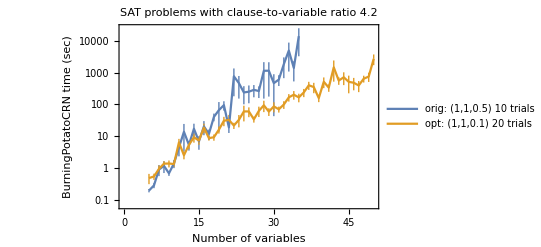

```mathematica
ListLogPlot[{DeleteCases[potatodata,blank],DeleteCases[potatodata2,blank]},Joined->True,Frame->True,FrameLabel->{"Number of variables","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2",PlotLegends->{"orig: (1,1,0.5) 10 trials","opt: (1,1,0.1) 20 trials"}]
```

```mathematica
With[{trials=3,range=Range[10,500,10]},
potatodata3=Table[blank,{n,range}];index=0;
Do[index++;(* allow us to interrupt this without loosing data *)
times=Table[problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,1.0,0.1 ],trials];
potatodata3[[index]]={n,Around[Mean[times],StandardDeviation[times]/Sqrt[trials]]};
Print[index,": ",potatodata3[[index]]],
{n,range}]];
```

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→False,x09→False,x10→False} :=> True (0.494496 sec)

{x01→True,x02→True,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False} :=> True (1.37628 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False} :=> True (0.700916 sec)

1: {10,0.860.27}

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→False,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→False,x19→True,x20→True} :=> True (2.04868 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→False,x07→False,x08→True,x09→False,x10→True,x11→True,x12→False,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True} :=> True (12.6626 sec)

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False} :=> True (8.72974 sec)

2: {20,7.83.1}

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→True,x11→False,x12→True,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→True,x24→True,x25→True,x26→False,x27→True,x28→True,x29→True,x30→True} :=> True (77.5073 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→True,x11→False,x12→True,x13→False,x14→False,x15→False,x16→False,x17→False,x18→False,x19→False,x20→False,x21→False,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True} :=> True (83.1368 sec)

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→True,x08→True,x09→False,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→True,x22→False,x23→False,x24→False,x25→True,x26→False,x27→False,x28→False,x29→False,x30→True} :=> True (112.453 sec)

3: {30,91.11.}

{x01→True,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→False,x10→True,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→True,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True,x35→True,x36→False,x37→True,x38→True,x39→False,x40→True} :=> True (2086.99 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→True,x07→True,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→True,x17→False,x18→True,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→False,x30→False,x31→False,x32→True,x33→True,x34→False,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False} :=> True (43.2818 sec)

{x01→True,x02→False,x03→True,x04→True,x05→True,x06→True,x07→False,x08→True,x09→True,x10→True,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→True,x25→False,x26→True,x27→False,x28→False,x29→False,x30→False,x31→False,x32→False,x33→False,x34→True,x35→False,x36→False,x37→True,x38→False,x39→False,x40→False} :=> True (36.4556 sec)

4: {40,722.682.}

{x01→False,x02→True,x03→False,x04→False,x05→False,x06→True,x07→False,x08→False,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→True,x16→True,x17→False,x18→True,x19→False,x20→True,x21→False,x22→True,x23→False,x24→True,x25→False,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→False,x34→True,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→True,x43→False,x44→True,x45→False,x46→True,x47→True,x48→False,x49→True,x50→False} :=> True (4214.28 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→True,x08→True,x09→False,x10→False,x11→True,x12→False,x13→False,x14→False,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True,x36→False,x37→False,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→True,x46→True,x47→False,x48→True,x49→True,x50→True} :=> True (386.592 sec)

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→False,x19→True,x20→False,x21→False,x22→True,x23→True,x24→False,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→False,x32→True,x33→True,x34→True,x35→False,x36→True,x37→False,x38→False,x39→True,x40→False,x41→False,x42→False,x43→True,x44→True,x45→False,x46→False,x47→False,x48→True,x49→False,x50→False} :=> True (76.8898 sec)

5: {50,1.61.310^3}

{x01→False,x02→True,x03→False,x04→True,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→False,x17→True,x18→False,x19→True,x20→True,x21→False,x22→False,x23→False,x24→True,x25→False,x26→False,x27→True,x28→False,x29→True,x30→True,x31→True,x32→True,x33→False,x34→True,x35→False,x36→True,x37→True,x38→False,x39→True,x40→True,x41→True,x42→False,x43→True,x44→False,x45→True,x46→True,x47→True,x48→True,x49→True,x50→False,x51→True,x52→False,x53→False,x54→False,x55→False,x56→True,x57→False,x58→True,x59→True,x60→True} :=> True (342.258 sec)

{x01→True,x02→False,x03→False,x04→False,x05→False,x06→False,x07→True,x08→False,x09→True,x10→False,x11→True,x12→False,x13→True,x14→True,x15→False,x16→True,x17→False,x18→False,x19→True,x20→False,x21→False,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→False,x37→True,x38→False,x39→True,x40→True,x41→True,x42→True,x43→True,x44→False,x45→False,x46→True,x47→False,x48→False,x49→False,x50→False,x51→True,x52→False,x53→True,x54→False,x55→False,x56→False,x57→False,x58→False,x59→False,x60→False} :=> True (3065.36 sec)

{x01→False,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→False,x18→True,x19→True,x20→False,x21→False,x22→True,x23→False,x24→True,x25→True,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→False,x33→False,x34→False,x35→False,x36→True,x37→False,x38→True,x39→False,x40→True,x41→True,x42→False,x43→True,x44→True,x45→False,x46→True,x47→False,x48→False,x49→True,x50→False,x51→True,x52→False,x53→True,x54→False,x55→False,x56→True,x57→True,x58→False,x59→False,x60→True} :=> True (15991.1 sec)

6: {60,6.5.10^3}

{x01→False,x02→True,x03→True,x04→True,x05→False,x06→True,x07→True,x08→True,x09→True,x10→True,x11→True,x12→False,x13→True,x14→False,x15→False,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→False,x31→True,x32→False,x33→False,x34→True,x35→True,x36→True,x37→True,x38→True,x39→False,x40→True,x41→False,x42→True,x43→False,x44→True,x45→False,x46→False,x47→False,x48→False,x49→True,x50→True,x51→True,x52→False,x53→False,x54→True,x55→True,x56→False,x57→True,x58→False,x59→True,x60→False,x61→True,x62→True,x63→True,x64→True,x65→False,x66→False,x67→False,x68→True,x69→False,x70→True} :=> True (911.895 sec)

{x01→True,x02→True,x03→False,x04→True,x05→True,x06→False,x07→False,x08→False,x09→True,x10→True,x11→True,x12→False,x13→False,x14→True,x15→True,x16→False,x17→True,x18→True,x19→True,x20→False,x21→True,x22→False,x23→True,x24→True,x25→False,x26→False,x27→True,x28→True,x29→False,x30→True,x31→True,x32→False,x33→False,x34→False,x35→True,x36→True,x37→False,x38→False,x39→False,x40→True,x41→False,x42→True,x43→True,x44→True,x45→True,x46→True,x47→False,x48→True,x49→False,x50→True,x51→True,x52→True,x53→False,x54→True,x55→True,x56→False,x57→True,x58→True,x59→True,x60→False,x61→False,x62→True,x63→False,x64→True,x65→False,x66→False,x67→True,x68→False,x69→True,x70→False} :=> True (10591.8 sec)

{x01→False,x02→False,x03→True,x04→True,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→False,x13→True,x14→True,x15→True,x16→True,x17→True,x18→False,x19→True,x20→True,x21→False,x22→True,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→False,x31→True,x32→False,x33→True,x34→False,x35→True,x36→False,x37→False,x38→True,x39→False,x40→True,x41→True,x42→True,x43→False,x44→False,x45→True,x46→True,x47→False,x48→True,x49→True,x50→False,x51→True,x52→True,x53→False,x54→True,x55→False,x56→False,x57→False,x58→True,x59→False,x60→False,x61→True,x62→True,x63→False,x64→False,x65→True,x66→False,x67→False,x68→True,x69→False,x70→True} :=> True (1288.11 sec)

7: {70,4.33.210^3}

{x01→False,x02→False,x03→False,x04→False,x05→False,x06→True,x07→True,x08→False,x09→False,x10→False,x11→False,x12→True,x13→False,x14→True,x15→False,x16→True,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→True,x27→False,x28→True,x29→False,x30→False,x31→False,x32→True,x33→True,x34→True,x35→True,x36→True,x37→True,x38→False,x39→False,x40→False,x41→False,x42→False,x43→False,x44→True,x45→False,x46→True,x47→False,x48→True,x49→False,x50→False,x51→True,x52→True,x53→False,x54→True,x55→False,x56→False,x57→False,x58→True,x59→True,x60→False,x61→False,x62→True,x63→False,x64→True,x65→True,x66→False,x67→False,x68→False,x69→True,x70→False,x71→False,x72→True,x73→False,x74→False,x75→False,x76→False,x77→True,x78→True,x79→True,x80→False} :=> True (5692.87 sec)

{x01→True,x02→False,x03→False,x04→True,x05→False,x06→True,x07→False,x08→True,x09→True,x10→False,x11→False,x12→True,x13→False,x14→False,x15→False,x16→True,x17→False,x18→True,x19→True,x20→False,x21→True,x22→True,x23→True,x24→True,x25→True,x26→True,x27→True,x28→False,x29→True,x30→False,x31→True,x32→True,x33→False,x34→False,x35→True,x36→False,x37→True,x38→True,x39→True,x40→False,x41→True,x42→False,x43→False,x44→True,x45→False,x46→False,x47→False,x48→False,x49→False,x50→True,x51→True,x52→False,x53→True,x54→False,x55→True,x56→True,x57→True,x58→True,x59→False,x60→False,x61→False,x62→True,x63→True,x64→True,x65→False,x66→True,x67→True,x68→False,x69→True,x70→True,x71→False,x72→True,x73→True,x74→False,x75→True,x76→False,x77→False,x78→True,x79→True,x80→False} :=> True (460.842 sec)

{x01→False,x02→True,x03→True,x04→True,x05→True,x06→False,x07→False,x08→True,x09→False,x10→True,x11→False,x12→False,x13→False,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→False,x22→False,x23→False,x24→False,x25→True,x26→False,x27→True,x28→False,x29→False,x30→True,x31→True,x32→False,x33→True,x34→False,x35→False,x36→True,x37→True,x38→False,x39→True,x40→False,x41→True,x42→True,x43→False,x44→False,x45→False,x46→False,x47→True,x48→True,x49→True,x50→True,x51→False,x52→False,x53→False,x54→False,x55→True,x56→False,x57→False,x58→True,x59→False,x60→True,x61→True,x62→True,x63→False,x64→True,x65→False,x66→False,x67→True,x68→True,x69→True,x70→True,x71→False,x72→True,x73→True,x74→True,x75→True,x76→True,x77→False,x78→True,x79→False,x80→True} :=> True (2744.4 sec)

8: {80,3.01.510^3}

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→False,x09→False,x10→True,x11→False,x12→False,x13→True,x14→False,x15→True,x16→False,x17→False,x18→True,x19→False,x20→False,x21→False,x22→False,x23→False,x24→True,x25→True,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→True,x33→True,x34→False,x35→True,x36→False,x37→True,x38→True,x39→False,x40→False,x41→False,x42→True,x43→False,x44→True,x45→False,x46→True,x47→True,x48→False,x49→True,x50→True,x51→False,x52→True,x53→False,x54→True,x55→False,x56→True,x57→True,x58→True,x59→False,x60→False,x61→True,x62→False,x63→False,x64→False,x65→False,x66→False,x67→True,x68→True,x69→True,x70→False,x71→False,x72→False,x73→True,x74→True,x75→False,x76→True,x77→False,x78→False,x79→True,x80→False,x81→False,x82→False,x83→True,x84→False,x85→True,x86→True,x87→False,x88→False,x89→False,x90→True} :=> True (3441.88 sec)

{x01→False,x02→False,x03→True,x04→False,x05→False,x06→False,x07→False,x08→True,x09→True,x10→True,x11→False,x12→True,x13→True,x14→True,x15→False,x16→False,x17→True,x18→True,x19→False,x20→True,x21→True,x22→True,x23→False,x24→False,x25→False,x26→False,x27→False,x28→False,x29→False,x30→False,x31→True,x32→False,x33→False,x34→False,x35→True,x36→False,x37→True,x38→False,x39→False,x40→False,x41→True,x42→False,x43→True,x44→True,x45→False,x46→False,x47→True,x48→False,x49→False,x50→True,x51→True,x52→False,x53→True,x54→False,x55→True,x56→False,x57→False,x58→True,x59→False,x60→False,x61→True,x62→False,x63→True,x64→False,x65→False,x66→False,x67→False,x68→True,x69→True,x70→False,x71→False,x72→True,x73→False,x74→True,x75→True,x76→False,x77→False,x78→False,x79→False,x80→False,x81→False,x82→False,x83→False,x84→True,x85→False,x86→True,x87→False,x88→False,x89→True,x90→False} :=> True (35546. sec)

{x01→True,x02→False,x03→False,x04→False,x05→True,x06→False,x07→False,x08→False,x09→False,x10→False,x11→True,x12→True,x13→True,x14→False,x15→True,x16→True,x17→True,x18→False,x19→False,x20→False,x21→False,x22→False,x23→True,x24→True,x25→False,x26→False,x27→False,x28→True,x29→True,x30→True,x31→True,x32→False,x33→True,x34→False,x35→True,x36→True,x37→False,x38→True,x39→True,x40→True,x41→True,x42→True,x43→False,x44→False,x45→False,x46→True,x47→False,x48→False,x49→False,x50→True,x51→True,x52→True,x53→True,x54→True,x55→False,x56→True,x57→False,x58→True,x59→True,x60→False,x61→False,x62→False,x63→True,x64→False,x65→True,x66→False,x67→False,x68→True,x69→True,x70→True,x71→True,x72→True,x73→True,x74→False,x75→False,x76→True,x77→False,x78→False,x79→True,x80→False,x81→False,x82→False,x83→False,x84→True,x85→False,x86→False,x87→False,x88→True,x89→False,x90→False} :=> True (1552.54 sec)

9: {90,1.41.110^4}

{x001→True,x002→False,x003→True,x004→True,x005→False,x006→False,x007→False,x008→False,x009→True,x010→False,x011→True,x012→True,x013→True,x014→False,x015→True,x016→True,x017→True,x018→True,x019→True,x020→False,x021→False,x022→True,x023→True,x024→True,x025→False,x026→True,x027→True,x028→False,x029→False,x030→False,x031→False,x032→False,x033→True,x034→True,x035→False,x036→True,x037→True,x038→False,x039→False,x040→True,x041→True,x042→True,x043→True,x044→False,x045→False,x046→False,x047→False,x048→False,x049→True,x050→False,x051→True,x052→False,x053→True,x054→False,x055→False,x056→True,x057→False,x058→True,x059→True,x060→True,x061→False,x062→False,x063→True,x064→True,x065→False,x066→True,x067→True,x068→True,x069→False,x070→False,x071→True,x072→False,x073→True,x074→False,x075→True,x076→False,x077→False,x078→False,x079→True,x080→True,x081→True,x082→True,x083→True,x084→True,x085→False,x086→True,x087→False,x088→True,x089→False,x090→False,x091→False,x092→False,x093→True,x094→False,x095→False,x096→False,x097→True,x098→True,x099→True,x100→False} :=> True (3013.69 sec)

{x001→False,x002→False,x003→False,x004→False,x005→False,x006→False,x007→True,x008→False,x009→True,x010→True,x011→True,x012→True,x013→False,x014→False,x015→True,x016→True,x017→True,x018→False,x019→True,x020→True,x021→False,x022→True,x023→False,x024→False,x025→False,x026→False,x027→False,x028→False,x029→False,x030→True,x031→True,x032→False,x033→False,x034→False,x035→False,x036→False,x037→False,x038→True,x039→False,x040→False,x041→True,x042→True,x043→True,x044→True,x045→False,x046→True,x047→False,x048→True,x049→False,x050→True,x051→True,x052→False,x053→True,x054→True,x055→True,x056→True,x057→False,x058→False,x059→False,x060→True,x061→True,x062→True,x063→False,x064→False,x065→False,x066→False,x067→False,x068→True,x069→False,x070→False,x071→False,x072→True,x073→False,x074→False,x075→False,x076→True,x077→True,x078→False,x079→True,x080→False,x081→True,x082→False,x083→False,x084→True,x085→False,x086→True,x087→False,x088→False,x089→True,x090→True,x091→True,x092→False,x093→False,x094→True,x095→True,x096→False,x097→False,x098→False,x099→False,x100→True} :=> True (1729.69 sec)

{x001→False,x002→False,x003→False,x004→False,x005→False,x006→False,x007→False,x008→True,x009→False,x010→False,x011→False,x012→False,x013→False,x014→False,x015→False,x016→True,x017→False,x018→False,x019→False,x020→False,x021→False,x022→True,x023→True,x024→True,x025→True,x026→True,x027→True,x028→True,x029→True,x030→True,x031→True,x032→True,x033→False,x034→True,x035→False,x036→True,x037→True,x038→True,x039→False,x040→False,x041→True,x042→False,x043→False,x044→False,x045→True,x046→False,x047→True,x048→True,x049→False,x050→True,x051→False,x052→False,x053→True,x054→False,x055→True,x056→False,x057→True,x058→True,x059→False,x060→False,x061→True,x062→False,x063→True,x064→True,x065→True,x066→True,x067→False,x068→True,x069→True,x070→True,x071→False,x072→False,x073→False,x074→False,x075→True,x076→False,x077→False,x078→True,x079→False,x080→True,x081→True,x082→False,x083→True,x084→True,x085→False,x086→True,x087→False,x088→False,x089→False,x090→False,x091→True,x092→False,x093→False,x094→False,x095→False,x096→True,x097→True,x098→True,x099→False,x100→False} :=> True (117311. sec)

10: {100,4.4.10^4}

$Aborted

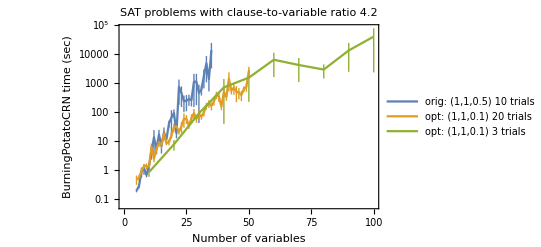

```mathematica
ListLogPlot[{DeleteCases[potatodata,blank],DeleteCases[potatodata2,blank],DeleteCases[potatodata3,blank]},Joined->True,Frame->True,FrameLabel->{"Number of variables","BurningPotatoCRN time (sec)"},PlotLabel->"SAT problems with clause-to-variable ratio 4.2",PlotLegends->{"orig: (1,1,0.5) 10 trials","opt: (1,1,0.1) 20 trials","opt: (1,1,0.1) 3 trials"}]
```

```mathematica
With[{n=200},problem=SolvableRandomKSAT[3,n,Round[4.2 n]];TuneBurningPotatoCRN[problem,1.0,1.0,0.1 ]]
```

$Aborted

The above assesses BurningPotatoCRN’s ability to solve standard random 3SAT problems, and that the scaling has the log-plot “flattening off” that is typical of WalkSAT algorithms.  Very satisfying!  (Granted, WalkSATCRN can solve 500-variable problems in this time, and my implementation of a simple classical WalkSAT can solve 5000-variable problems.)

The spatial layout uses O(n m) cells to encode an n-variable m-clause formula, using a crossbar grid for connectivity because each clause could be connected to arbitrary variables. This is a circumstance that is natural to non-spatial algorithms such as MiniSAT and the well-mixed WalkSATCRN, but which is maximally inefficient for the surface-localized BurningPotatoCRN.   Can we turn it around, and examine another class of random hard 3SAT problems that are more natural to surface layouts -- might these give examples where BurningPotatoCRN (or other surface CRN SAT solvers) is on a more even playing field with the other methods?

INCOMPLETE STUFF BELOW

```mathematica
(* returns a randomly-tiled surface SAT circuit, along with its logical formula *)
(* p is the probability of negating the self-wire within a tile, and q is the probability of negating an other-wire *)
(* the layout will be X tiles by Y tiles, so it will have (X Y + 2 X + 2 Y) variables and (4 X Y) clauses, so it's likely to be satisfiable *)
RandomLayoutPotato3SAT[X_,Y_,p_,q_]:=Module[{clauseinit,clausegizmo,clauseend,crossinit,crossgizmo,crossend,chunk,surface3D,formula,vars,clauses,N,M,pos,i},
vars=BooleanVariables[formula]; N=Length[vars];
clauses=List@@formula; M=Length[clauses];

THIS CODE IS NOT COMPLETE; IT IS NOT EVEN REALLY STARTED;

clauseinit=Table[o,{3},{5},{1}];
clausegizmo[clause_]:={ 
Table[o,{5},{10}],
Table[o,{5},{10}],
{{o,b,a,c,o,a,b,c,a,o},
{o,c,o,b,S,C,o,o,b,o},
{o,a,o,o,a,o,o,a,c,o},
{o,F,o,o,F,o,o,F,o,o},
{o,x,o,o,y,o,o,z,o,o}}
}/.{S->S001,C->cO,x:>If[Head[clause[[1]]]===Not,bO,b],y:>If[Head[clause[[2]]]===Not,bO,b],z:>If[Head[clause[[3]]]===Not,bO,b]};
clauseend=Table[o,{3},{5},{5}];

crossinit={{{R0},{o},{o}},{{o},{o},{o}},{{o},{o},{o}}};
crossgizmo[ var_][clause_]:=Which[
var===First[BooleanVariables[clause[[1]]]],
{{{a,E,b,F,a,c,b,a,c,b},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,c,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,o,o,o,c,o,o,c,o,o},
{o,o,o,o,b,o,o,b,o,o}}},
var===First[BooleanVariables[clause[[2]]]],
{{{a,c,b,a,E,b,F,a,c,b},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,c,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,o,o,o,c,o,o},
{o,b,o,o,o,o,o,b,o,o}}},
var===First[BooleanVariables[clause[[3]]]],
{{{a,c,b,a,c,b,a,E,b,F},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,o,o,o,c,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,c,o,o,o,o,o},
{o,b,o,o,b,o,o,o,o,o}}},
True,
{{{a,c,b,a,c,b,a,c,o,b},
{o,o,o,o,o,o,o,b,a,c},
{o,o,o,o,o,o,o,o,o,o}},
{{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o},
{o,o,o,o,o,o,o,o,o,o}},
{{o,a,o,o,a,o,o,a,o,o},
{o,c,o,o,c,o,o,c,o,o},
{o,b,o,o,b,o,o,b,o,o}}}
];
crossend={
{{a,E,c,a,R0},{o,o,o,o,o},{o,o,o,o,o}},
{{o,b,o,o,o},{o,o,o,o,o},{o,o,o,o,o}},
{{o,c,a,R0,o},{o,o,o,o,o},{o,o,o,o,o}}
};
chunk[var_][clause_]:=Which[
var===None&&clause===First,clauseinit,
var===None&&clause===Last,clauseend,
var===None,clausegizmo[clause],
clause===First,crossinit,
clause===Last,crossend,
True,crossgizmo[var][clause]
];

surface3D=ArrayFlatten[Table[chunk[var][clause], {1},{var,Join[{None},vars]},{clause,Join[{First},clauses,{Last}]}],3];
surface3D /.{E->E}
]

AssignmentFromPotato3SAT[formula_,surface3D_]:=Module[{vars,N},
vars=BooleanVariables[formula]; N=Length[vars];
MapThread[Rule,{vars,surface3D[[1,3+3 Range[N],1]]/.{R0->False,R1->True}}]
]
```

To Do (July 3, 2021): 
	2. Generate 2D SAT networks... these will be “easier” for BurningPotatoCRN to solve, and we can translate them to MiniSAT and see whether any of them are hard... 
	3. Adjust Dynamic movies such that we can more clearly watch this system in action...
	4. Analyze a single wire in terms of its probability of flipping based on how many incident clauses will be broken.
	5. Empirically examine “wound healing” from a perturbation in the 2D networks.   Is there Ising-like or Toom-like dynamics?
	6. Consider using 3D more.  We could arrange the m clauses in a √m×√m array, perpendicular to a stack of n wires that fan out a tree to intersect with each clause.  Space is still O(n m) but now average wire length is reduced from O(n+m) to  O(n + √m).  Because for the hard problems we are considering  m=O(n), this is unlikely to result in a significant speed-up.  Oh well.  Maybe we can do better with greedy packing to set things up?  Start with a √n×√narray of wires (variables) extending linearly with enough spacing for the things we’ll need to do.  We will arrange clauses in rings around the bundle of variable wires, with (up to)  4 √nclauses in each ring.   We’ll wire up the clauses one by one: given a new clause, we’ll look at each unused space in extant rings, and see whether we can successfully wire up directly to the three needed variables within the allotted thickness of the ring’s cross-section.  The first unused space that works, gets taken, and we move on to the next clause.  If this greedy strategy is successful, then our SAT-solver circuit is contained within O(√n×√n×√n) space for m=O(n).  That would ensure each wire is of length O(√n), which in turn provides a O(√n) speed-up.  On the scale of exponentials for NP-hard problems, this may not be a big deal.  Further, we don’t know whether the greedy algorithm will succeed in a layout.  (Layout must be easy!  If layout must solve an optimization problem, it might be harder than solving the SAT problem itself...)  Since we have O(√n)columns in the cross-section, and we have O(√n) literals from clauses in the ring that need to find their variable by following rows and columns, using cross-section thickness of O(1) ought to be enough to ensure O(√n) rings will typically suffice.  For n=50, this might result in only a factor of 4 or so speed-up.
	7.  Canonical cortical microcircuit?  LTU-SAT?

I have encountered no examples of BurningPotatoCRN failing to solve a solvable problem.  But can we prove that the  will work correctly every time regardless of problem size, and gain some understanding of its performance?

By “correctness”, we mean that (a) if a formula is not satisfiable, then the surface CRN will not halt; (b) if a formula is satisfiable, the surface CRN will halt; (c) if the surface CRN halts, then a satisfying solution can be read out.

I believe it is straightforward to show that, given the initial layout, if a wire has no signal on it and no enabled reactions between the wire and nodes, then the potatoes that connect to that wire all agree on the wire’s value.  The trickiest part here is to show that the NOT gates are handled consistently.

Further, if a wire has a signal or enabled reactions, then the CRN has not yet halted.  So, if the CRN has halted, then all potatoes agree on the values of all wires, and all potatoes are (by construction) satisfied.  So we can read out a satisfying solution.  That handles (c) and (a).

For (b), we need to show that the randomness of whether a signal is accepted or rejected upon arriving at a SAT potato is sufficient to reach a valid solution, if one exists.   That is, the search space is not somehow restricted to exploring a subspace that might not contain the solution.  

Consider a wire connecting k potatoes, with a signal just emitted from potato #1.  That means that the other potatoes store a different value from #1.  Let’s suppose that b<k of them will be broken if they accept the value suggested by #1.  If b=0 then all potatoes are guaranteed to accept the change and the signal will disappear.  Otherwise, when the signal arrives at each broken potato, there is a probability  p=(2 slow)/(1 + 2 slow) that the signal will be accepted and an outgoing signal produced on another wire; accordingly with probability q=1-p the signal will be rejected and reflected, such that all node that had accepted the signal (including #1) will soon be asked to change back.  We somewhat arbitrarily choose slow=0.5 so  p=0.5 and thus the chance of the signal fully disappearing (but new signals being created on other wires) on the first round is 2^-b.   (We are imagining that there is no activity beyond this wire and its potatoes, for simplicity.)   

Regardless of the probabilities, what are the possibilities, for this wire becoming resolved with out further interference from outside? 
(1) Potato #1’s recommendation is accepted; thus all b broken potatoes must emit signals, flipping one of their two other wires.
(2) Potatoes #1’s recommendation is rejected; but in doing so, some number 0≤b'<b of the other potatoes will have changed state and emitted signals in the process.

What does this imply?

Consider surface states where each wire has either zero or exactly 1 signal and no node has enabled reactions.   Can we always reach such a state?  I presume so, but a proof (or counter-example) would be nice.  In such states, we can say that that “current state” of each wire is the value on the “source” side of the directional signal.   You might think that this implies that the “current state” of the potatoes this signal breaks is “not satisfied” but that’s not quite so, because it’s possible that there is an incoming signal on another wire whose “current state” will fix those potatoes.  So it’s complicated.  Someone needs to think hard about this...   maybe understanding it more clearly would point to ways to modify and improve the effectiveness of this surface CRN construction.

Final thoughts from reading during this exercise:

1. I stumbled upon a WalkSAT variant called probSAT that uses a broader class of random choices to select which variable to flip (“Choosing Probability Distributions for Stochastic Local Search and the Role of Make versus Break” -- Adrian Balint and Uwe Schoning, 2012).  This might be a somewhat closer match to WalkSATCRN, and should be referenced henceforth.  Would be interesting to try to establish the connection more carefully -- and the differences. 

2. The classical WalkSAT has a probability for choosing a random variable from the chosen broken clause (rather than the min-breaking variable) that is surprisingly high -- often tuned between 0.5 to 0.6.  But if there exists a variable that will break ZERO other clauses, the choice is to deterministically accept it.  Again, I am not sure exactly how this relates to WalkSATCRN.  It seems to have some similarity to BurningPotatoCRN’s lack of rejection of flip requests that don’t break a clause.

3. A proper treatment of a universal theoretical restart strategy was given in Luby, Sinclair, Zuckerman: “Optimal Speedup of Las Vegas Algorithms” (1993).  But apparently it’s debatable how much of an advantage it typically confers.

4. Can a CRN (well-mixed or surface) solve the decision problem, i.e. answer both “yes” cases and “no” cases?  Of course -- Chris Thachuk showed that it’s possible.  But can something like a CDCL SAT-solver logic being implemented as a CRN?  Maybe so!  In fact, it might be nice to phrase it as a single Reaction Schema System -- and even better if it compiles to a reasonable size.